## Part b : Regression

```mathematica
(*originalData = Import["C:\\Users\\joshu\\Desktop\\archive\\train.csv"];*)
originalData = Import["C:\\Users\\dylan\\Downloads\\archive\\train.csv"];


Print["Sample: ",MatrixForm[Take[originalData,10]],Length[originalData]-1];
```

Sample: (Id | MSSubClass | MSZoning | LotFrontage | LotArea | Street | Alley | LotShape | LandContour | Utilities | LotConfig | LandSlope | Neighborhood | Condition1 | Condition2 | BldgType | HouseStyle | OverallQual | OverallCond | YearBuilt | YearRemodAdd | RoofStyle | RoofMatl | Exterior1st | Exterior2nd | MasVnrType | MasVnrArea | ExterQual | ExterCond | Foundation | BsmtQual | BsmtCond | BsmtExposure | BsmtFinType1 | BsmtFinSF1 | BsmtFinType2 | BsmtFinSF2 | BsmtUnfSF | TotalBsmtSF | Heating | HeatingQC | CentralAir | Electrical | 1stFlrSF | 2ndFlrSF | LowQualFinSF | GrLivArea | BsmtFullBath | BsmtHalfBath | FullBath | HalfBath | BedroomAbvGr | KitchenAbvGr | KitchenQual | TotRmsAbvGrd | Functional | Fireplaces | FireplaceQu | GarageType | GarageYrBlt | GarageFinish | GarageCars | GarageArea | GarageQual | GarageCond | PavedDrive | WoodDeckSF | OpenPorchSF | EnclosedPorch | 3SsnPorch | ScreenPorch | PoolArea | PoolQC | Fence | MiscFeature | MiscVal | MoSold | YrSold | SaleType | SaleCondition | SalePrice
1 | 60 | RL | 65 | 8450 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2003 | 2003 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 196 | Gd | TA | PConc | Gd | TA | No | GLQ | 706 | Unf | 0 | 150 | 856 | GasA | Ex | Y | SBrkr | 856 | 854 | 0 | 1710 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 8 | Typ | 0 | NA | Attchd | 2003 | RFn | 2 | 548 | TA | TA | Y | 0 | 61 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 2 | 2008 | WD | Normal | 208500
2 | 20 | RL | 80 | 9600 | Pave | NA | Reg | Lvl | AllPub | FR2 | Gtl | Veenker | Feedr | Norm | 1Fam | 1Story | 6 | 8 | 1976 | 1976 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | CBlock | Gd | TA | Gd | ALQ | 978 | Unf | 0 | 284 | 1262 | GasA | Ex | Y | SBrkr | 1262 | 0 | 0 | 1262 | 0 | 1 | 2 | 0 | 3 | 1 | TA | 6 | Typ | 1 | TA | Attchd | 1976 | RFn | 2 | 460 | TA | TA | Y | 298 | 0 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 5 | 2007 | WD | Normal | 181500
3 | 60 | RL | 68 | 11250 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2001 | 2002 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 162 | Gd | TA | PConc | Gd | TA | Mn | GLQ | 486 | Unf | 0 | 434 | 920 | GasA | Ex | Y | SBrkr | 920 | 866 | 0 | 1786 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 6 | Typ | 1 | TA | Attchd | 2001 | RFn | 2 | 608 | TA | TA | Y | 0 | 42 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 9 | 2008 | WD | Normal | 223500
4 | 70 | RL | 60 | 9550 | Pave | NA | IR1 | Lvl | AllPub | Corner | Gtl | Crawfor | Norm | Norm | 1Fam | 2Story | 7 | 5 | 1915 | 1970 | Gable | CompShg | Wd Sdng | Wd Shng | None | 0 | TA | TA | BrkTil | TA | Gd | No | ALQ | 216 | Unf | 0 | 540 | 756 | GasA | Gd | Y | SBrkr | 961 | 756 | 0 | 1717 | 1 | 0 | 1 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Detchd | 1998 | Unf | 3 | 642 | TA | TA | Y | 0 | 35 | 272 | 0 | 0 | 0 | NA | NA | NA | 0 | 2 | 2006 | WD | Abnorml | 140000
5 | 60 | RL | 84 | 14260 | Pave | NA | IR1 | Lvl | AllPub | FR2 | Gtl | NoRidge | Norm | Norm | 1Fam | 2Story | 8 | 5 | 2000 | 2000 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 350 | Gd | TA | PConc | Gd | TA | Av | GLQ | 655 | Unf | 0 | 490 | 1145 | GasA | Ex | Y | SBrkr | 1145 | 1053 | 0 | 2198 | 1 | 0 | 2 | 1 | 4 | 1 | Gd | 9 | Typ | 1 | TA | Attchd | 2000 | RFn | 3 | 836 | TA | TA | Y | 192 | 84 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 12 | 2008 | WD | Normal | 250000
6 | 50 | RL | 85 | 14115 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | Mitchel | Norm | Norm | 1Fam | 1.5Fin | 5 | 5 | 1993 | 1995 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | Wood | Gd | TA | No | GLQ | 732 | Unf | 0 | 64 | 796 | GasA | Ex | Y | SBrkr | 796 | 566 | 0 | 1362 | 1 | 0 | 1 | 1 | 1 | 1 | TA | 5 | Typ | 0 | NA | Attchd | 1993 | Unf | 2 | 480 | TA | TA | Y | 40 | 30 | 0 | 320 | 0 | 0 | NA | MnPrv | Shed | 700 | 10 | 2009 | WD | Normal | 143000
7 | 20 | RL | 75 | 10084 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | Somerst | Norm | Norm | 1Fam | 1Story | 8 | 5 | 2004 | 2005 | Gable | CompShg | VinylSd | VinylSd | Stone | 186 | Gd | TA | PConc | Ex | TA | Av | GLQ | 1369 | Unf | 0 | 317 | 1686 | GasA | Ex | Y | SBrkr | 1694 | 0 | 0 | 1694 | 1 | 0 | 2 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Attchd | 2004 | RFn | 2 | 636 | TA | TA | Y | 255 | 57 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 8 | 2007 | WD | Normal | 307000
8 | 60 | RL | NA | 10382 | Pave | NA | IR1 | Lvl | AllPub | Corner | Gtl | NWAmes | PosN | Norm | 1Fam | 2Story | 7 | 6 | 1973 | 1973 | Gable | CompShg | HdBoard | HdBoard | Stone | 240 | TA | TA | CBlock | Gd | TA | Mn | ALQ | 859 | BLQ | 32 | 216 | 1107 | GasA | Ex | Y | SBrkr | 1107 | 983 | 0 | 2090 | 1 | 0 | 2 | 1 | 3 | 1 | TA | 7 | Typ | 2 | TA | Attchd | 1973 | RFn | 2 | 484 | TA | TA | Y | 235 | 204 | 228 | 0 | 0 | 0 | NA | NA | Shed | 350 | 11 | 2009 | WD | Normal | 200000
9 | 50 | RM | 51 | 6120 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | OldTown | Artery | Norm | 1Fam | 1.5Fin | 7 | 5 | 1931 | 1950 | Gable | CompShg | BrkFace | Wd Shng | None | 0 | TA | TA | BrkTil | TA | TA | No | Unf | 0 | Unf | 0 | 952 | 952 | GasA | Gd | Y | FuseF | 1022 | 752 | 0 | 1774 | 0 | 0 | 2 | 0 | 2 | 2 | TA | 8 | Min1 | 2 | TA | Detchd | 1931 | Unf | 2 | 468 | Fa | TA | Y | 90 | 0 | 205 | 0 | 0 | 0 | NA | NA | NA | 0 | 4 | 2008 | WD | Abnorml | 129900)1460

## Feature Extraction and Generation

```mathematica
ClearAll[x,y,m,n,ny,y,xNames,xLabels,yNames,yLabels];

safeNum[val_] := If[NumberQ[val], val, 0];

encodeQual[val_]:=Lookup[<|"Ex"->5,"Gd"->4,"TA"->3,"Fa"->2,"Po"->1,"NA"->0|>,ToString[val],0];

x = {1,#[[2]],#[[4]],#[[5]],#[[18]],#[[19]],#[[20]],#[[21]],#[[27]],#[[35]],#[[37]],#[[38]],

(*Ordinal Quality Columns:ExterQual (#28),BsmtQual (#31),HeatingQC (#41),KitchenQual (#54),GarageQual (#64)*)encodeQual[#[[28]]],encodeQual[#[[31]]],encodeQual[#[[41]]],encodeQual[#[[54]]],encodeQual[#[[64]]],

(*TotalSF=TotalBsmtSF (#39)+1stFlrSF (#44)+2ndFlrSF (#45)*)
safeNum[#[[39]]]+safeNum[#[[44]]]+safeNum[#[[45]]],

#[[46]],

(*TotalBathrooms=FullBath (#50)+0.5*HalfBath (#51)+BsmtFullBath (#48)+0.5*BsmtHalfBath (#49)*)
safeNum[#[[50]]]+0.5*safeNum[#[[51]]]+safeNum[#[[48]]]+0.5*safeNum[#[[49]]],

#[[52]],#[[53]],#[[55]],#[[57]],#[[60]],#[[62]],#[[63]],#[[67]],#[[68]],#[[69]],#[[70]],#[[71]],#[[72]],#[[76]],#[[77]],#[[78]]}& /@  Drop[originalData,1];
y = {#[[81]]}      & /@  Drop[originalData,1];

m = Length[x];
n = Length[x[[1]]]-1;
ny = Length[y[[1]]];

replaceNAWithMean[colData_]:=Module[{meanNumber,numericData},numericData=Select[colData,NumberQ[#]&];
If[Length[numericData]==0,colData,meanNumber=1.0 Mean[numericData];
Map[If[#==="NA",meanNumber,#]&,colData]]];

cleanedX=Transpose[Map[replaceNAWithMean,Transpose[x]]];
x=cleanedX;

disp = Min[10,m];

Print["Sample: ",MatrixForm[Take[originalData,disp+1]],"   x: ",MatrixForm[Take[x,disp]],"   y: ",MatrixForm[Take[y,disp]]];

i=disp;

Print[Superscript["x","("<>ToString[i]<>")"]," = ", x[[i]]];
Print[Superscript["y","("<>ToString[i]<>")"]," = ", y[[i]]];
Print["

"];
xNames = Table[Subscript["x",ToString[i]],{i,0,n}];
xLabels = Table[Subsuperscript["x",ToString[j],"("<>ToString[i]<>")"],{i,1,m},{j,0,n}];
Print["xNames = ",xNames];
Print["x = ",MatrixForm[Prepend[Take[x,disp],xNames]]," = ",MatrixForm[Prepend[Take[xLabels,disp],xNames]]];
```

Sample: (Id | MSSubClass | MSZoning | LotFrontage | LotArea | Street | Alley | LotShape | LandContour | Utilities | LotConfig | LandSlope | Neighborhood | Condition1 | Condition2 | BldgType | HouseStyle | OverallQual | OverallCond | YearBuilt | YearRemodAdd | RoofStyle | RoofMatl | Exterior1st | Exterior2nd | MasVnrType | MasVnrArea | ExterQual | ExterCond | Foundation | BsmtQual | BsmtCond | BsmtExposure | BsmtFinType1 | BsmtFinSF1 | BsmtFinType2 | BsmtFinSF2 | BsmtUnfSF | TotalBsmtSF | Heating | HeatingQC | CentralAir | Electrical | 1stFlrSF | 2ndFlrSF | LowQualFinSF | GrLivArea | BsmtFullBath | BsmtHalfBath | FullBath | HalfBath | BedroomAbvGr | KitchenAbvGr | KitchenQual | TotRmsAbvGrd | Functional | Fireplaces | FireplaceQu | GarageType | GarageYrBlt | GarageFinish | GarageCars | GarageArea | GarageQual | GarageCond | PavedDrive | WoodDeckSF | OpenPorchSF | EnclosedPorch | 3SsnPorch | ScreenPorch | PoolArea | PoolQC | Fence | MiscFeature | MiscVal | MoSold | YrSold | SaleType | SaleCondition | SalePrice
1 | 60 | RL | 65 | 8450 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2003 | 2003 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 196 | Gd | TA | PConc | Gd | TA | No | GLQ | 706 | Unf | 0 | 150 | 856 | GasA | Ex | Y | SBrkr | 856 | 854 | 0 | 1710 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 8 | Typ | 0 | NA | Attchd | 2003 | RFn | 2 | 548 | TA | TA | Y | 0 | 61 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 2 | 2008 | WD | Normal | 208500
2 | 20 | RL | 80 | 9600 | Pave | NA | Reg | Lvl | AllPub | FR2 | Gtl | Veenker | Feedr | Norm | 1Fam | 1Story | 6 | 8 | 1976 | 1976 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | CBlock | Gd | TA | Gd | ALQ | 978 | Unf | 0 | 284 | 1262 | GasA | Ex | Y | SBrkr | 1262 | 0 | 0 | 1262 | 0 | 1 | 2 | 0 | 3 | 1 | TA | 6 | Typ | 1 | TA | Attchd | 1976 | RFn | 2 | 460 | TA | TA | Y | 298 | 0 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 5 | 2007 | WD | Normal | 181500
3 | 60 | RL | 68 | 11250 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | CollgCr | Norm | Norm | 1Fam | 2Story | 7 | 5 | 2001 | 2002 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 162 | Gd | TA | PConc | Gd | TA | Mn | GLQ | 486 | Unf | 0 | 434 | 920 | GasA | Ex | Y | SBrkr | 920 | 866 | 0 | 1786 | 1 | 0 | 2 | 1 | 3 | 1 | Gd | 6 | Typ | 1 | TA | Attchd | 2001 | RFn | 2 | 608 | TA | TA | Y | 0 | 42 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 9 | 2008 | WD | Normal | 223500
4 | 70 | RL | 60 | 9550 | Pave | NA | IR1 | Lvl | AllPub | Corner | Gtl | Crawfor | Norm | Norm | 1Fam | 2Story | 7 | 5 | 1915 | 1970 | Gable | CompShg | Wd Sdng | Wd Shng | None | 0 | TA | TA | BrkTil | TA | Gd | No | ALQ | 216 | Unf | 0 | 540 | 756 | GasA | Gd | Y | SBrkr | 961 | 756 | 0 | 1717 | 1 | 0 | 1 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Detchd | 1998 | Unf | 3 | 642 | TA | TA | Y | 0 | 35 | 272 | 0 | 0 | 0 | NA | NA | NA | 0 | 2 | 2006 | WD | Abnorml | 140000
5 | 60 | RL | 84 | 14260 | Pave | NA | IR1 | Lvl | AllPub | FR2 | Gtl | NoRidge | Norm | Norm | 1Fam | 2Story | 8 | 5 | 2000 | 2000 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 350 | Gd | TA | PConc | Gd | TA | Av | GLQ | 655 | Unf | 0 | 490 | 1145 | GasA | Ex | Y | SBrkr | 1145 | 1053 | 0 | 2198 | 1 | 0 | 2 | 1 | 4 | 1 | Gd | 9 | Typ | 1 | TA | Attchd | 2000 | RFn | 3 | 836 | TA | TA | Y | 192 | 84 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 12 | 2008 | WD | Normal | 250000
6 | 50 | RL | 85 | 14115 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | Mitchel | Norm | Norm | 1Fam | 1.5Fin | 5 | 5 | 1993 | 1995 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | Wood | Gd | TA | No | GLQ | 732 | Unf | 0 | 64 | 796 | GasA | Ex | Y | SBrkr | 796 | 566 | 0 | 1362 | 1 | 0 | 1 | 1 | 1 | 1 | TA | 5 | Typ | 0 | NA | Attchd | 1993 | Unf | 2 | 480 | TA | TA | Y | 40 | 30 | 0 | 320 | 0 | 0 | NA | MnPrv | Shed | 700 | 10 | 2009 | WD | Normal | 143000
7 | 20 | RL | 75 | 10084 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | Somerst | Norm | Norm | 1Fam | 1Story | 8 | 5 | 2004 | 2005 | Gable | CompShg | VinylSd | VinylSd | Stone | 186 | Gd | TA | PConc | Ex | TA | Av | GLQ | 1369 | Unf | 0 | 317 | 1686 | GasA | Ex | Y | SBrkr | 1694 | 0 | 0 | 1694 | 1 | 0 | 2 | 0 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Attchd | 2004 | RFn | 2 | 636 | TA | TA | Y | 255 | 57 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 8 | 2007 | WD | Normal | 307000
8 | 60 | RL | NA | 10382 | Pave | NA | IR1 | Lvl | AllPub | Corner | Gtl | NWAmes | PosN | Norm | 1Fam | 2Story | 7 | 6 | 1973 | 1973 | Gable | CompShg | HdBoard | HdBoard | Stone | 240 | TA | TA | CBlock | Gd | TA | Mn | ALQ | 859 | BLQ | 32 | 216 | 1107 | GasA | Ex | Y | SBrkr | 1107 | 983 | 0 | 2090 | 1 | 0 | 2 | 1 | 3 | 1 | TA | 7 | Typ | 2 | TA | Attchd | 1973 | RFn | 2 | 484 | TA | TA | Y | 235 | 204 | 228 | 0 | 0 | 0 | NA | NA | Shed | 350 | 11 | 2009 | WD | Normal | 200000
9 | 50 | RM | 51 | 6120 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | OldTown | Artery | Norm | 1Fam | 1.5Fin | 7 | 5 | 1931 | 1950 | Gable | CompShg | BrkFace | Wd Shng | None | 0 | TA | TA | BrkTil | TA | TA | No | Unf | 0 | Unf | 0 | 952 | 952 | GasA | Gd | Y | FuseF | 1022 | 752 | 0 | 1774 | 0 | 0 | 2 | 0 | 2 | 2 | TA | 8 | Min1 | 2 | TA | Detchd | 1931 | Unf | 2 | 468 | Fa | TA | Y | 90 | 0 | 205 | 0 | 0 | 0 | NA | NA | NA | 0 | 4 | 2008 | WD | Abnorml | 129900
10 | 190 | RL | 50 | 7420 | Pave | NA | Reg | Lvl | AllPub | Corner | Gtl | BrkSide | Artery | Artery | 2fmCon | 1.5Unf | 5 | 6 | 1939 | 1950 | Gable | CompShg | MetalSd | MetalSd | None | 0 | TA | TA | BrkTil | TA | TA | No | GLQ | 851 | Unf | 0 | 140 | 991 | GasA | Ex | Y | SBrkr | 1077 | 0 | 0 | 1077 | 1 | 0 | 1 | 0 | 2 | 2 | TA | 5 | Typ | 2 | TA | Attchd | 1939 | RFn | 1 | 205 | Gd | TA | Y | 0 | 4 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 1 | 2008 | WD | Normal | 118000)   x: (1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008
1 | 20 | 80 | 9600 | 6 | 8 | 1976 | 1976 | 0 | 978 | 0 | 284 | 3 | 4 | 5 | 3 | 3 | 2524 | 0 | 2.5 | 3 | 1 | 6 | 1 | 1976 | 2 | 460 | 298 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 2007
1 | 60 | 68 | 11250 | 7 | 5 | 2001 | 2002 | 162 | 486 | 0 | 434 | 4 | 4 | 5 | 4 | 3 | 2706 | 0 | 3.5 | 3 | 1 | 6 | 1 | 2001 | 2 | 608 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 9 | 2008
1 | 70 | 60 | 9550 | 7 | 5 | 1915 | 1970 | 0 | 216 | 0 | 540 | 3 | 3 | 4 | 4 | 3 | 2473 | 0 | 2. | 3 | 1 | 7 | 1 | 1998 | 3 | 642 | 0 | 35 | 272 | 0 | 0 | 0 | 0 | 2 | 2006
1 | 60 | 84 | 14260 | 8 | 5 | 2000 | 2000 | 350 | 655 | 0 | 490 | 4 | 4 | 5 | 4 | 3 | 3343 | 0 | 3.5 | 4 | 1 | 9 | 1 | 2000 | 3 | 836 | 192 | 84 | 0 | 0 | 0 | 0 | 0 | 12 | 2008
1 | 50 | 85 | 14115 | 5 | 5 | 1993 | 1995 | 0 | 732 | 0 | 64 | 3 | 4 | 5 | 3 | 3 | 2158 | 0 | 2.5 | 1 | 1 | 5 | 0 | 1993 | 2 | 480 | 40 | 30 | 0 | 320 | 0 | 0 | 700 | 10 | 2009
1 | 20 | 75 | 10084 | 8 | 5 | 2004 | 2005 | 186 | 1369 | 0 | 317 | 4 | 5 | 5 | 4 | 3 | 3380 | 0 | 3. | 3 | 1 | 7 | 1 | 2004 | 2 | 636 | 255 | 57 | 0 | 0 | 0 | 0 | 0 | 8 | 2007
1 | 60 | 70.05 | 10382 | 7 | 6 | 1973 | 1973 | 240 | 859 | 32 | 216 | 3 | 4 | 5 | 3 | 3 | 3197 | 0 | 3.5 | 3 | 1 | 7 | 2 | 1973 | 2 | 484 | 235 | 204 | 228 | 0 | 0 | 0 | 350 | 11 | 2009
1 | 50 | 51 | 6120 | 7 | 5 | 1931 | 1950 | 0 | 0 | 0 | 952 | 3 | 3 | 4 | 3 | 2 | 2726 | 0 | 2. | 2 | 2 | 8 | 2 | 1931 | 2 | 468 | 90 | 0 | 205 | 0 | 0 | 0 | 0 | 4 | 2008
1 | 190 | 50 | 7420 | 5 | 6 | 1939 | 1950 | 0 | 851 | 0 | 140 | 3 | 3 | 5 | 3 | 4 | 2068 | 0 | 2. | 2 | 2 | 5 | 2 | 1939 | 1 | 205 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 2008)   y: (208500
181500
223500
140000
250000
143000
307000
200000
129900
118000)

x^(10) = {1,190,50,7420,5,6,1939,1950,0,851,0,140,3,3,5,3,4,2068,0,2.,2,2,5,2,1939,1,205,0,4,0,0,0,0,0,1,2008}

y^(10) = {118000}

xNames = {x_0,x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10,x_11,x_12,x_13,x_14,x_15,x_16,x_17,x_18,x_19,x_20,x_21,x_22,x_23,x_24,x_25,x_26,x_27,x_28,x_29,x_30,x_31,x_32,x_33,x_34,x_35}

x = (x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008
1 | 20 | 80 | 9600 | 6 | 8 | 1976 | 1976 | 0 | 978 | 0 | 284 | 3 | 4 | 5 | 3 | 3 | 2524 | 0 | 2.5 | 3 | 1 | 6 | 1 | 1976 | 2 | 460 | 298 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 2007
1 | 60 | 68 | 11250 | 7 | 5 | 2001 | 2002 | 162 | 486 | 0 | 434 | 4 | 4 | 5 | 4 | 3 | 2706 | 0 | 3.5 | 3 | 1 | 6 | 1 | 2001 | 2 | 608 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 9 | 2008
1 | 70 | 60 | 9550 | 7 | 5 | 1915 | 1970 | 0 | 216 | 0 | 540 | 3 | 3 | 4 | 4 | 3 | 2473 | 0 | 2. | 3 | 1 | 7 | 1 | 1998 | 3 | 642 | 0 | 35 | 272 | 0 | 0 | 0 | 0 | 2 | 2006
1 | 60 | 84 | 14260 | 8 | 5 | 2000 | 2000 | 350 | 655 | 0 | 490 | 4 | 4 | 5 | 4 | 3 | 3343 | 0 | 3.5 | 4 | 1 | 9 | 1 | 2000 | 3 | 836 | 192 | 84 | 0 | 0 | 0 | 0 | 0 | 12 | 2008
1 | 50 | 85 | 14115 | 5 | 5 | 1993 | 1995 | 0 | 732 | 0 | 64 | 3 | 4 | 5 | 3 | 3 | 2158 | 0 | 2.5 | 1 | 1 | 5 | 0 | 1993 | 2 | 480 | 40 | 30 | 0 | 320 | 0 | 0 | 700 | 10 | 2009
1 | 20 | 75 | 10084 | 8 | 5 | 2004 | 2005 | 186 | 1369 | 0 | 317 | 4 | 5 | 5 | 4 | 3 | 3380 | 0 | 3. | 3 | 1 | 7 | 1 | 2004 | 2 | 636 | 255 | 57 | 0 | 0 | 0 | 0 | 0 | 8 | 2007
1 | 60 | 70.05 | 10382 | 7 | 6 | 1973 | 1973 | 240 | 859 | 32 | 216 | 3 | 4 | 5 | 3 | 3 | 3197 | 0 | 3.5 | 3 | 1 | 7 | 2 | 1973 | 2 | 484 | 235 | 204 | 228 | 0 | 0 | 0 | 350 | 11 | 2009
1 | 50 | 51 | 6120 | 7 | 5 | 1931 | 1950 | 0 | 0 | 0 | 952 | 3 | 3 | 4 | 3 | 2 | 2726 | 0 | 2. | 2 | 2 | 8 | 2 | 1931 | 2 | 468 | 90 | 0 | 205 | 0 | 0 | 0 | 0 | 4 | 2008
1 | 190 | 50 | 7420 | 5 | 6 | 1939 | 1950 | 0 | 851 | 0 | 140 | 3 | 3 | 5 | 3 | 4 | 2068 | 0 | 2. | 2 | 2 | 5 | 2 | 1939 | 1 | 205 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 2008) = (x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
x_0^(1) | x_1^(1) | x_2^(1) | x_3^(1) | x_4^(1) | x_5^(1) | x_6^(1) | x_7^(1) | x_8^(1) | x_9^(1) | x_10^(1) | x_11^(1) | x_12^(1) | x_13^(1) | x_14^(1) | x_15^(1) | x_16^(1) | x_17^(1) | x_18^(1) | x_19^(1) | x_20^(1) | x_21^(1) | x_22^(1) | x_23^(1) | x_24^(1) | x_25^(1) | x_26^(1) | x_27^(1) | x_28^(1) | x_29^(1) | x_30^(1) | x_31^(1) | x_32^(1) | x_33^(1) | x_34^(1) | x_35^(1)
x_0^(2) | x_1^(2) | x_2^(2) | x_3^(2) | x_4^(2) | x_5^(2) | x_6^(2) | x_7^(2) | x_8^(2) | x_9^(2) | x_10^(2) | x_11^(2) | x_12^(2) | x_13^(2) | x_14^(2) | x_15^(2) | x_16^(2) | x_17^(2) | x_18^(2) | x_19^(2) | x_20^(2) | x_21^(2) | x_22^(2) | x_23^(2) | x_24^(2) | x_25^(2) | x_26^(2) | x_27^(2) | x_28^(2) | x_29^(2) | x_30^(2) | x_31^(2) | x_32^(2) | x_33^(2) | x_34^(2) | x_35^(2)
x_0^(3) | x_1^(3) | x_2^(3) | x_3^(3) | x_4^(3) | x_5^(3) | x_6^(3) | x_7^(3) | x_8^(3) | x_9^(3) | x_10^(3) | x_11^(3) | x_12^(3) | x_13^(3) | x_14^(3) | x_15^(3) | x_16^(3) | x_17^(3) | x_18^(3) | x_19^(3) | x_20^(3) | x_21^(3) | x_22^(3) | x_23^(3) | x_24^(3) | x_25^(3) | x_26^(3) | x_27^(3) | x_28^(3) | x_29^(3) | x_30^(3) | x_31^(3) | x_32^(3) | x_33^(3) | x_34^(3) | x_35^(3)
x_0^(4) | x_1^(4) | x_2^(4) | x_3^(4) | x_4^(4) | x_5^(4) | x_6^(4) | x_7^(4) | x_8^(4) | x_9^(4) | x_10^(4) | x_11^(4) | x_12^(4) | x_13^(4) | x_14^(4) | x_15^(4) | x_16^(4) | x_17^(4) | x_18^(4) | x_19^(4) | x_20^(4) | x_21^(4) | x_22^(4) | x_23^(4) | x_24^(4) | x_25^(4) | x_26^(4) | x_27^(4) | x_28^(4) | x_29^(4) | x_30^(4) | x_31^(4) | x_32^(4) | x_33^(4) | x_34^(4) | x_35^(4)
x_0^(5) | x_1^(5) | x_2^(5) | x_3^(5) | x_4^(5) | x_5^(5) | x_6^(5) | x_7^(5) | x_8^(5) | x_9^(5) | x_10^(5) | x_11^(5) | x_12^(5) | x_13^(5) | x_14^(5) | x_15^(5) | x_16^(5) | x_17^(5) | x_18^(5) | x_19^(5) | x_20^(5) | x_21^(5) | x_22^(5) | x_23^(5) | x_24^(5) | x_25^(5) | x_26^(5) | x_27^(5) | x_28^(5) | x_29^(5) | x_30^(5) | x_31^(5) | x_32^(5) | x_33^(5) | x_34^(5) | x_35^(5)
x_0^(6) | x_1^(6) | x_2^(6) | x_3^(6) | x_4^(6) | x_5^(6) | x_6^(6) | x_7^(6) | x_8^(6) | x_9^(6) | x_10^(6) | x_11^(6) | x_12^(6) | x_13^(6) | x_14^(6) | x_15^(6) | x_16^(6) | x_17^(6) | x_18^(6) | x_19^(6) | x_20^(6) | x_21^(6) | x_22^(6) | x_23^(6) | x_24^(6) | x_25^(6) | x_26^(6) | x_27^(6) | x_28^(6) | x_29^(6) | x_30^(6) | x_31^(6) | x_32^(6) | x_33^(6) | x_34^(6) | x_35^(6)
x_0^(7) | x_1^(7) | x_2^(7) | x_3^(7) | x_4^(7) | x_5^(7) | x_6^(7) | x_7^(7) | x_8^(7) | x_9^(7) | x_10^(7) | x_11^(7) | x_12^(7) | x_13^(7) | x_14^(7) | x_15^(7) | x_16^(7) | x_17^(7) | x_18^(7) | x_19^(7) | x_20^(7) | x_21^(7) | x_22^(7) | x_23^(7) | x_24^(7) | x_25^(7) | x_26^(7) | x_27^(7) | x_28^(7) | x_29^(7) | x_30^(7) | x_31^(7) | x_32^(7) | x_33^(7) | x_34^(7) | x_35^(7)
x_0^(8) | x_1^(8) | x_2^(8) | x_3^(8) | x_4^(8) | x_5^(8) | x_6^(8) | x_7^(8) | x_8^(8) | x_9^(8) | x_10^(8) | x_11^(8) | x_12^(8) | x_13^(8) | x_14^(8) | x_15^(8) | x_16^(8) | x_17^(8) | x_18^(8) | x_19^(8) | x_20^(8) | x_21^(8) | x_22^(8) | x_23^(8) | x_24^(8) | x_25^(8) | x_26^(8) | x_27^(8) | x_28^(8) | x_29^(8) | x_30^(8) | x_31^(8) | x_32^(8) | x_33^(8) | x_34^(8) | x_35^(8)
x_0^(9) | x_1^(9) | x_2^(9) | x_3^(9) | x_4^(9) | x_5^(9) | x_6^(9) | x_7^(9) | x_8^(9) | x_9^(9) | x_10^(9) | x_11^(9) | x_12^(9) | x_13^(9) | x_14^(9) | x_15^(9) | x_16^(9) | x_17^(9) | x_18^(9) | x_19^(9) | x_20^(9) | x_21^(9) | x_22^(9) | x_23^(9) | x_24^(9) | x_25^(9) | x_26^(9) | x_27^(9) | x_28^(9) | x_29^(9) | x_30^(9) | x_31^(9) | x_32^(9) | x_33^(9) | x_34^(9) | x_35^(9)
x_0^(10) | x_1^(10) | x_2^(10) | x_3^(10) | x_4^(10) | x_5^(10) | x_6^(10) | x_7^(10) | x_8^(10) | x_9^(10) | x_10^(10) | x_11^(10) | x_12^(10) | x_13^(10) | x_14^(10) | x_15^(10) | x_16^(10) | x_17^(10) | x_18^(10) | x_19^(10) | x_20^(10) | x_21^(10) | x_22^(10) | x_23^(10) | x_24^(10) | x_25^(10) | x_26^(10) | x_27^(10) | x_28^(10) | x_29^(10) | x_30^(10) | x_31^(10) | x_32^(10) | x_33^(10) | x_34^(10) | x_35^(10))

```mathematica
θ = Table[RandomReal[{-5,5}],{n+1},{ny}];

Print["θ = ",MatrixForm[θ]," 
   = ",θ];

Print["


x^(1)   = ",x[[1]],"     ","y^(1)   = ",y[[1]]];
Print["

x^(1) θ = ",MatrixForm[{x[[1]]}],MatrixForm[θ]," = ",x[[1]].θ];


θNames = Table[Subscript["θ",ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];
θVars   = Table[ToExpression["θ"<>ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];
θVarsInput = Table[ToExpression["θ"<>ToString[i]<>ToString[j]<>"_"],{i,0,n},{j,1,ny}];

Print["

stick with our indexing for labelling for the θ matrix:"];
Print["θ = ",MatrixForm[θ],"   θNames = ",MatrixForm[θNames],"   θVars = ",MatrixForm[θVars]];
Print["θVarsInput = ",θVarsInput];
```

θ = (-3.87313
-0.849024
-4.52886
0.971721
2.31483
2.41421
-4.37219
3.69058
-0.216522
-1.59011
-0.035141
3.27951
1.53646
2.19179
1.38051
-2.26538
3.28521
-0.566366
-1.48508
-4.27132
4.2777
-3.77775
0.947565
-4.38182
-3.29202
4.77226
-4.48202
2.49911
2.63858
-3.78327
-4.38786
-4.6444
2.51226
-1.6792
1.17132
-1.33531) 
   = {{-3.87313},{-0.849024},{-4.52886},{0.971721},{2.31483},{2.41421},{-4.37219},{3.69058},{-0.216522},{-1.59011},{-0.035141},{3.27951},{1.53646},{2.19179},{1.38051},{-2.26538},{3.28521},{-0.566366},{-1.48508},{-4.27132},{4.2777},{-3.77775},{0.947565},{-4.38182},{-3.29202},{4.77226},{-4.48202},{2.49911},{2.63858},{-3.78327},{-4.38786},{-4.6444},{2.51226},{-1.6792},{1.17132},{-1.33531}}

x^(1)   = {1,60,65,8450,7,5,2003,2003,196,706,0,150,4,4,5,4,3,2566,0,3.5,3,1,8,0,2003,2,548,0,61,0,0,0,0,0,2,2008}     y^(1)   = {208500}

x^(1) θ = (1 | 60 | 65 | 8450 | 7 | 5 | 2003 | 2003 | 196 | 706 | 0 | 150 | 4 | 4 | 5 | 4 | 3 | 2566 | 0 | 3.5 | 3 | 1 | 8 | 0 | 2003 | 2 | 548 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 2 | 2008)(-3.87313
-0.849024
-4.52886
0.971721
2.31483
2.41421
-4.37219
3.69058
-0.216522
-1.59011
-0.035141
3.27951
1.53646
2.19179
1.38051
-2.26538
3.28521
-0.566366
-1.48508
-4.27132
4.2777
-3.77775
0.947565
-4.38182
-3.29202
4.77226
-4.48202
2.49911
2.63858
-3.78327
-4.38786
-4.6444
2.51226
-1.6792
1.17132
-1.33531) = {-7135.79}

stick with our indexing for labelling for the θ matrix:

θ = (-3.87313
-0.849024
-4.52886
0.971721
2.31483
2.41421
-4.37219
3.69058
-0.216522
-1.59011
-0.035141
3.27951
1.53646
2.19179
1.38051
-2.26538
3.28521
-0.566366
-1.48508
-4.27132
4.2777
-3.77775
0.947565
-4.38182
-3.29202
4.77226
-4.48202
2.49911
2.63858
-3.78327
-4.38786
-4.6444
2.51226
-1.6792
1.17132
-1.33531)   θNames = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)   θVars = (θ01
θ11
θ21
θ31
θ41
θ51
θ61
θ71
θ81
θ91
θ101
θ111
θ121
θ131
θ141
θ151
θ161
θ171
θ181
θ191
θ201
θ211
θ221
θ231
θ241
θ251
θ261
θ271
θ281
θ291
θ301
θ311
θ321
θ331
θ341
θ351)

θVarsInput = {{θ01_},{θ11_},{θ21_},{θ31_},{θ41_},{θ51_},{θ61_},{θ71_},{θ81_},{θ91_},{θ101_},{θ111_},{θ121_},{θ131_},{θ141_},{θ151_},{θ161_},{θ171_},{θ181_},{θ191_},{θ201_},{θ211_},{θ221_},{θ231_},{θ241_},{θ251_},{θ261_},{θ271_},{θ281_},{θ291_},{θ301_},{θ311_},{θ321_},{θ331_},{θ341_},{θ351_}}

## Normalisation

```mathematica
xFeatures=x[[All,2;;-1]];
means=Mean[xFeatures];
stds=StandardDeviation[xFeatures];
xScaled=Prepend[#,1.0]&/@((#-means)/stds&/@xFeatures);
x= xScaled;
```

```mathematica
ClearAll[h,o,θ,cost,dCost];


(* Define model:h  & set initial values for paramters: θ *)
θ = Table[RandomInteger[{-5,5}],{n+1},{ny}];
h[x_] := x.θ;


(* Use hypothesis to make predictions & define error vector e *)
o = Map[h,x];   (*  h /@ x is a neater way of writing the same thing!  *)  
e = o-y;
cost= 1/(2Times@@Dimensions[e])Total[Flatten[ e^2 ]];

(* Display Basic Info. *)
Print["θ = ",MatrixForm[θ]];

Print["Showing only first 10:
    x:",MatrixForm[Prepend[Take[x,10],xNames]],
" y:",MatrixForm[Prepend[Take[y,10],yNames]]
];
```

θ = (1
5
-3
-3
-1
1
4
3
-3
4
-2
1
-4
-1
0
3
2
-3
-5
5
4
-2
-5
-1
1
0
-1
-3
-2
3
-5
-4
1
-1
5
5)

Showing only first 10:
    x:(x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
1. | (151 √(4377/4637375005))/2 | -0.229293 | -(3017569 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (15443 √(1459/78805387415))/2 | (6619 √(1459/20712280510))/2 | 0.511243 | (63841 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(609171 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(1531 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 541 √(1459/513520690) | -(179 √(1459/12925015))/2 | 1.02081 | 17 √(1459/4342186) | (15647 √(10213/5077360998105))/2 | -(137597 √(1459/1357155241735))/6 | (2617 √(1459/53330029915))/2 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(631 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | -(5387 √(1459/13912125015))/2 | 0.451781 | -(1338569 √(1459/77459052191355335))/2 | -(29 √(1459/59484415))/2 | (177 √(1459/79570))/11 | (2303 √(1459/78805387415))/2 | -809 √(2918/10356140255) | -0.574214 | (390083 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(9617 √(62737/3530332455245))/2 | -(289 √(1459/64104585))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(62851 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 0.368454 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | -189 √(1459/513520690) | (113 √(1459/12925015))/2 | -0.104447 | 17 √(1459/4342186) | -(6317 √(4377/11847175662245))/2 | (99161 √(1459/1357155241735))/2 | -(17031 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(193 √(1459/56832179))/2 | -(1191 √(1459/1371384935))/2
1. | (151 √(4377/4637375005))/2 | -0.0930783 | (1070431 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (43409 √(1459/78805387415))/6 | 3127 √(1459/20712280510) | 0.32295 | (30923 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(194531 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (202869 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | -189 √(1459/513520690) | (113 √(1459/12925015))/2 | 0.937455 | 17 √(1459/4342186) | (197129 √(1459/35541526986735))/2 | -(137597 √(1459/1357155241735))/6 | -(1701 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | (391 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | (1913 √(1459/13912125015))/2 | -0.456318 | -(1411569 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | -(82151 √(1459/78805387415))/6 | -2713 √(1459/20712280510) | -0.574214 | -(166177 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(39771 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | -(17 √(4377/8395))/22 | -53 √(1459/178950010) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(137311 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | -0.268165 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 88 √(2918/256760345) | (113 √(1459/12925015))/2 | 0.812427 | 45 √(2918/2171093) | (246769 √(1459/35541526986735))/2 | -(137597 √(1459/1357155241735))/6 | -1064 √(1459/53330029915) | (121689 √(4377/968131495805))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(631 √(1459/56832179))/2 | -(2651 √(1459/1371384935))/2
1. | (151 √(4377/4637375005))/2 | 0.633401 | (5465031 √(1459/77459052191355335))/2 | (111 √(7295/11896883))/2 | -(21 √(2918/39785))/11 | (13983 √(1459/78805387415))/2 | 1381 √(2918/10356140255) | 1.3641 | (51431 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(112771 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (1132889 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (331 √(1459/20696887))/2 | -17 √(1459/9436710) | 453 √(2918/256760345) | (113 √(1459/12925015))/2 | 0.895779 | 45 √(2918/2171093) | (530009 √(1459/35541526986735))/2 | (142723 √(1459/1357155241735))/6 | (13629 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | (829 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | -(1007 √(1459/13912125015))/2 | 0.678806 | (5253331 √(1459/77459052191355335))/2 | -(321 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | (31729 √(1459/78805387415))/6 | (3699 √(1459/20712280510))/2 | -0.574214 | (210503 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(734731 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | -(597211 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 0.368454 | -(545 √(1459/20696887))/2 | -17 √(1459/9436710) | -277 √(2918/256760345) | -(179 √(1459/12925015))/2 | 0.604046 | 17 √(1459/4342186) | (10249 √(1459/35541526986735))/2 | -(26399 √(1459/1357155241735))/2 | -(6081 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | (231111 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | (479253 √(1459/47843152205815))/2 | (537 √(1459/56832179))/2 | (1729 √(1459/1371384935))/2
1. | -(5387 √(1459/13912125015))/2 | 0.224756 | -(631929 √(1459/77459052191355335))/2 | (111 √(7295/11896883))/2 | -(21 √(2918/39785))/11 | (47789 √(1459/78805387415))/6 | (7349 √(1459/20712280510))/2 | 0.455863 | (225171 √(1459/4492778626735))/2 | -(11327 √(1459/562044914565))/2 | -(365351 √(1459/151804295575535))/2 | (147 √(4377/21368195))/2 | (1103 √(1459/25185))/154 | 156 √(2918/89475005) | (713 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (1186909 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.00507 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 88 √(2918/256760345) | (113 √(1459/12925015))/2 | 1.06248 | 17 √(1459/4342186) | (238009 √(1459/35541526986735))/2 | (234703 √(1459/1357155241735))/6 | (1887 √(1459/53330029915))/2 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | (245 √(1459/56832179))/2 | -(1191 √(1459/1371384935))/2
1. | (151 √(4377/4637375005))/2 | 6.45243×10^-16 | -(196849 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | (31 √(1459/79570))/11 | (843 √(1459/78805387415))/2 | -(4331 √(1459/20712280510))/2 | 0.754917 | (101071 √(1459/4492778626735))/2 | -(10621 √(1459/562044914565))/6 | -(512811 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | (373 √(1459/25185))/154 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (277 √(1459/406307415))/2 | (919729 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | 1.64169 | (39 √(1459/20696887))/2 | -17 √(1459/9436710) | 88 √(2918/256760345) | (81 √(7295/2585003))/2 | -0.229475 | 17 √(1459/4342186) | (5363 √(4377/11847175662245))/2 | (68501 √(1459/1357155241735))/2 | (57429 √(1459/53330029915))/4 | (300827 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | (223753 √(1459/47843152205815))/2 | (683 √(1459/56832179))/2 | (1729 √(1459/1371384935))/2
1. | -(1007 √(1459/13912125015))/2 | -0.864963 | -(6419369 √(1459/77459052191355335))/2 | (263 √(1459/59484415))/2 | -(21 √(2918/39785))/11 | -(19597 √(1459/78805387415))/2 | -6363 √(1459/20712280510) | -0.574214 | -(323857 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | (9209 √(88999/2488595009435))/2 | -(289 √(1459/64104585))/2 | -(17 √(4377/8395))/22 | -53 √(1459/178950010) | -(747 √(1459/342549215))/2 | -(1183 √(1459/406307415))/2 | (232069 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | -0.268165 | -(253 √(1459/20696887))/2 | 58 √(8754/1572785) | 541 √(1459/513520690) | (81 √(7295/2585003))/2 | -1.97987 | 17 √(1459/4342186) | -(661 √(16049/3231047907885))/2 | -(6197 √(1459/1357155241735))/6 | -(17031 √(1459/53330029915))/4 | (267247 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(339 √(1459/56832179))/2 | (269 √(1459/1371384935))/2
1. | (19433 √(1459/13912125015))/2 | -0.910368 | -(4521369 √(1459/77459052191355335))/2 | -(321 √(1459/59484415))/2 | (31 √(1459/79570))/11 | -(47111 √(1459/78805387415))/6 | -6363 √(1459/20712280510) | -0.574214 | (297373 √(1459/4492778626735))/6 | -(11327 √(1459/562044914565))/2 | -(623771 √(1459/151804295575535))/2 | -(289 √(1459/64104585))/2 | -(17 √(4377/8395))/22 | 156 √(2918/89475005) | -(747 √(1459/342549215))/2 | (579 √(4377/135435805))/2 | -(728611 √(1459/524980085788135))/2 | -(8533 √(1459/1838171248015))/2 | -0.268165 | -(253 √(1459/20696887))/2 | 58 √(8754/1572785) | -277 √(2918/256760345) | (81 √(7295/2585003))/2 | -1.64646 | -28 √(2918/2171093) | -(18631 √(30639/1692453666035))/2 | -(137597 √(1459/1357155241735))/6 | -(15571 √(1459/53330029915))/4 | -(32053 √(1459/2904394487415))/2 | -(2489 √(1459/167066690035))/2 | -(21989 √(1459/2417164896335))/2 | -1007 √(1459/313763677610) | -(31747 √(1459/47843152205815))/2 | -(777 √(1459/56832179))/2 | (269 √(1459/1371384935))/2) y:(yNames
{208500}
{181500}
{223500}
{140000}
{250000}
{143000}
{307000}
{200000}
{129900}
{118000})

```mathematica
ClearAll[h,o,e,θ,cost,dCost];

(* Define model:h  but don't set initial values for paramters: θ *)
θ = θVars;
h[x_] := x.θ;


(* Use hypothesis to make predictions & define error vector e *)
o = Map[h,x];  
e = o-y;

(* Define the cost function and it's gradient *)
cost[θVarsInput] =  Expand[Simplify[N[     1/(2 Times@@Dimensions[y])Total[Flatten[    (   h/@x - y  )^2     ]]       ]]];

dCost[θVarsInput] = Expand[Simplify[N[        Grad[cost[θVars],#]& /@ θVars     ]]];



Print["To find the cost & gradient functions we first leave the values of θ unassigned:

θ = ",MatrixForm[θNames]];

Print["
We then find the cost function using our training data, model and loss function:

J(θ) = ",cost[θNames]
];
Print["
We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = ",MatrixForm[dCost[θNames]]
];

Print[];
Print["Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example: "];
Print[];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];
```

To find the cost & gradient functions we first leave the values of θ unassigned:

θ = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)

We then find the cost function using our training data, model and loss function:

J(θ) = 1.95196×10^10-180921. θ_01+0.5 θ_01^2+903.287 θ_101-2.92004×10^-17 θ_01 θ_101+0.499658 θ_101^2+6691.16 θ_11-1.94669×10^-17 θ_01 θ_11-0.0656036 θ_101 θ_11+0.499658 θ_11^2-17027.1 θ_111+3.89338×10^-17 θ_01 θ_111-0.209151 θ_101 θ_111-0.140663 θ_11 θ_111+0.499658 θ_111^2-54193.4 θ_121-1.94669×10^-17 θ_01 θ_121-0.076184 θ_101 θ_121+0.0161667 θ_11 θ_121+0.28451 θ_111 θ_121+0.499658 θ_121^2-46458.5 θ_131-0.0309698 θ_101 θ_131+0.051087 θ_11 θ_131+0.256982 θ_111 θ_131+0.565171 θ_121 θ_131+0.499658 θ_131^2-33950.2 θ_141-1.46002×10^-17 θ_01 θ_141-0.074484 θ_101 θ_141-0.0194442 θ_11 θ_141+0.202422 θ_111 θ_141+0.51967 θ_121 θ_141+0.396897 θ_131 θ_141+0.499658 θ_141^2-52364.4 θ_151-2.92004×10^-17 θ_01 θ_151-0.0450599 θ_101 θ_151-0.0123741 θ_11 θ_151+0.210081 θ_111 θ_151+0.715632 θ_121 θ_151+0.510588 θ_131 θ_151+0.503883 θ_141 θ_151+0.499658 θ_151^2-21739.6 θ_161-9.73346×10^-18 θ_01 θ_161+0.052761 θ_101 θ_161-0.0728959 θ_11 θ_161+0.0111064 θ_111 θ_161+0.218873 θ_121 θ_161+0.182111 θ_131 θ_161+0.145378 θ_141 θ_161+0.237991 θ_151 θ_161+0.499658 θ_161^2-62102.1 θ_171+9.73346×10^-18 θ_01 θ_171+0.0488825 θ_101 θ_171-0.0821683 θ_11 θ_171+0.373477 θ_111 θ_171+0.533414 θ_121 θ_171+0.513947 θ_131 θ_171+0.306354 θ_141 θ_171+0.502394 θ_151 θ_171+0.20553 θ_161 θ_171+0.499658 θ_171^2+2032.82 θ_181+9.73346×10^-18 θ_01 θ_181+0.0147969 θ_101 θ_181+0.0464419 θ_11 θ_181+0.0281474 θ_111 θ_181-0.0630184 θ_121 θ_181-0.0557367 θ_131 θ_181-0.0316824 θ_141 θ_181-0.047535 θ_151 θ_181-0.114463 θ_161 θ_181+0.00920026 θ_171 θ_181+0.499658 θ_181^2-50151.9 θ_191+2.72537×10^-16 θ_01 θ_191+0.0516731 θ_101 θ_191+0.150944 θ_11 θ_191-0.104425 θ_111 θ_191+0.474952 θ_121 θ_191+0.479204 θ_131 θ_191+0.319793 θ_141 θ_191+0.464669 θ_151 θ_191+0.177144 θ_161 θ_191+0.60391 θ_171 θ_191-0.0411745 θ_181 θ_191+0.499658 θ_191^2-13354.1 θ_201-1.46002×10^-17 θ_01 θ_201-0.0157173 θ_101 θ_201-0.023422 θ_11 θ_201+0.166529 θ_111 θ_201-0.0187158 θ_121 θ_201-0.0398853 θ_131 θ_201-0.0268507 θ_141 θ_201-0.0179992 θ_151 θ_201-0.0046418 θ_161 θ_201+0.353791 θ_171 θ_201+0.105534 θ_181 θ_201+0.234725 θ_191 θ_201+0.499658 θ_201^2-26587.1 θ_21+4.08805×10^-16 θ_01 θ_21+0.0433099 θ_101 θ_21-0.356811 θ_11 θ_21+0.122072 θ_111 θ_21+0.164939 θ_121 θ_21+0.1417 θ_131 θ_21+0.0888949 θ_141 θ_21+0.169273 θ_151 θ_21+0.10849 θ_161 θ_21+0.427104 θ_171 θ_21+0.0368235 θ_181 θ_21+0.201335 θ_191 θ_21+0.236861 θ_201 θ_21+0.499658 θ_21^2+10789.4 θ_211-3.89338×10^-17 θ_01 θ_211-0.0407233 θ_101 θ_211+0.281528 θ_11 θ_211+0.0300653 θ_111 θ_211-0.151132 θ_121 θ_211-0.277541 θ_131 θ_211-0.171299 θ_141 θ_211-0.172305 θ_151 θ_211-0.163829 θ_161 θ_211+0.0267409 θ_171 θ_211+0.00751659 θ_181 θ_211+0.0383051 θ_191 θ_211+0.198461 θ_201 θ_211-0.00580063 θ_21 θ_211+0.499658 θ_211^2-42371.3 θ_221+4.86673×10^-18 θ_01 θ_221-0.0352024 θ_101 θ_221+0.0403524 θ_11 θ_221+0.250475 θ_111 θ_221+0.297699 θ_121 θ_221+0.185719 θ_131 θ_221+0.164791 θ_141 θ_221+0.287082 θ_151 θ_221+0.0911885 θ_161 θ_221+0.672136 θ_171 θ_221+0.131095 θ_181 θ_221+0.459958 θ_191 θ_221+0.676156 θ_201 θ_221+0.319927 θ_21 θ_221+0.25587 θ_211 θ_221+0.499658 θ_221^2-37068.6 θ_231+0.0468886 θ_101 θ_231-0.0455381 θ_11 θ_231+0.0515396 θ_111 θ_231+0.249164 θ_121 θ_231+0.229478 θ_131 θ_231+0.1296 θ_141 θ_231+0.256233 θ_151 θ_231+0.208414 θ_161 θ_231+0.477438 θ_171 θ_231-0.0212576 θ_181 θ_231+0.331425 θ_191 θ_231+0.107496 θ_201 θ_231+0.235593 θ_21 θ_231-0.123851 θ_211 θ_231+0.325891 θ_221 θ_231+0.499658 θ_231^2-37326.5 θ_241+3.94205×10^-15 θ_01 θ_241-0.0870667 θ_101 θ_241+0.0801323 θ_11 θ_241+0.185971 θ_111 θ_241+0.56662 θ_121 θ_241+0.542945 θ_131 θ_241+0.457111 θ_141 θ_241+0.50277 θ_151 θ_241+0.102952 θ_161 θ_241+0.309879 θ_171 θ_241-0.029147 θ_181 θ_241+0.457264 θ_191 θ_241-0.0602152 θ_201 θ_241+0.0642801 θ_21 θ_241-0.107506 θ_211 θ_241+0.140695 θ_221 θ_241+0.0455652 θ_231 θ_241+0.499658 θ_241^2-50840.9 θ_251+1.94669×10^-17 θ_01 θ_251-0.0382373 θ_101 θ_251-0.0400823 θ_11 θ_251+0.214028 θ_111 θ_251+0.52603 θ_121 θ_251+0.448887 θ_131 θ_251+0.325124 θ_141 θ_251+0.50946 θ_151 θ_251+0.576227 θ_161 θ_251+0.536045 θ_171 θ_251-0.0944148 θ_181 θ_251+0.483246 θ_191 θ_251+0.0860475 θ_201 θ_251+0.269544 θ_21 θ_251-0.0505992 θ_211 θ_251+0.36204 θ_221 θ_251+0.300583 θ_231 θ_251+0.482204 θ_241 θ_251+0.499658 θ_251^2-49493. θ_261+1.94669×10^-17 θ_01 θ_261-0.0182141 θ_101 θ_261-0.098604 θ_11 θ_261+0.183177 θ_111 θ_261+0.495438 θ_121 θ_261+0.405831 θ_131 θ_261+0.29526 θ_141 θ_261+0.48927 θ_151 θ_261+0.558555 θ_161 θ_261+0.56336 θ_171 θ_261-0.0675551 θ_181 θ_261+0.451258 θ_191 θ_261+0.0652078 θ_201 θ_261+0.323441 θ_21 θ_261-0.0643889 θ_211 θ_261+0.337591 θ_221 θ_261+0.268957 θ_231 θ_261+0.476172 θ_241 θ_261+0.881871 θ_251 θ_261+0.499658 θ_261^2-25754.6 θ_271+1.94669×10^-17 θ_01 θ_271+0.0678518 θ_101 θ_271-0.0125707 θ_11 θ_271-0.00531278 θ_111 θ_271+0.20779 θ_121 θ_271+0.252529 θ_131 θ_271+0.130771 θ_141 θ_271+0.22094 θ_151 θ_271+0.119481 θ_161 θ_271+0.283415 θ_171 θ_271-0.0254262 θ_181 θ_271+0.288003 θ_191 θ_271+0.0468217 θ_201 θ_271+0.0770534 θ_21 θ_271-0.0900685 θ_211 θ_271+0.16587 θ_221 θ_271+0.199882 θ_231 θ_271+0.220472 θ_241 θ_271+0.226187 θ_251 θ_271+0.224512 θ_261 θ_271+0.499658 θ_271^2-25075.2 θ_281-2.19003×10^-17 θ_01 θ_281+0.00309044 θ_101 θ_281-0.00609594 θ_11 θ_281+0.128917 θ_111 θ_281+0.291353 θ_121 θ_281+0.253825 θ_131 θ_281+0.175368 θ_141 θ_281+0.259076 θ_151 θ_281+0.0623907 θ_161 θ_281+0.341873 θ_171 θ_281+0.0182385 θ_181 θ_281+0.286753 θ_191 θ_281+0.0937453 θ_201 θ_281+0.13736 θ_21 θ_281-0.0700426 θ_211 θ_281+0.234031 θ_221 θ_281+0.169289 θ_231 θ_281+0.21834 θ_241 θ_281+0.213423 θ_251 θ_281+0.241269 θ_261 θ_281+0.0586204 θ_271 θ_281+0.499658 θ_281^2+10207.6 θ_291-9.73346×10^-18 θ_01 θ_291+0.0365183 θ_101 θ_291-0.0120284 θ_11 θ_291-0.00253612 θ_111 θ_291-0.149486 θ_121 θ_291-0.181408 θ_131 θ_291-0.101673 θ_141 θ_291-0.105786 θ_151 θ_291-0.0947604 θ_161 θ_291-0.0487277 θ_171 θ_291+0.0610394 θ_181 θ_291-0.145423 θ_191 θ_291+0.041542 θ_201 θ_291+0.00978336 θ_21 θ_291+0.0372868 θ_211 θ_291+0.00414846 θ_221 θ_291-0.0248049 θ_231 θ_291-0.285686 θ_241 θ_291-0.15133 θ_251 θ_291-0.121693 θ_261 θ_291-0.125903 θ_271 θ_291-0.0930156 θ_281 θ_291+0.499658 θ_291^2-3539.41 θ_301-2.43337×10^-18 θ_01 θ_301-0.0299729 θ_101 θ_301-0.0437945 θ_11 θ_301+0.0207498 θ_111 θ_301+0.0369087 θ_121 θ_301+0.00809127 θ_131 θ_301+0.0596099 θ_141 θ_301+0.0223165 θ_151 θ_301+0.0353707 θ_161 θ_301+0.0333913 θ_171 θ_301-0.00429267 θ_181 θ_301+0.0284538 θ_191 θ_301-0.024461 θ_201 θ_301+0.0622928 θ_21 θ_301-0.0245835 θ_211 θ_301-0.00667866 θ_221 θ_301+0.0112495 θ_231 θ_301+0.0235182 θ_241 θ_301+0.0357408 θ_251 θ_301+0.0350627 θ_261 θ_301-0.0327482 θ_271 θ_301-0.0058385 θ_281 θ_301-0.0372797 θ_291 θ_301+0.499658 θ_301^2-20946. θ_31+9.73346×10^-18 θ_01 θ_31+0.111094 θ_101 θ_31-0.139685 θ_11 θ_31-0.00261657 θ_111 θ_31+0.055532 θ_121 θ_31+0.072286 θ_131 θ_31+0.00357866 θ_141 θ_31+0.067817 θ_151 θ_31+0.0792588 θ_161 θ_31+0.307024 θ_171 θ_31+0.0047757 θ_181 θ_31+0.204624 θ_191 θ_31+0.119608 θ_201 θ_31+0.306584 θ_21 θ_31-0.0177717 θ_211 θ_31+0.189885 θ_221 θ_31+0.271178 θ_231 θ_31-0.0247951 θ_241 θ_31+0.154765 θ_251 θ_31+0.180279 θ_261 θ_31+0.17158 θ_271 θ_31+0.0847157 θ_281 θ_31-0.0183272 θ_291 θ_31+0.0204088 θ_301 θ_31+0.499658 θ_31^2-8847.53 θ_311+9.73346×10^-18 θ_01 θ_311+0.0888104 θ_101 θ_311-0.0260123 θ_11 θ_311-0.0125707 θ_111 θ_311+0.0126795 θ_121 θ_311+0.0343723 θ_131 θ_311-0.034899 θ_141 θ_311+0.030767 θ_151 θ_311+0.0690742 θ_161 θ_311+0.108363 θ_171 θ_311+0.0267811 θ_181 θ_311+0.037651 θ_191 θ_311+0.0442693 θ_201 θ_311+0.0376585 θ_21 θ_311-0.051578 θ_211 θ_311+0.0593419 θ_221 θ_311+0.184404 θ_231 θ_311-0.0752041 θ_241 θ_311+0.0504592 θ_251 θ_311+0.0513765 θ_261 θ_311-0.0741305 θ_271 θ_311+0.0742531 θ_281 θ_311-0.0828075 θ_291 θ_311-0.0314143 θ_301 θ_311+0.0431308 θ_31 θ_311+0.499658 θ_311^2-7335.74 θ_321+7.3001×10^-18 θ_01 θ_321+0.0416805 θ_101 θ_321+0.00827703 θ_11 θ_321-0.0350682 θ_111 θ_321+0.0347424 θ_121 θ_321+0.0263968 θ_131 θ_321-0.0475965 θ_141 θ_321+0.0623109 θ_151 θ_321+0.035426 θ_161 θ_321+0.172347 θ_171 θ_321+0.0621148 θ_181 θ_321+0.0896155 θ_191 θ_321+0.0706542 θ_201 θ_321+0.180744 θ_21 θ_321-0.0145152 θ_211 θ_321+0.0837 θ_221 θ_321+0.0950084 θ_231 θ_321-0.0144887 θ_241 θ_321+0.0209192 θ_251 θ_321+0.0610055 θ_261 θ_321+0.0733279 θ_271 θ_321+0.0607205 θ_281 θ_321+0.0541654 θ_291 θ_321-0.00798608 θ_301 θ_321+0.0776192 θ_31 θ_321+0.0512723 θ_311 θ_321+0.499658 θ_321^2+1682.2 θ_331+2.43337×10^-18 θ_01 θ_331+0.0049364 θ_101 θ_331-0.00767803 θ_11 θ_331-0.0238203 θ_111 θ_331-0.0392829 θ_121 θ_331-0.0443733 θ_131 θ_331-0.026854 θ_141 θ_331-0.0540578 θ_151 θ_331-0.00478118 θ_161 θ_331-0.0111784 θ_171 θ_331-0.00379027 θ_181 θ_331-0.0259395 θ_191 θ_331+0.00776165 θ_201 θ_331+0.00116747 θ_21 θ_331+0.062298 θ_211 θ_331+0.0247459 θ_221 θ_331+0.00140764 θ_231 θ_331-0.0318316 θ_241 θ_331-0.0430506 θ_251 θ_331-0.0273811 θ_261 θ_331-0.00954469 θ_271 θ_331-0.018571 θ_281 θ_331+0.018348 θ_291 θ_331+0.000353723 θ_301 θ_331+0.0380416 θ_31 θ_331+0.0319239 θ_311 θ_331+0.0296483 θ_321 θ_331+0.499658 θ_331^2-3686.17 θ_341-7.3001×10^-18 θ_01 θ_341-0.0152003 θ_101 θ_341-0.0135753 θ_11 θ_341+0.0348645 θ_111 θ_341+0.0427604 θ_121 θ_341+0.0156518 θ_131 θ_341+0.0155127 θ_141 θ_341+0.0517269 θ_151 θ_341+0.0147788 θ_161 θ_341+0.0404576 θ_171 θ_341-0.0221588 θ_181 θ_341+0.0245179 θ_191 θ_341+0.046512 θ_201 θ_341+0.0101508 θ_21 θ_341+0.0265707 θ_211 θ_341+0.0368818 θ_221 θ_341+0.0463254 θ_231 θ_341+0.00516988 θ_241 θ_341+0.040494 θ_251 θ_341+0.0279546 θ_261 θ_341+0.0209967 θ_271 θ_341+0.0712061 θ_281 θ_341-0.0288675 θ_291 θ_341+0.0294536 θ_301 θ_341+0.00120416 θ_31 θ_341+0.0232011 θ_311 θ_341-0.0337135 θ_321 θ_341-0.0064901 θ_331 θ_341+0.499658 θ_341^2+2296.11 θ_351-6.08341×10^-18 θ_01 θ_351+0.0316839 θ_101 θ_351-0.0213924 θ_11 θ_351-0.0412299 θ_111 θ_351-0.00674019 θ_121 θ_351-0.0214462 θ_131 θ_351-0.00964247 θ_141 θ_351+0.00204515 θ_151 θ_351-0.00644662 θ_161 θ_351-0.029618 θ_171 θ_351-0.0289011 θ_181 θ_351+0.0201299 θ_191 θ_351-0.0359892 θ_201 θ_351+0.00676361 θ_21 θ_351+0.0316655 θ_211 θ_351-0.0344927 θ_221 θ_351-0.0240791 θ_231 θ_351-0.000986623 θ_241 θ_351-0.0390901 θ_251 θ_351-0.0273592 θ_261 θ_351+0.0222552 θ_271 θ_351-0.0575799 θ_281 θ_351-0.00990915 θ_291 θ_351+0.0186322 θ_301 θ_351-0.0142516 θ_31 θ_351+0.0106868 θ_311 θ_351-0.059648 θ_321 θ_351+0.0049029 θ_331 θ_351-0.145622 θ_341 θ_351+0.499658 θ_351^2-62794.5 θ_41-9.73346×10^-18 θ_01 θ_41-0.0590782 θ_101 θ_41+0.0326054 θ_11 θ_41+0.307948 θ_111 θ_41+0.725781 θ_121 θ_41+0.628948 θ_131 θ_41+0.456769 θ_141 θ_41+0.67287 θ_151 θ_41+0.292199 θ_161 θ_41+0.667698 θ_171 θ_41-0.0304084 θ_181 θ_41+0.540692 θ_191 θ_41+0.101607 θ_201 θ_41+0.234036 θ_21 θ_41-0.183756 θ_211 θ_41+0.42716 θ_221 θ_41+0.396493 θ_231 θ_41+0.517663 θ_241 θ_41+0.600259 θ_251 θ_41+0.561637 θ_261 θ_41+0.23876 θ_271 θ_41+0.308607 θ_281 θ_41-0.113859 θ_291 θ_41+0.0303498 θ_301 θ_41+0.105733 θ_31 θ_41+0.0648419 θ_311 θ_41+0.0651212 θ_321 θ_41-0.0313847 θ_331 θ_41+0.0707667 θ_341 θ_41-0.027328 θ_351 θ_41+0.499658 θ_41^2+6180.83 θ_51-2.43337×10^-17 θ_01 θ_51+0.0402016 θ_101 θ_51-0.0592752 θ_11 θ_51-0.136747 θ_111 θ_51-0.138847 θ_121 θ_51-0.164883 θ_131 θ_51-0.014095 θ_141 θ_51-0.0266884 θ_151 θ_51+0.0190466 θ_161 θ_51-0.143716 θ_171 θ_51+0.0254769 θ_181 θ_51-0.173913 θ_191 θ_51+0.0129712 θ_201 θ_51-0.0527839 θ_21 θ_51-0.0869413 θ_211 θ_51-0.0575437 θ_221 θ_51-0.0238037 θ_231 θ_51-0.305959 θ_241 θ_51-0.18563 θ_251 θ_51-0.151418 θ_261 θ_51-0.00333142 θ_271 θ_51-0.0325665 θ_281 θ_51+0.070308 θ_291 θ_51+0.0254862 θ_301 θ_51-0.00563241 θ_31 θ_51+0.054773 θ_311 θ_51-0.00198358 θ_321 θ_51+0.0687297 θ_331 θ_51-0.00350843 θ_341 θ_51+0.0439196 θ_351 θ_51-0.0918694 θ_41 θ_51+0.499658 θ_51^2-41511.8 θ_61-0.0490732 θ_101 θ_61+0.0278311 θ_11 θ_61+0.148938 θ_111 θ_61+0.597751 θ_121 θ_61+0.602384 θ_131 θ_61+0.448548 θ_141 θ_61+0.529802 θ_151 θ_61+0.286858 θ_161 θ_61+0.346895 θ_171 θ_61-0.183658 θ_181 θ_61+0.523939 θ_191 θ_61-0.0706028 θ_201 θ_61+0.117517 θ_21 θ_61-0.174681 θ_211 θ_61+0.0955237 θ_221 θ_61+0.147615 θ_231 θ_61+0.78002 θ_241 θ_61+0.537482 θ_251 θ_61+0.478626 θ_261 θ_61+0.224726 θ_271 θ_61+0.188557 θ_281 θ_61-0.387003 θ_291 θ_61+0.031333 θ_301 θ_61+0.0142179 θ_31 θ_61-0.0503299 θ_311 θ_61+0.00494634 θ_321 θ_61-0.0343596 θ_331 θ_61+0.01239 θ_341 θ_61-0.0136084 θ_351 θ_61+0.571931 θ_41 θ_61-0.375726 θ_51 θ_61+0.499658 θ_61^2-40257.8 θ_71-1.46002×10^-17 θ_01 θ_71-0.0677121 θ_101 θ_71+0.0405532 θ_11 θ_71+0.181009 θ_111 θ_71+0.586916 θ_121 θ_71+0.514661 θ_131 θ_71+0.549641 θ_141 θ_71+0.624888 θ_151 θ_71+0.148823 θ_161 θ_71+0.342639 θ_171 θ_71-0.0623763 θ_181 θ_71+0.443415 θ_191 θ_71-0.0405531 θ_201 θ_71+0.0826892 θ_21 θ_71-0.149495 θ_211 θ_71+0.191608 θ_221 θ_71+0.112504 θ_231 θ_71+0.617706 θ_241 θ_71+0.420334 θ_251 θ_71+0.371345 θ_261 θ_71+0.205585 θ_271 θ_71+0.226143 θ_281 θ_71-0.193786 θ_291 θ_71+0.0452548 θ_301 θ_71+0.013779 θ_31 θ_71-0.0387135 θ_311 θ_71+0.00582538 θ_321 θ_71-0.0102792 θ_331 θ_71+0.0214753 θ_341 θ_71+0.0357188 θ_351 θ_71+0.550307 θ_41 θ_71+0.073691 θ_51 θ_71+0.592449 θ_61 θ_71+0.499658 θ_71^2-37728.5 θ_81-3.89338×10^-17 θ_01 θ_81-0.0722527 θ_101 θ_81+0.022879 θ_11 θ_81+0.114105 θ_111 θ_81+0.349397 θ_121 θ_81+0.279383 θ_131 θ_81+0.159147 θ_141 θ_81+0.284995 θ_151 θ_81+0.135802 θ_161 θ_81+0.446624 θ_171 θ_81-0.0690208 θ_181 θ_81+0.317727 θ_191 θ_81+0.102347 θ_201 θ_81+0.179161 θ_21 θ_81-0.0373384 θ_211 θ_81+0.279835 θ_221 θ_81+0.247736 θ_231 θ_81+0.249196 θ_241 θ_81+0.363528 θ_251 θ_81+0.372312 θ_261 θ_81+0.15924 θ_271 θ_81+0.12488 θ_281 θ_81-0.109773 θ_291 θ_81+0.0187819 θ_301 θ_81+0.103889 θ_31 θ_81+0.0614111 θ_311 θ_81+0.0117149 θ_321 θ_81-0.0297943 θ_331 θ_81-0.00593551 θ_341 θ_81-0.00817803 θ_351 θ_81+0.409957 θ_41 θ_81-0.127701 θ_51 θ_81+0.314529 θ_61 θ_81+0.179064 θ_71 θ_81+0.499658 θ_81^2-30677.1 θ_91-0.0500831 θ_101 θ_91-0.0697879 θ_11 θ_91-0.494912 θ_111 θ_91+0.203638 θ_121 θ_91+0.304399 θ_131 θ_91+0.0856134 θ_141 θ_91+0.228258 θ_151 θ_91+0.137044 θ_161 θ_91+0.415558 θ_171 θ_91-0.0644584 θ_181 θ_91+0.481279 θ_191 θ_91-0.107281 θ_201 θ_91+0.215681 θ_21 θ_91-0.0809514 θ_211 θ_91+0.0442853 θ_221 θ_91+0.259833 θ_231 θ_91+0.150235 θ_241 θ_91+0.2239 θ_251 θ_91+0.296767 θ_261 θ_91+0.204166 θ_271 θ_91+0.111684 θ_281 θ_91-0.102233 θ_291 θ_91+0.0264324 θ_301 θ_91+0.213956 θ_31 θ_91+0.0619781 θ_311 θ_91+0.140395 θ_321 θ_91+0.00356903 θ_331 θ_91-0.0157162 θ_341 θ_91+0.0143491 θ_351 θ_91+0.239502 θ_41 θ_91-0.0461992 θ_51 θ_91+0.249332 θ_61 θ_91+0.128363 θ_71 θ_91+0.263402 θ_81 θ_91+0.499658 θ_91^2

We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = (-180921.+1. θ_01-2.92004×10^-17 θ_101-1.94669×10^-17 θ_11+3.89338×10^-17 θ_111-1.94669×10^-17 θ_121-1.46002×10^-17 θ_141-2.92004×10^-17 θ_151-9.73346×10^-18 θ_161+9.73346×10^-18 θ_171+9.73346×10^-18 θ_181+2.72537×10^-16 θ_191-1.46002×10^-17 θ_201+4.08805×10^-16 θ_21-3.89338×10^-17 θ_211+4.86673×10^-18 θ_221+3.94205×10^-15 θ_241+1.94669×10^-17 θ_251+1.94669×10^-17 θ_261+1.94669×10^-17 θ_271-2.19003×10^-17 θ_281-9.73346×10^-18 θ_291-2.43337×10^-18 θ_301+9.73346×10^-18 θ_31+9.73346×10^-18 θ_311+7.3001×10^-18 θ_321+2.43337×10^-18 θ_331-7.3001×10^-18 θ_341-6.08341×10^-18 θ_351-9.73346×10^-18 θ_41-2.43337×10^-17 θ_51-1.46002×10^-17 θ_71-3.89338×10^-17 θ_81
6691.16-1.94669×10^-17 θ_01-0.0656036 θ_101+0.999315 θ_11-0.140663 θ_111+0.0161667 θ_121+0.051087 θ_131-0.0194442 θ_141-0.0123741 θ_151-0.0728959 θ_161-0.0821683 θ_171+0.0464419 θ_181+0.150944 θ_191-0.023422 θ_201-0.356811 θ_21+0.281528 θ_211+0.0403524 θ_221-0.0455381 θ_231+0.0801323 θ_241-0.0400823 θ_251-0.098604 θ_261-0.0125707 θ_271-0.00609594 θ_281-0.0120284 θ_291-0.0437945 θ_301-0.139685 θ_31-0.0260123 θ_311+0.00827703 θ_321-0.00767803 θ_331-0.0135753 θ_341-0.0213924 θ_351+0.0326054 θ_41-0.0592752 θ_51+0.0278311 θ_61+0.0405532 θ_71+0.022879 θ_81-0.0697879 θ_91
-26587.1+4.08805×10^-16 θ_01+0.0433099 θ_101-0.356811 θ_11+0.122072 θ_111+0.164939 θ_121+0.1417 θ_131+0.0888949 θ_141+0.169273 θ_151+0.10849 θ_161+0.427104 θ_171+0.0368235 θ_181+0.201335 θ_191+0.236861 θ_201+0.999315 θ_21-0.00580063 θ_211+0.319927 θ_221+0.235593 θ_231+0.0642801 θ_241+0.269544 θ_251+0.323441 θ_261+0.0770534 θ_271+0.13736 θ_281+0.00978336 θ_291+0.0622928 θ_301+0.306584 θ_31+0.0376585 θ_311+0.180744 θ_321+0.00116747 θ_331+0.0101508 θ_341+0.00676361 θ_351+0.234036 θ_41-0.0527839 θ_51+0.117517 θ_61+0.0826892 θ_71+0.179161 θ_81+0.215681 θ_91
-20946.+9.73346×10^-18 θ_01+0.111094 θ_101-0.139685 θ_11-0.00261657 θ_111+0.055532 θ_121+0.072286 θ_131+0.00357866 θ_141+0.067817 θ_151+0.0792588 θ_161+0.307024 θ_171+0.0047757 θ_181+0.204624 θ_191+0.119608 θ_201+0.306584 θ_21-0.0177717 θ_211+0.189885 θ_221+0.271178 θ_231-0.0247951 θ_241+0.154765 θ_251+0.180279 θ_261+0.17158 θ_271+0.0847157 θ_281-0.0183272 θ_291+0.0204088 θ_301+0.999315 θ_31+0.0431308 θ_311+0.0776192 θ_321+0.0380416 θ_331+0.00120416 θ_341-0.0142516 θ_351+0.105733 θ_41-0.00563241 θ_51+0.0142179 θ_61+0.013779 θ_71+0.103889 θ_81+0.213956 θ_91
-62794.5-9.73346×10^-18 θ_01-0.0590782 θ_101+0.0326054 θ_11+0.307948 θ_111+0.725781 θ_121+0.628948 θ_131+0.456769 θ_141+0.67287 θ_151+0.292199 θ_161+0.667698 θ_171-0.0304084 θ_181+0.540692 θ_191+0.101607 θ_201+0.234036 θ_21-0.183756 θ_211+0.42716 θ_221+0.396493 θ_231+0.517663 θ_241+0.600259 θ_251+0.561637 θ_261+0.23876 θ_271+0.308607 θ_281-0.113859 θ_291+0.0303498 θ_301+0.105733 θ_31+0.0648419 θ_311+0.0651212 θ_321-0.0313847 θ_331+0.0707667 θ_341-0.027328 θ_351+0.999315 θ_41-0.0918694 θ_51+0.571931 θ_61+0.550307 θ_71+0.409957 θ_81+0.239502 θ_91
6180.83-2.43337×10^-17 θ_01+0.0402016 θ_101-0.0592752 θ_11-0.136747 θ_111-0.138847 θ_121-0.164883 θ_131-0.014095 θ_141-0.0266884 θ_151+0.0190466 θ_161-0.143716 θ_171+0.0254769 θ_181-0.173913 θ_191+0.0129712 θ_201-0.0527839 θ_21-0.0869413 θ_211-0.0575437 θ_221-0.0238037 θ_231-0.305959 θ_241-0.18563 θ_251-0.151418 θ_261-0.00333142 θ_271-0.0325665 θ_281+0.070308 θ_291+0.0254862 θ_301-0.00563241 θ_31+0.054773 θ_311-0.00198358 θ_321+0.0687297 θ_331-0.00350843 θ_341+0.0439196 θ_351-0.0918694 θ_41+0.999315 θ_51-0.375726 θ_61+0.073691 θ_71-0.127701 θ_81-0.0461992 θ_91
-41511.8-0.0490732 θ_101+0.0278311 θ_11+0.148938 θ_111+0.597751 θ_121+0.602384 θ_131+0.448548 θ_141+0.529802 θ_151+0.286858 θ_161+0.346895 θ_171-0.183658 θ_181+0.523939 θ_191-0.0706028 θ_201+0.117517 θ_21-0.174681 θ_211+0.0955237 θ_221+0.147615 θ_231+0.78002 θ_241+0.537482 θ_251+0.478626 θ_261+0.224726 θ_271+0.188557 θ_281-0.387003 θ_291+0.031333 θ_301+0.0142179 θ_31-0.0503299 θ_311+0.00494634 θ_321-0.0343596 θ_331+0.01239 θ_341-0.0136084 θ_351+0.571931 θ_41-0.375726 θ_51+0.999315 θ_61+0.592449 θ_71+0.314529 θ_81+0.249332 θ_91
-40257.8-1.46002×10^-17 θ_01-0.0677121 θ_101+0.0405532 θ_11+0.181009 θ_111+0.586916 θ_121+0.514661 θ_131+0.549641 θ_141+0.624888 θ_151+0.148823 θ_161+0.342639 θ_171-0.0623763 θ_181+0.443415 θ_191-0.0405531 θ_201+0.0826892 θ_21-0.149495 θ_211+0.191608 θ_221+0.112504 θ_231+0.617706 θ_241+0.420334 θ_251+0.371345 θ_261+0.205585 θ_271+0.226143 θ_281-0.193786 θ_291+0.0452548 θ_301+0.013779 θ_31-0.0387135 θ_311+0.00582538 θ_321-0.0102792 θ_331+0.0214753 θ_341+0.0357188 θ_351+0.550307 θ_41+0.073691 θ_51+0.592449 θ_61+0.999315 θ_71+0.179064 θ_81+0.128363 θ_91
-37728.5-3.89338×10^-17 θ_01-0.0722527 θ_101+0.022879 θ_11+0.114105 θ_111+0.349397 θ_121+0.279383 θ_131+0.159147 θ_141+0.284995 θ_151+0.135802 θ_161+0.446624 θ_171-0.0690208 θ_181+0.317727 θ_191+0.102347 θ_201+0.179161 θ_21-0.0373384 θ_211+0.279835 θ_221+0.247736 θ_231+0.249196 θ_241+0.363528 θ_251+0.372312 θ_261+0.15924 θ_271+0.12488 θ_281-0.109773 θ_291+0.0187819 θ_301+0.103889 θ_31+0.0614111 θ_311+0.0117149 θ_321-0.0297943 θ_331-0.00593551 θ_341-0.00817803 θ_351+0.409957 θ_41-0.127701 θ_51+0.314529 θ_61+0.179064 θ_71+0.999315 θ_81+0.263402 θ_91
-30677.1-0.0500831 θ_101-0.0697879 θ_11-0.494912 θ_111+0.203638 θ_121+0.304399 θ_131+0.0856134 θ_141+0.228258 θ_151+0.137044 θ_161+0.415558 θ_171-0.0644584 θ_181+0.481279 θ_191-0.107281 θ_201+0.215681 θ_21-0.0809514 θ_211+0.0442853 θ_221+0.259833 θ_231+0.150235 θ_241+0.2239 θ_251+0.296767 θ_261+0.204166 θ_271+0.111684 θ_281-0.102233 θ_291+0.0264324 θ_301+0.213956 θ_31+0.0619781 θ_311+0.140395 θ_321+0.00356903 θ_331-0.0157162 θ_341+0.0143491 θ_351+0.239502 θ_41-0.0461992 θ_51+0.249332 θ_61+0.128363 θ_71+0.263402 θ_81+0.999315 θ_91
903.287-2.92004×10^-17 θ_01+0.999315 θ_101-0.0656036 θ_11-0.209151 θ_111-0.076184 θ_121-0.0309698 θ_131-0.074484 θ_141-0.0450599 θ_151+0.052761 θ_161+0.0488825 θ_171+0.0147969 θ_181+0.0516731 θ_191-0.0157173 θ_201+0.0433099 θ_21-0.0407233 θ_211-0.0352024 θ_221+0.0468886 θ_231-0.0870667 θ_241-0.0382373 θ_251-0.0182141 θ_261+0.0678518 θ_271+0.00309044 θ_281+0.0365183 θ_291-0.0299729 θ_301+0.111094 θ_31+0.0888104 θ_311+0.0416805 θ_321+0.0049364 θ_331-0.0152003 θ_341+0.0316839 θ_351-0.0590782 θ_41+0.0402016 θ_51-0.0490732 θ_61-0.0677121 θ_71-0.0722527 θ_81-0.0500831 θ_91
-17027.1+3.89338×10^-17 θ_01-0.209151 θ_101-0.140663 θ_11+0.999315 θ_111+0.28451 θ_121+0.256982 θ_131+0.202422 θ_141+0.210081 θ_151+0.0111064 θ_161+0.373477 θ_171+0.0281474 θ_181-0.104425 θ_191+0.166529 θ_201+0.122072 θ_21+0.0300653 θ_211+0.250475 θ_221+0.0515396 θ_231+0.185971 θ_241+0.214028 θ_251+0.183177 θ_261-0.00531278 θ_271+0.128917 θ_281-0.00253612 θ_291+0.0207498 θ_301-0.00261657 θ_31-0.0125707 θ_311-0.0350682 θ_321-0.0238203 θ_331+0.0348645 θ_341-0.0412299 θ_351+0.307948 θ_41-0.136747 θ_51+0.148938 θ_61+0.181009 θ_71+0.114105 θ_81-0.494912 θ_91
-54193.4-1.94669×10^-17 θ_01-0.076184 θ_101+0.0161667 θ_11+0.28451 θ_111+0.999315 θ_121+0.565171 θ_131+0.51967 θ_141+0.715632 θ_151+0.218873 θ_161+0.533414 θ_171-0.0630184 θ_181+0.474952 θ_191-0.0187158 θ_201+0.164939 θ_21-0.151132 θ_211+0.297699 θ_221+0.249164 θ_231+0.56662 θ_241+0.52603 θ_251+0.495438 θ_261+0.20779 θ_271+0.291353 θ_281-0.149486 θ_291+0.0369087 θ_301+0.055532 θ_31+0.0126795 θ_311+0.0347424 θ_321-0.0392829 θ_331+0.0427604 θ_341-0.00674019 θ_351+0.725781 θ_41-0.138847 θ_51+0.597751 θ_61+0.586916 θ_71+0.349397 θ_81+0.203638 θ_91
-46458.5-0.0309698 θ_101+0.051087 θ_11+0.256982 θ_111+0.565171 θ_121+0.999315 θ_131+0.396897 θ_141+0.510588 θ_151+0.182111 θ_161+0.513947 θ_171-0.0557367 θ_181+0.479204 θ_191-0.0398853 θ_201+0.1417 θ_21-0.277541 θ_211+0.185719 θ_221+0.229478 θ_231+0.542945 θ_241+0.448887 θ_251+0.405831 θ_261+0.252529 θ_271+0.253825 θ_281-0.181408 θ_291+0.00809127 θ_301+0.072286 θ_31+0.0343723 θ_311+0.0263968 θ_321-0.0443733 θ_331+0.0156518 θ_341-0.0214462 θ_351+0.628948 θ_41-0.164883 θ_51+0.602384 θ_61+0.514661 θ_71+0.279383 θ_81+0.304399 θ_91
-33950.2-1.46002×10^-17 θ_01-0.074484 θ_101-0.0194442 θ_11+0.202422 θ_111+0.51967 θ_121+0.396897 θ_131+0.999315 θ_141+0.503883 θ_151+0.145378 θ_161+0.306354 θ_171-0.0316824 θ_181+0.319793 θ_191-0.0268507 θ_201+0.0888949 θ_21-0.171299 θ_211+0.164791 θ_221+0.1296 θ_231+0.457111 θ_241+0.325124 θ_251+0.29526 θ_261+0.130771 θ_271+0.175368 θ_281-0.101673 θ_291+0.0596099 θ_301+0.00357866 θ_31-0.034899 θ_311-0.0475965 θ_321-0.026854 θ_331+0.0155127 θ_341-0.00964247 θ_351+0.456769 θ_41-0.014095 θ_51+0.448548 θ_61+0.549641 θ_71+0.159147 θ_81+0.0856134 θ_91
-52364.4-2.92004×10^-17 θ_01-0.0450599 θ_101-0.0123741 θ_11+0.210081 θ_111+0.715632 θ_121+0.510588 θ_131+0.503883 θ_141+0.999315 θ_151+0.237991 θ_161+0.502394 θ_171-0.047535 θ_181+0.464669 θ_191-0.0179992 θ_201+0.169273 θ_21-0.172305 θ_211+0.287082 θ_221+0.256233 θ_231+0.50277 θ_241+0.50946 θ_251+0.48927 θ_261+0.22094 θ_271+0.259076 θ_281-0.105786 θ_291+0.0223165 θ_301+0.067817 θ_31+0.030767 θ_311+0.0623109 θ_321-0.0540578 θ_331+0.0517269 θ_341+0.00204515 θ_351+0.67287 θ_41-0.0266884 θ_51+0.529802 θ_61+0.624888 θ_71+0.284995 θ_81+0.228258 θ_91
-21739.6-9.73346×10^-18 θ_01+0.052761 θ_101-0.0728959 θ_11+0.0111064 θ_111+0.218873 θ_121+0.182111 θ_131+0.145378 θ_141+0.237991 θ_151+0.999315 θ_161+0.20553 θ_171-0.114463 θ_181+0.177144 θ_191-0.0046418 θ_201+0.10849 θ_21-0.163829 θ_211+0.0911885 θ_221+0.208414 θ_231+0.102952 θ_241+0.576227 θ_251+0.558555 θ_261+0.119481 θ_271+0.0623907 θ_281-0.0947604 θ_291+0.0353707 θ_301+0.0792588 θ_31+0.0690742 θ_311+0.035426 θ_321-0.00478118 θ_331+0.0147788 θ_341-0.00644662 θ_351+0.292199 θ_41+0.0190466 θ_51+0.286858 θ_61+0.148823 θ_71+0.135802 θ_81+0.137044 θ_91
-62102.1+9.73346×10^-18 θ_01+0.0488825 θ_101-0.0821683 θ_11+0.373477 θ_111+0.533414 θ_121+0.513947 θ_131+0.306354 θ_141+0.502394 θ_151+0.20553 θ_161+0.999315 θ_171+0.00920026 θ_181+0.60391 θ_191+0.353791 θ_201+0.427104 θ_21+0.0267409 θ_211+0.672136 θ_221+0.477438 θ_231+0.309879 θ_241+0.536045 θ_251+0.56336 θ_261+0.283415 θ_271+0.341873 θ_281-0.0487277 θ_291+0.0333913 θ_301+0.307024 θ_31+0.108363 θ_311+0.172347 θ_321-0.0111784 θ_331+0.0404576 θ_341-0.029618 θ_351+0.667698 θ_41-0.143716 θ_51+0.346895 θ_61+0.342639 θ_71+0.446624 θ_81+0.415558 θ_91
2032.82+9.73346×10^-18 θ_01+0.0147969 θ_101+0.0464419 θ_11+0.0281474 θ_111-0.0630184 θ_121-0.0557367 θ_131-0.0316824 θ_141-0.047535 θ_151-0.114463 θ_161+0.00920026 θ_171+0.999315 θ_181-0.0411745 θ_191+0.105534 θ_201+0.0368235 θ_21+0.00751659 θ_211+0.131095 θ_221-0.0212576 θ_231-0.029147 θ_241-0.0944148 θ_251-0.0675551 θ_261-0.0254262 θ_271+0.0182385 θ_281+0.0610394 θ_291-0.00429267 θ_301+0.0047757 θ_31+0.0267811 θ_311+0.0621148 θ_321-0.00379027 θ_331-0.0221588 θ_341-0.0289011 θ_351-0.0304084 θ_41+0.0254769 θ_51-0.183658 θ_61-0.0623763 θ_71-0.0690208 θ_81-0.0644584 θ_91
-50151.9+2.72537×10^-16 θ_01+0.0516731 θ_101+0.150944 θ_11-0.104425 θ_111+0.474952 θ_121+0.479204 θ_131+0.319793 θ_141+0.464669 θ_151+0.177144 θ_161+0.60391 θ_171-0.0411745 θ_181+0.999315 θ_191+0.234725 θ_201+0.201335 θ_21+0.0383051 θ_211+0.459958 θ_221+0.331425 θ_231+0.457264 θ_241+0.483246 θ_251+0.451258 θ_261+0.288003 θ_271+0.286753 θ_281-0.145423 θ_291+0.0284538 θ_301+0.204624 θ_31+0.037651 θ_311+0.0896155 θ_321-0.0259395 θ_331+0.0245179 θ_341+0.0201299 θ_351+0.540692 θ_41-0.173913 θ_51+0.523939 θ_61+0.443415 θ_71+0.317727 θ_81+0.481279 θ_91
-13354.1-1.46002×10^-17 θ_01-0.0157173 θ_101-0.023422 θ_11+0.166529 θ_111-0.0187158 θ_121-0.0398853 θ_131-0.0268507 θ_141-0.0179992 θ_151-0.0046418 θ_161+0.353791 θ_171+0.105534 θ_181+0.234725 θ_191+0.999315 θ_201+0.236861 θ_21+0.198461 θ_211+0.676156 θ_221+0.107496 θ_231-0.0602152 θ_241+0.0860475 θ_251+0.0652078 θ_261+0.0468217 θ_271+0.0937453 θ_281+0.041542 θ_291-0.024461 θ_301+0.119608 θ_31+0.0442693 θ_311+0.0706542 θ_321+0.00776165 θ_331+0.046512 θ_341-0.0359892 θ_351+0.101607 θ_41+0.0129712 θ_51-0.0706028 θ_61-0.0405531 θ_71+0.102347 θ_81-0.107281 θ_91
10789.4-3.89338×10^-17 θ_01-0.0407233 θ_101+0.281528 θ_11+0.0300653 θ_111-0.151132 θ_121-0.277541 θ_131-0.171299 θ_141-0.172305 θ_151-0.163829 θ_161+0.0267409 θ_171+0.00751659 θ_181+0.0383051 θ_191+0.198461 θ_201-0.00580063 θ_21+0.999315 θ_211+0.25587 θ_221-0.123851 θ_231-0.107506 θ_241-0.0505992 θ_251-0.0643889 θ_261-0.0900685 θ_271-0.0700426 θ_281+0.0372868 θ_291-0.0245835 θ_301-0.0177717 θ_31-0.051578 θ_311-0.0145152 θ_321+0.062298 θ_331+0.0265707 θ_341+0.0316655 θ_351-0.183756 θ_41-0.0869413 θ_51-0.174681 θ_61-0.149495 θ_71-0.0373384 θ_81-0.0809514 θ_91
-42371.3+4.86673×10^-18 θ_01-0.0352024 θ_101+0.0403524 θ_11+0.250475 θ_111+0.297699 θ_121+0.185719 θ_131+0.164791 θ_141+0.287082 θ_151+0.0911885 θ_161+0.672136 θ_171+0.131095 θ_181+0.459958 θ_191+0.676156 θ_201+0.319927 θ_21+0.25587 θ_211+0.999315 θ_221+0.325891 θ_231+0.140695 θ_241+0.36204 θ_251+0.337591 θ_261+0.16587 θ_271+0.234031 θ_281+0.00414846 θ_291-0.00667866 θ_301+0.189885 θ_31+0.0593419 θ_311+0.0837 θ_321+0.0247459 θ_331+0.0368818 θ_341-0.0344927 θ_351+0.42716 θ_41-0.0575437 θ_51+0.0955237 θ_61+0.191608 θ_71+0.279835 θ_81+0.0442853 θ_91
-37068.6+0.0468886 θ_101-0.0455381 θ_11+0.0515396 θ_111+0.249164 θ_121+0.229478 θ_131+0.1296 θ_141+0.256233 θ_151+0.208414 θ_161+0.477438 θ_171-0.0212576 θ_181+0.331425 θ_191+0.107496 θ_201+0.235593 θ_21-0.123851 θ_211+0.325891 θ_221+0.999315 θ_231+0.0455652 θ_241+0.300583 θ_251+0.268957 θ_261+0.199882 θ_271+0.169289 θ_281-0.0248049 θ_291+0.0112495 θ_301+0.271178 θ_31+0.184404 θ_311+0.0950084 θ_321+0.00140764 θ_331+0.0463254 θ_341-0.0240791 θ_351+0.396493 θ_41-0.0238037 θ_51+0.147615 θ_61+0.112504 θ_71+0.247736 θ_81+0.259833 θ_91
-37326.5+3.94205×10^-15 θ_01-0.0870667 θ_101+0.0801323 θ_11+0.185971 θ_111+0.56662 θ_121+0.542945 θ_131+0.457111 θ_141+0.50277 θ_151+0.102952 θ_161+0.309879 θ_171-0.029147 θ_181+0.457264 θ_191-0.0602152 θ_201+0.0642801 θ_21-0.107506 θ_211+0.140695 θ_221+0.0455652 θ_231+0.999315 θ_241+0.482204 θ_251+0.476172 θ_261+0.220472 θ_271+0.21834 θ_281-0.285686 θ_291+0.0235182 θ_301-0.0247951 θ_31-0.0752041 θ_311-0.0144887 θ_321-0.0318316 θ_331+0.00516988 θ_341-0.000986623 θ_351+0.517663 θ_41-0.305959 θ_51+0.78002 θ_61+0.617706 θ_71+0.249196 θ_81+0.150235 θ_91
-50840.9+1.94669×10^-17 θ_01-0.0382373 θ_101-0.0400823 θ_11+0.214028 θ_111+0.52603 θ_121+0.448887 θ_131+0.325124 θ_141+0.50946 θ_151+0.576227 θ_161+0.536045 θ_171-0.0944148 θ_181+0.483246 θ_191+0.0860475 θ_201+0.269544 θ_21-0.0505992 θ_211+0.36204 θ_221+0.300583 θ_231+0.482204 θ_241+0.999315 θ_251+0.881871 θ_261+0.226187 θ_271+0.213423 θ_281-0.15133 θ_291+0.0357408 θ_301+0.154765 θ_31+0.0504592 θ_311+0.0209192 θ_321-0.0430506 θ_331+0.040494 θ_341-0.0390901 θ_351+0.600259 θ_41-0.18563 θ_51+0.537482 θ_61+0.420334 θ_71+0.363528 θ_81+0.2239 θ_91
-49493.+1.94669×10^-17 θ_01-0.0182141 θ_101-0.098604 θ_11+0.183177 θ_111+0.495438 θ_121+0.405831 θ_131+0.29526 θ_141+0.48927 θ_151+0.558555 θ_161+0.56336 θ_171-0.0675551 θ_181+0.451258 θ_191+0.0652078 θ_201+0.323441 θ_21-0.0643889 θ_211+0.337591 θ_221+0.268957 θ_231+0.476172 θ_241+0.881871 θ_251+0.999315 θ_261+0.224512 θ_271+0.241269 θ_281-0.121693 θ_291+0.0350627 θ_301+0.180279 θ_31+0.0513765 θ_311+0.0610055 θ_321-0.0273811 θ_331+0.0279546 θ_341-0.0273592 θ_351+0.561637 θ_41-0.151418 θ_51+0.478626 θ_61+0.371345 θ_71+0.372312 θ_81+0.296767 θ_91
-25754.6+1.94669×10^-17 θ_01+0.0678518 θ_101-0.0125707 θ_11-0.00531278 θ_111+0.20779 θ_121+0.252529 θ_131+0.130771 θ_141+0.22094 θ_151+0.119481 θ_161+0.283415 θ_171-0.0254262 θ_181+0.288003 θ_191+0.0468217 θ_201+0.0770534 θ_21-0.0900685 θ_211+0.16587 θ_221+0.199882 θ_231+0.220472 θ_241+0.226187 θ_251+0.224512 θ_261+0.999315 θ_271+0.0586204 θ_281-0.125903 θ_291-0.0327482 θ_301+0.17158 θ_31-0.0741305 θ_311+0.0733279 θ_321-0.00954469 θ_331+0.0209967 θ_341+0.0222552 θ_351+0.23876 θ_41-0.00333142 θ_51+0.224726 θ_61+0.205585 θ_71+0.15924 θ_81+0.204166 θ_91
-25075.2-2.19003×10^-17 θ_01+0.00309044 θ_101-0.00609594 θ_11+0.128917 θ_111+0.291353 θ_121+0.253825 θ_131+0.175368 θ_141+0.259076 θ_151+0.0623907 θ_161+0.341873 θ_171+0.0182385 θ_181+0.286753 θ_191+0.0937453 θ_201+0.13736 θ_21-0.0700426 θ_211+0.234031 θ_221+0.169289 θ_231+0.21834 θ_241+0.213423 θ_251+0.241269 θ_261+0.0586204 θ_271+0.999315 θ_281-0.0930156 θ_291-0.0058385 θ_301+0.0847157 θ_31+0.0742531 θ_311+0.0607205 θ_321-0.018571 θ_331+0.0712061 θ_341-0.0575799 θ_351+0.308607 θ_41-0.0325665 θ_51+0.188557 θ_61+0.226143 θ_71+0.12488 θ_81+0.111684 θ_91
10207.6-9.73346×10^-18 θ_01+0.0365183 θ_101-0.0120284 θ_11-0.00253612 θ_111-0.149486 θ_121-0.181408 θ_131-0.101673 θ_141-0.105786 θ_151-0.0947604 θ_161-0.0487277 θ_171+0.0610394 θ_181-0.145423 θ_191+0.041542 θ_201+0.00978336 θ_21+0.0372868 θ_211+0.00414846 θ_221-0.0248049 θ_231-0.285686 θ_241-0.15133 θ_251-0.121693 θ_261-0.125903 θ_271-0.0930156 θ_281+0.999315 θ_291-0.0372797 θ_301-0.0183272 θ_31-0.0828075 θ_311+0.0541654 θ_321+0.018348 θ_331-0.0288675 θ_341-0.00990915 θ_351-0.113859 θ_41+0.070308 θ_51-0.387003 θ_61-0.193786 θ_71-0.109773 θ_81-0.102233 θ_91
-3539.41-2.43337×10^-18 θ_01-0.0299729 θ_101-0.0437945 θ_11+0.0207498 θ_111+0.0369087 θ_121+0.00809127 θ_131+0.0596099 θ_141+0.0223165 θ_151+0.0353707 θ_161+0.0333913 θ_171-0.00429267 θ_181+0.0284538 θ_191-0.024461 θ_201+0.0622928 θ_21-0.0245835 θ_211-0.00667866 θ_221+0.0112495 θ_231+0.0235182 θ_241+0.0357408 θ_251+0.0350627 θ_261-0.0327482 θ_271-0.0058385 θ_281-0.0372797 θ_291+0.999315 θ_301+0.0204088 θ_31-0.0314143 θ_311-0.00798608 θ_321+0.000353723 θ_331+0.0294536 θ_341+0.0186322 θ_351+0.0303498 θ_41+0.0254862 θ_51+0.031333 θ_61+0.0452548 θ_71+0.0187819 θ_81+0.0264324 θ_91
-8847.53+9.73346×10^-18 θ_01+0.0888104 θ_101-0.0260123 θ_11-0.0125707 θ_111+0.0126795 θ_121+0.0343723 θ_131-0.034899 θ_141+0.030767 θ_151+0.0690742 θ_161+0.108363 θ_171+0.0267811 θ_181+0.037651 θ_191+0.0442693 θ_201+0.0376585 θ_21-0.051578 θ_211+0.0593419 θ_221+0.184404 θ_231-0.0752041 θ_241+0.0504592 θ_251+0.0513765 θ_261-0.0741305 θ_271+0.0742531 θ_281-0.0828075 θ_291-0.0314143 θ_301+0.0431308 θ_31+0.999315 θ_311+0.0512723 θ_321+0.0319239 θ_331+0.0232011 θ_341+0.0106868 θ_351+0.0648419 θ_41+0.054773 θ_51-0.0503299 θ_61-0.0387135 θ_71+0.0614111 θ_81+0.0619781 θ_91
-7335.74+7.3001×10^-18 θ_01+0.0416805 θ_101+0.00827703 θ_11-0.0350682 θ_111+0.0347424 θ_121+0.0263968 θ_131-0.0475965 θ_141+0.0623109 θ_151+0.035426 θ_161+0.172347 θ_171+0.0621148 θ_181+0.0896155 θ_191+0.0706542 θ_201+0.180744 θ_21-0.0145152 θ_211+0.0837 θ_221+0.0950084 θ_231-0.0144887 θ_241+0.0209192 θ_251+0.0610055 θ_261+0.0733279 θ_271+0.0607205 θ_281+0.0541654 θ_291-0.00798608 θ_301+0.0776192 θ_31+0.0512723 θ_311+0.999315 θ_321+0.0296483 θ_331-0.0337135 θ_341-0.059648 θ_351+0.0651212 θ_41-0.00198358 θ_51+0.00494634 θ_61+0.00582538 θ_71+0.0117149 θ_81+0.140395 θ_91
1682.2+2.43337×10^-18 θ_01+0.0049364 θ_101-0.00767803 θ_11-0.0238203 θ_111-0.0392829 θ_121-0.0443733 θ_131-0.026854 θ_141-0.0540578 θ_151-0.00478118 θ_161-0.0111784 θ_171-0.00379027 θ_181-0.0259395 θ_191+0.00776165 θ_201+0.00116747 θ_21+0.062298 θ_211+0.0247459 θ_221+0.00140764 θ_231-0.0318316 θ_241-0.0430506 θ_251-0.0273811 θ_261-0.00954469 θ_271-0.018571 θ_281+0.018348 θ_291+0.000353723 θ_301+0.0380416 θ_31+0.0319239 θ_311+0.0296483 θ_321+0.999315 θ_331-0.0064901 θ_341+0.0049029 θ_351-0.0313847 θ_41+0.0687297 θ_51-0.0343596 θ_61-0.0102792 θ_71-0.0297943 θ_81+0.00356903 θ_91
-3686.17-7.3001×10^-18 θ_01-0.0152003 θ_101-0.0135753 θ_11+0.0348645 θ_111+0.0427604 θ_121+0.0156518 θ_131+0.0155127 θ_141+0.0517269 θ_151+0.0147788 θ_161+0.0404576 θ_171-0.0221588 θ_181+0.0245179 θ_191+0.046512 θ_201+0.0101508 θ_21+0.0265707 θ_211+0.0368818 θ_221+0.0463254 θ_231+0.00516988 θ_241+0.040494 θ_251+0.0279546 θ_261+0.0209967 θ_271+0.0712061 θ_281-0.0288675 θ_291+0.0294536 θ_301+0.00120416 θ_31+0.0232011 θ_311-0.0337135 θ_321-0.0064901 θ_331+0.999315 θ_341-0.145622 θ_351+0.0707667 θ_41-0.00350843 θ_51+0.01239 θ_61+0.0214753 θ_71-0.00593551 θ_81-0.0157162 θ_91
2296.11-6.08341×10^-18 θ_01+0.0316839 θ_101-0.0213924 θ_11-0.0412299 θ_111-0.00674019 θ_121-0.0214462 θ_131-0.00964247 θ_141+0.00204515 θ_151-0.00644662 θ_161-0.029618 θ_171-0.0289011 θ_181+0.0201299 θ_191-0.0359892 θ_201+0.00676361 θ_21+0.0316655 θ_211-0.0344927 θ_221-0.0240791 θ_231-0.000986623 θ_241-0.0390901 θ_251-0.0273592 θ_261+0.0222552 θ_271-0.0575799 θ_281-0.00990915 θ_291+0.0186322 θ_301-0.0142516 θ_31+0.0106868 θ_311-0.059648 θ_321+0.0049029 θ_331-0.145622 θ_341+0.999315 θ_351-0.027328 θ_41+0.0439196 θ_51-0.0136084 θ_61+0.0357188 θ_71-0.00817803 θ_81+0.0143491 θ_91)

Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example:

θ = (2.20404
-4.71047
0.778978
2.91446
3.365
-4.66584
-2.217
-4.08319
-4.10252
2.07537
-4.23943
3.54813
-2.53216
4.59226
-2.24839
-0.663178
-4.45095
-4.86763
0.876426
2.61816
-3.65685
0.864048
-3.25869
-2.2183
3.84836
-0.403076
1.8434
2.28186
2.18743
3.06313
-0.891242
1.00324
2.10814
-1.78324
-2.37045
3.0904) then   J(θ) = 1.95194×10^10   &   ∇_θ J(θ) = (-180919.
6687.24
-26586.3
-20944.5
-62796.5
6175.13
-41511.9
-40260.9
-37732.6
-30676.1
899.372
-17025.6
-54195.5
-46456.5
-33953.1
-52366.7
-21744.5
-62104.8
2033.85
-50153.9
-13359.6
10788.1
-42377.1
-37072.
-37324.6
-50843.2
-49494.4
-25753.9
-25074.6
10210.1
-3540.59
-8848.32
-7334.12
1680.18
-3689.18
2299.16)

_________________________________

θ = (-2.72643
2.62396
-0.571463
0.343442
-1.80922
-1.16345
-4.92216
-4.61045
1.85597
1.91709
2.44936
4.78106
-2.02982
-1.59298
-3.3349
-2.19718
-1.36241
-1.23107
4.6476
-4.36007
2.97885
-4.71771
0.624415
-3.56243
4.60836
-4.32331
1.74336
-1.8744
4.36218
-4.31862
0.0227384
0.1666
0.41403
1.09526
4.94873
-0.592716) then   J(θ) = 1.9521×10^10   &   ∇_θ J(θ) = (-180924.
6691.58
-26590.7
-20948.1
-62805.7
6181.24
-41522.8
-40269.6
-37732.8
-30684.5
904.583
-17026.7
-54204.7
-46467.6
-33960.3
-52376.2
-21746.8
-62110.2
2039.85
-50163.3
-13351.9
10789.7
-42375.1
-37075.9
-37334.1
-50852.
-49502.5
-25760.5
-25074.8
10207.
-3540.1
-8846.84
-7336.03
1683.38
-3681.78
2294.08)

_________________________________

θ = (3.35002
0.356494
4.22644
2.64021
-2.19745
-2.62569
3.0253
1.36962
2.45025
4.2328
1.47114
-4.64673
-1.42299
2.9604
1.5764
2.44479
-0.883913
0.488987
-1.31344
-2.92704
1.32143
1.66862
0.604001
-4.1472
2.18008
2.1229
-0.937084
-4.23968
2.29686
2.04616
4.64989
-1.88037
-4.10056
-3.11204
3.07561
1.78798) then   J(θ) = 1.95186×10^10   &   ∇_θ J(θ) = (-180918.
6690.37
-26581.6
-20943.
-62790.7
6176.29
-41504.6
-40252.8
-37723.8
-30670.2
903.925
-17029.8
-54188.8
-46453.
-33945.7
-52359.2
-21738.5
-62097.9
2030.45
-50146.1
-13353.9
10790.1
-42369.5
-37069.9
-37319.8
-50835.6
-49487.8
-25756.1
-25071.7
10206.6
-3534.16
-8850.
-7339.14
1678.69
-3683.28
2297.64)

_________________________________

J(θ) = 1.95196×10^10-180921. θ01+0.5 θ01^2+903.287 θ101-2.92004×10^-17 θ01 θ101+0.499658 θ101^2+6691.16 θ11-1.94669×10^-17 θ01 θ11-0.0656036 θ101 θ11+0.499658 θ11^2-17027.1 θ111+3.89338×10^-17 θ01 θ111-0.209151 θ101 θ111-0.140663 θ11 θ111+0.499658 θ111^2-54193.4 θ121-1.94669×10^-17 θ01 θ121-0.076184 θ101 θ121+0.0161667 θ11 θ121+0.28451 θ111 θ121+0.499658 θ121^2-46458.5 θ131-0.0309698 θ101 θ131+0.051087 θ11 θ131+0.256982 θ111 θ131+0.565171 θ121 θ131+0.499658 θ131^2-33950.2 θ141-1.46002×10^-17 θ01 θ141-0.074484 θ101 θ141-0.0194442 θ11 θ141+0.202422 θ111 θ141+0.51967 θ121 θ141+0.396897 θ131 θ141+0.499658 θ141^2-52364.4 θ151-2.92004×10^-17 θ01 θ151-0.0450599 θ101 θ151-0.0123741 θ11 θ151+0.210081 θ111 θ151+0.715632 θ121 θ151+0.510588 θ131 θ151+0.503883 θ141 θ151+0.499658 θ151^2-21739.6 θ161-9.73346×10^-18 θ01 θ161+0.052761 θ101 θ161-0.0728959 θ11 θ161+0.0111064 θ111 θ161+0.218873 θ121 θ161+0.182111 θ131 θ161+0.145378 θ141 θ161+0.237991 θ151 θ161+0.499658 θ161^2-62102.1 θ171+9.73346×10^-18 θ01 θ171+0.0488825 θ101 θ171-0.0821683 θ11 θ171+0.373477 θ111 θ171+0.533414 θ121 θ171+0.513947 θ131 θ171+0.306354 θ141 θ171+0.502394 θ151 θ171+0.20553 θ161 θ171+0.499658 θ171^2+2032.82 θ181+9.73346×10^-18 θ01 θ181+0.0147969 θ101 θ181+0.0464419 θ11 θ181+0.0281474 θ111 θ181-0.0630184 θ121 θ181-0.0557367 θ131 θ181-0.0316824 θ141 θ181-0.047535 θ151 θ181-0.114463 θ161 θ181+0.00920026 θ171 θ181+0.499658 θ181^2-50151.9 θ191+2.72537×10^-16 θ01 θ191+0.0516731 θ101 θ191+0.150944 θ11 θ191-0.104425 θ111 θ191+0.474952 θ121 θ191+0.479204 θ131 θ191+0.319793 θ141 θ191+0.464669 θ151 θ191+0.177144 θ161 θ191+0.60391 θ171 θ191-0.0411745 θ181 θ191+0.499658 θ191^2-13354.1 θ201-1.46002×10^-17 θ01 θ201-0.0157173 θ101 θ201-0.023422 θ11 θ201+0.166529 θ111 θ201-0.0187158 θ121 θ201-0.0398853 θ131 θ201-0.0268507 θ141 θ201-0.0179992 θ151 θ201-0.0046418 θ161 θ201+0.353791 θ171 θ201+0.105534 θ181 θ201+0.234725 θ191 θ201+0.499658 θ201^2-26587.1 θ21+4.08805×10^-16 θ01 θ21+0.0433099 θ101 θ21-0.356811 θ11 θ21+0.122072 θ111 θ21+0.164939 θ121 θ21+0.1417 θ131 θ21+0.0888949 θ141 θ21+0.169273 θ151 θ21+0.10849 θ161 θ21+0.427104 θ171 θ21+0.0368235 θ181 θ21+0.201335 θ191 θ21+0.236861 θ201 θ21+0.499658 θ21^2+10789.4 θ211-3.89338×10^-17 θ01 θ211-0.0407233 θ101 θ211+0.281528 θ11 θ211+0.0300653 θ111 θ211-0.151132 θ121 θ211-0.277541 θ131 θ211-0.171299 θ141 θ211-0.172305 θ151 θ211-0.163829 θ161 θ211+0.0267409 θ171 θ211+0.00751659 θ181 θ211+0.0383051 θ191 θ211+0.198461 θ201 θ211-0.00580063 θ21 θ211+0.499658 θ211^2-42371.3 θ221+4.86673×10^-18 θ01 θ221-0.0352024 θ101 θ221+0.0403524 θ11 θ221+0.250475 θ111 θ221+0.297699 θ121 θ221+0.185719 θ131 θ221+0.164791 θ141 θ221+0.287082 θ151 θ221+0.0911885 θ161 θ221+0.672136 θ171 θ221+0.131095 θ181 θ221+0.459958 θ191 θ221+0.676156 θ201 θ221+0.319927 θ21 θ221+0.25587 θ211 θ221+0.499658 θ221^2-37068.6 θ231+0.0468886 θ101 θ231-0.0455381 θ11 θ231+0.0515396 θ111 θ231+0.249164 θ121 θ231+0.229478 θ131 θ231+0.1296 θ141 θ231+0.256233 θ151 θ231+0.208414 θ161 θ231+0.477438 θ171 θ231-0.0212576 θ181 θ231+0.331425 θ191 θ231+0.107496 θ201 θ231+0.235593 θ21 θ231-0.123851 θ211 θ231+0.325891 θ221 θ231+0.499658 θ231^2-37326.5 θ241+3.94205×10^-15 θ01 θ241-0.0870667 θ101 θ241+0.0801323 θ11 θ241+0.185971 θ111 θ241+0.56662 θ121 θ241+0.542945 θ131 θ241+0.457111 θ141 θ241+0.50277 θ151 θ241+0.102952 θ161 θ241+0.309879 θ171 θ241-0.029147 θ181 θ241+0.457264 θ191 θ241-0.0602152 θ201 θ241+0.0642801 θ21 θ241-0.107506 θ211 θ241+0.140695 θ221 θ241+0.0455652 θ231 θ241+0.499658 θ241^2-50840.9 θ251+1.94669×10^-17 θ01 θ251-0.0382373 θ101 θ251-0.0400823 θ11 θ251+0.214028 θ111 θ251+0.52603 θ121 θ251+0.448887 θ131 θ251+0.325124 θ141 θ251+0.50946 θ151 θ251+0.576227 θ161 θ251+0.536045 θ171 θ251-0.0944148 θ181 θ251+0.483246 θ191 θ251+0.0860475 θ201 θ251+0.269544 θ21 θ251-0.0505992 θ211 θ251+0.36204 θ221 θ251+0.300583 θ231 θ251+0.482204 θ241 θ251+0.499658 θ251^2-49493. θ261+1.94669×10^-17 θ01 θ261-0.0182141 θ101 θ261-0.098604 θ11 θ261+0.183177 θ111 θ261+0.495438 θ121 θ261+0.405831 θ131 θ261+0.29526 θ141 θ261+0.48927 θ151 θ261+0.558555 θ161 θ261+0.56336 θ171 θ261-0.0675551 θ181 θ261+0.451258 θ191 θ261+0.0652078 θ201 θ261+0.323441 θ21 θ261-0.0643889 θ211 θ261+0.337591 θ221 θ261+0.268957 θ231 θ261+0.476172 θ241 θ261+0.881871 θ251 θ261+0.499658 θ261^2-25754.6 θ271+1.94669×10^-17 θ01 θ271+0.0678518 θ101 θ271-0.0125707 θ11 θ271-0.00531278 θ111 θ271+0.20779 θ121 θ271+0.252529 θ131 θ271+0.130771 θ141 θ271+0.22094 θ151 θ271+0.119481 θ161 θ271+0.283415 θ171 θ271-0.0254262 θ181 θ271+0.288003 θ191 θ271+0.0468217 θ201 θ271+0.0770534 θ21 θ271-0.0900685 θ211 θ271+0.16587 θ221 θ271+0.199882 θ231 θ271+0.220472 θ241 θ271+0.226187 θ251 θ271+0.224512 θ261 θ271+0.499658 θ271^2-25075.2 θ281-2.19003×10^-17 θ01 θ281+0.00309044 θ101 θ281-0.00609594 θ11 θ281+0.128917 θ111 θ281+0.291353 θ121 θ281+0.253825 θ131 θ281+0.175368 θ141 θ281+0.259076 θ151 θ281+0.0623907 θ161 θ281+0.341873 θ171 θ281+0.0182385 θ181 θ281+0.286753 θ191 θ281+0.0937453 θ201 θ281+0.13736 θ21 θ281-0.0700426 θ211 θ281+0.234031 θ221 θ281+0.169289 θ231 θ281+0.21834 θ241 θ281+0.213423 θ251 θ281+0.241269 θ261 θ281+0.0586204 θ271 θ281+0.499658 θ281^2+10207.6 θ291-9.73346×10^-18 θ01 θ291+0.0365183 θ101 θ291-0.0120284 θ11 θ291-0.00253612 θ111 θ291-0.149486 θ121 θ291-0.181408 θ131 θ291-0.101673 θ141 θ291-0.105786 θ151 θ291-0.0947604 θ161 θ291-0.0487277 θ171 θ291+0.0610394 θ181 θ291-0.145423 θ191 θ291+0.041542 θ201 θ291+0.00978336 θ21 θ291+0.0372868 θ211 θ291+0.00414846 θ221 θ291-0.0248049 θ231 θ291-0.285686 θ241 θ291-0.15133 θ251 θ291-0.121693 θ261 θ291-0.125903 θ271 θ291-0.0930156 θ281 θ291+0.499658 θ291^2-3539.41 θ301-2.43337×10^-18 θ01 θ301-0.0299729 θ101 θ301-0.0437945 θ11 θ301+0.0207498 θ111 θ301+0.0369087 θ121 θ301+0.00809127 θ131 θ301+0.0596099 θ141 θ301+0.0223165 θ151 θ301+0.0353707 θ161 θ301+0.0333913 θ171 θ301-0.00429267 θ181 θ301+0.0284538 θ191 θ301-0.024461 θ201 θ301+0.0622928 θ21 θ301-0.0245835 θ211 θ301-0.00667866 θ221 θ301+0.0112495 θ231 θ301+0.0235182 θ241 θ301+0.0357408 θ251 θ301+0.0350627 θ261 θ301-0.0327482 θ271 θ301-0.0058385 θ281 θ301-0.0372797 θ291 θ301+0.499658 θ301^2-20946. θ31+9.73346×10^-18 θ01 θ31+0.111094 θ101 θ31-0.139685 θ11 θ31-0.00261657 θ111 θ31+0.055532 θ121 θ31+0.072286 θ131 θ31+0.00357866 θ141 θ31+0.067817 θ151 θ31+0.0792588 θ161 θ31+0.307024 θ171 θ31+0.0047757 θ181 θ31+0.204624 θ191 θ31+0.119608 θ201 θ31+0.306584 θ21 θ31-0.0177717 θ211 θ31+0.189885 θ221 θ31+0.271178 θ231 θ31-0.0247951 θ241 θ31+0.154765 θ251 θ31+0.180279 θ261 θ31+0.17158 θ271 θ31+0.0847157 θ281 θ31-0.0183272 θ291 θ31+0.0204088 θ301 θ31+0.499658 θ31^2-8847.53 θ311+9.73346×10^-18 θ01 θ311+0.0888104 θ101 θ311-0.0260123 θ11 θ311-0.0125707 θ111 θ311+0.0126795 θ121 θ311+0.0343723 θ131 θ311-0.034899 θ141 θ311+0.030767 θ151 θ311+0.0690742 θ161 θ311+0.108363 θ171 θ311+0.0267811 θ181 θ311+0.037651 θ191 θ311+0.0442693 θ201 θ311+0.0376585 θ21 θ311-0.051578 θ211 θ311+0.0593419 θ221 θ311+0.184404 θ231 θ311-0.0752041 θ241 θ311+0.0504592 θ251 θ311+0.0513765 θ261 θ311-0.0741305 θ271 θ311+0.0742531 θ281 θ311-0.0828075 θ291 θ311-0.0314143 θ301 θ311+0.0431308 θ31 θ311+0.499658 θ311^2-7335.74 θ321+7.3001×10^-18 θ01 θ321+0.0416805 θ101 θ321+0.00827703 θ11 θ321-0.0350682 θ111 θ321+0.0347424 θ121 θ321+0.0263968 θ131 θ321-0.0475965 θ141 θ321+0.0623109 θ151 θ321+0.035426 θ161 θ321+0.172347 θ171 θ321+0.0621148 θ181 θ321+0.0896155 θ191 θ321+0.0706542 θ201 θ321+0.180744 θ21 θ321-0.0145152 θ211 θ321+0.0837 θ221 θ321+0.0950084 θ231 θ321-0.0144887 θ241 θ321+0.0209192 θ251 θ321+0.0610055 θ261 θ321+0.0733279 θ271 θ321+0.0607205 θ281 θ321+0.0541654 θ291 θ321-0.00798608 θ301 θ321+0.0776192 θ31 θ321+0.0512723 θ311 θ321+0.499658 θ321^2+1682.2 θ331+2.43337×10^-18 θ01 θ331+0.0049364 θ101 θ331-0.00767803 θ11 θ331-0.0238203 θ111 θ331-0.0392829 θ121 θ331-0.0443733 θ131 θ331-0.026854 θ141 θ331-0.0540578 θ151 θ331-0.00478118 θ161 θ331-0.0111784 θ171 θ331-0.00379027 θ181 θ331-0.0259395 θ191 θ331+0.00776165 θ201 θ331+0.00116747 θ21 θ331+0.062298 θ211 θ331+0.0247459 θ221 θ331+0.00140764 θ231 θ331-0.0318316 θ241 θ331-0.0430506 θ251 θ331-0.0273811 θ261 θ331-0.00954469 θ271 θ331-0.018571 θ281 θ331+0.018348 θ291 θ331+0.000353723 θ301 θ331+0.0380416 θ31 θ331+0.0319239 θ311 θ331+0.0296483 θ321 θ331+0.499658 θ331^2-3686.17 θ341-7.3001×10^-18 θ01 θ341-0.0152003 θ101 θ341-0.0135753 θ11 θ341+0.0348645 θ111 θ341+0.0427604 θ121 θ341+0.0156518 θ131 θ341+0.0155127 θ141 θ341+0.0517269 θ151 θ341+0.0147788 θ161 θ341+0.0404576 θ171 θ341-0.0221588 θ181 θ341+0.0245179 θ191 θ341+0.046512 θ201 θ341+0.0101508 θ21 θ341+0.0265707 θ211 θ341+0.0368818 θ221 θ341+0.0463254 θ231 θ341+0.00516988 θ241 θ341+0.040494 θ251 θ341+0.0279546 θ261 θ341+0.0209967 θ271 θ341+0.0712061 θ281 θ341-0.0288675 θ291 θ341+0.0294536 θ301 θ341+0.00120416 θ31 θ341+0.0232011 θ311 θ341-0.0337135 θ321 θ341-0.0064901 θ331 θ341+0.499658 θ341^2+2296.11 θ351-6.08341×10^-18 θ01 θ351+0.0316839 θ101 θ351-0.0213924 θ11 θ351-0.0412299 θ111 θ351-0.00674019 θ121 θ351-0.0214462 θ131 θ351-0.00964247 θ141 θ351+0.00204515 θ151 θ351-0.00644662 θ161 θ351-0.029618 θ171 θ351-0.0289011 θ181 θ351+0.0201299 θ191 θ351-0.0359892 θ201 θ351+0.00676361 θ21 θ351+0.0316655 θ211 θ351-0.0344927 θ221 θ351-0.0240791 θ231 θ351-0.000986623 θ241 θ351-0.0390901 θ251 θ351-0.0273592 θ261 θ351+0.0222552 θ271 θ351-0.0575799 θ281 θ351-0.00990915 θ291 θ351+0.0186322 θ301 θ351-0.0142516 θ31 θ351+0.0106868 θ311 θ351-0.059648 θ321 θ351+0.0049029 θ331 θ351-0.145622 θ341 θ351+0.499658 θ351^2-62794.5 θ41-9.73346×10^-18 θ01 θ41-0.0590782 θ101 θ41+0.0326054 θ11 θ41+0.307948 θ111 θ41+0.725781 θ121 θ41+0.628948 θ131 θ41+0.456769 θ141 θ41+0.67287 θ151 θ41+0.292199 θ161 θ41+0.667698 θ171 θ41-0.0304084 θ181 θ41+0.540692 θ191 θ41+0.101607 θ201 θ41+0.234036 θ21 θ41-0.183756 θ211 θ41+0.42716 θ221 θ41+0.396493 θ231 θ41+0.517663 θ241 θ41+0.600259 θ251 θ41+0.561637 θ261 θ41+0.23876 θ271 θ41+0.308607 θ281 θ41-0.113859 θ291 θ41+0.0303498 θ301 θ41+0.105733 θ31 θ41+0.0648419 θ311 θ41+0.0651212 θ321 θ41-0.0313847 θ331 θ41+0.0707667 θ341 θ41-0.027328 θ351 θ41+0.499658 θ41^2+6180.83 θ51-2.43337×10^-17 θ01 θ51+0.0402016 θ101 θ51-0.0592752 θ11 θ51-0.136747 θ111 θ51-0.138847 θ121 θ51-0.164883 θ131 θ51-0.014095 θ141 θ51-0.0266884 θ151 θ51+0.0190466 θ161 θ51-0.143716 θ171 θ51+0.0254769 θ181 θ51-0.173913 θ191 θ51+0.0129712 θ201 θ51-0.0527839 θ21 θ51-0.0869413 θ211 θ51-0.0575437 θ221 θ51-0.0238037 θ231 θ51-0.305959 θ241 θ51-0.18563 θ251 θ51-0.151418 θ261 θ51-0.00333142 θ271 θ51-0.0325665 θ281 θ51+0.070308 θ291 θ51+0.0254862 θ301 θ51-0.00563241 θ31 θ51+0.054773 θ311 θ51-0.00198358 θ321 θ51+0.0687297 θ331 θ51-0.00350843 θ341 θ51+0.0439196 θ351 θ51-0.0918694 θ41 θ51+0.499658 θ51^2-41511.8 θ61-0.0490732 θ101 θ61+0.0278311 θ11 θ61+0.148938 θ111 θ61+0.597751 θ121 θ61+0.602384 θ131 θ61+0.448548 θ141 θ61+0.529802 θ151 θ61+0.286858 θ161 θ61+0.346895 θ171 θ61-0.183658 θ181 θ61+0.523939 θ191 θ61-0.0706028 θ201 θ61+0.117517 θ21 θ61-0.174681 θ211 θ61+0.0955237 θ221 θ61+0.147615 θ231 θ61+0.78002 θ241 θ61+0.537482 θ251 θ61+0.478626 θ261 θ61+0.224726 θ271 θ61+0.188557 θ281 θ61-0.387003 θ291 θ61+0.031333 θ301 θ61+0.0142179 θ31 θ61-0.0503299 θ311 θ61+0.00494634 θ321 θ61-0.0343596 θ331 θ61+0.01239 θ341 θ61-0.0136084 θ351 θ61+0.571931 θ41 θ61-0.375726 θ51 θ61+0.499658 θ61^2-40257.8 θ71-1.46002×10^-17 θ01 θ71-0.0677121 θ101 θ71+0.0405532 θ11 θ71+0.181009 θ111 θ71+0.586916 θ121 θ71+0.514661 θ131 θ71+0.549641 θ141 θ71+0.624888 θ151 θ71+0.148823 θ161 θ71+0.342639 θ171 θ71-0.0623763 θ181 θ71+0.443415 θ191 θ71-0.0405531 θ201 θ71+0.0826892 θ21 θ71-0.149495 θ211 θ71+0.191608 θ221 θ71+0.112504 θ231 θ71+0.617706 θ241 θ71+0.420334 θ251 θ71+0.371345 θ261 θ71+0.205585 θ271 θ71+0.226143 θ281 θ71-0.193786 θ291 θ71+0.0452548 θ301 θ71+0.013779 θ31 θ71-0.0387135 θ311 θ71+0.00582538 θ321 θ71-0.0102792 θ331 θ71+0.0214753 θ341 θ71+0.0357188 θ351 θ71+0.550307 θ41 θ71+0.073691 θ51 θ71+0.592449 θ61 θ71+0.499658 θ71^2-37728.5 θ81-3.89338×10^-17 θ01 θ81-0.0722527 θ101 θ81+0.022879 θ11 θ81+0.114105 θ111 θ81+0.349397 θ121 θ81+0.279383 θ131 θ81+0.159147 θ141 θ81+0.284995 θ151 θ81+0.135802 θ161 θ81+0.446624 θ171 θ81-0.0690208 θ181 θ81+0.317727 θ191 θ81+0.102347 θ201 θ81+0.179161 θ21 θ81-0.0373384 θ211 θ81+0.279835 θ221 θ81+0.247736 θ231 θ81+0.249196 θ241 θ81+0.363528 θ251 θ81+0.372312 θ261 θ81+0.15924 θ271 θ81+0.12488 θ281 θ81-0.109773 θ291 θ81+0.0187819 θ301 θ81+0.103889 θ31 θ81+0.0614111 θ311 θ81+0.0117149 θ321 θ81-0.0297943 θ331 θ81-0.00593551 θ341 θ81-0.00817803 θ351 θ81+0.409957 θ41 θ81-0.127701 θ51 θ81+0.314529 θ61 θ81+0.179064 θ71 θ81+0.499658 θ81^2-30677.1 θ91-0.0500831 θ101 θ91-0.0697879 θ11 θ91-0.494912 θ111 θ91+0.203638 θ121 θ91+0.304399 θ131 θ91+0.0856134 θ141 θ91+0.228258 θ151 θ91+0.137044 θ161 θ91+0.415558 θ171 θ91-0.0644584 θ181 θ91+0.481279 θ191 θ91-0.107281 θ201 θ91+0.215681 θ21 θ91-0.0809514 θ211 θ91+0.0442853 θ221 θ91+0.259833 θ231 θ91+0.150235 θ241 θ91+0.2239 θ251 θ91+0.296767 θ261 θ91+0.204166 θ271 θ91+0.111684 θ281 θ91-0.102233 θ291 θ91+0.0264324 θ301 θ91+0.213956 θ31 θ91+0.0619781 θ311 θ91+0.140395 θ321 θ91+0.00356903 θ331 θ91-0.0157162 θ341 θ91+0.0143491 θ351 θ91+0.239502 θ41 θ91-0.0461992 θ51 θ91+0.249332 θ61 θ91+0.128363 θ71 θ91+0.263402 θ81 θ91+0.499658 θ91^2

∂/(∂θ)J(θ) = (-180921.+1. θ01-2.92004×10^-17 θ101-1.94669×10^-17 θ11+3.89338×10^-17 θ111-1.94669×10^-17 θ121-1.46002×10^-17 θ141-2.92004×10^-17 θ151-9.73346×10^-18 θ161+9.73346×10^-18 θ171+9.73346×10^-18 θ181+2.72537×10^-16 θ191-1.46002×10^-17 θ201+4.08805×10^-16 θ21-3.89338×10^-17 θ211+4.86673×10^-18 θ221+3.94205×10^-15 θ241+1.94669×10^-17 θ251+1.94669×10^-17 θ261+1.94669×10^-17 θ271-2.19003×10^-17 θ281-9.73346×10^-18 θ291-2.43337×10^-18 θ301+9.73346×10^-18 θ31+9.73346×10^-18 θ311+7.3001×10^-18 θ321+2.43337×10^-18 θ331-7.3001×10^-18 θ341-6.08341×10^-18 θ351-9.73346×10^-18 θ41-2.43337×10^-17 θ51-1.46002×10^-17 θ71-3.89338×10^-17 θ81
6691.16-1.94669×10^-17 θ01-0.0656036 θ101+0.999315 θ11-0.140663 θ111+0.0161667 θ121+0.051087 θ131-0.0194442 θ141-0.0123741 θ151-0.0728959 θ161-0.0821683 θ171+0.0464419 θ181+0.150944 θ191-0.023422 θ201-0.356811 θ21+0.281528 θ211+0.0403524 θ221-0.0455381 θ231+0.0801323 θ241-0.0400823 θ251-0.098604 θ261-0.0125707 θ271-0.00609594 θ281-0.0120284 θ291-0.0437945 θ301-0.139685 θ31-0.0260123 θ311+0.00827703 θ321-0.00767803 θ331-0.0135753 θ341-0.0213924 θ351+0.0326054 θ41-0.0592752 θ51+0.0278311 θ61+0.0405532 θ71+0.022879 θ81-0.0697879 θ91
-26587.1+4.08805×10^-16 θ01+0.0433099 θ101-0.356811 θ11+0.122072 θ111+0.164939 θ121+0.1417 θ131+0.0888949 θ141+0.169273 θ151+0.10849 θ161+0.427104 θ171+0.0368235 θ181+0.201335 θ191+0.236861 θ201+0.999315 θ21-0.00580063 θ211+0.319927 θ221+0.235593 θ231+0.0642801 θ241+0.269544 θ251+0.323441 θ261+0.0770534 θ271+0.13736 θ281+0.00978336 θ291+0.0622928 θ301+0.306584 θ31+0.0376585 θ311+0.180744 θ321+0.00116747 θ331+0.0101508 θ341+0.00676361 θ351+0.234036 θ41-0.0527839 θ51+0.117517 θ61+0.0826892 θ71+0.179161 θ81+0.215681 θ91
-20946.+9.73346×10^-18 θ01+0.111094 θ101-0.139685 θ11-0.00261657 θ111+0.055532 θ121+0.072286 θ131+0.00357866 θ141+0.067817 θ151+0.0792588 θ161+0.307024 θ171+0.0047757 θ181+0.204624 θ191+0.119608 θ201+0.306584 θ21-0.0177717 θ211+0.189885 θ221+0.271178 θ231-0.0247951 θ241+0.154765 θ251+0.180279 θ261+0.17158 θ271+0.0847157 θ281-0.0183272 θ291+0.0204088 θ301+0.999315 θ31+0.0431308 θ311+0.0776192 θ321+0.0380416 θ331+0.00120416 θ341-0.0142516 θ351+0.105733 θ41-0.00563241 θ51+0.0142179 θ61+0.013779 θ71+0.103889 θ81+0.213956 θ91
-62794.5-9.73346×10^-18 θ01-0.0590782 θ101+0.0326054 θ11+0.307948 θ111+0.725781 θ121+0.628948 θ131+0.456769 θ141+0.67287 θ151+0.292199 θ161+0.667698 θ171-0.0304084 θ181+0.540692 θ191+0.101607 θ201+0.234036 θ21-0.183756 θ211+0.42716 θ221+0.396493 θ231+0.517663 θ241+0.600259 θ251+0.561637 θ261+0.23876 θ271+0.308607 θ281-0.113859 θ291+0.0303498 θ301+0.105733 θ31+0.0648419 θ311+0.0651212 θ321-0.0313847 θ331+0.0707667 θ341-0.027328 θ351+0.999315 θ41-0.0918694 θ51+0.571931 θ61+0.550307 θ71+0.409957 θ81+0.239502 θ91
6180.83-2.43337×10^-17 θ01+0.0402016 θ101-0.0592752 θ11-0.136747 θ111-0.138847 θ121-0.164883 θ131-0.014095 θ141-0.0266884 θ151+0.0190466 θ161-0.143716 θ171+0.0254769 θ181-0.173913 θ191+0.0129712 θ201-0.0527839 θ21-0.0869413 θ211-0.0575437 θ221-0.0238037 θ231-0.305959 θ241-0.18563 θ251-0.151418 θ261-0.00333142 θ271-0.0325665 θ281+0.070308 θ291+0.0254862 θ301-0.00563241 θ31+0.054773 θ311-0.00198358 θ321+0.0687297 θ331-0.00350843 θ341+0.0439196 θ351-0.0918694 θ41+0.999315 θ51-0.375726 θ61+0.073691 θ71-0.127701 θ81-0.0461992 θ91
-41511.8-0.0490732 θ101+0.0278311 θ11+0.148938 θ111+0.597751 θ121+0.602384 θ131+0.448548 θ141+0.529802 θ151+0.286858 θ161+0.346895 θ171-0.183658 θ181+0.523939 θ191-0.0706028 θ201+0.117517 θ21-0.174681 θ211+0.0955237 θ221+0.147615 θ231+0.78002 θ241+0.537482 θ251+0.478626 θ261+0.224726 θ271+0.188557 θ281-0.387003 θ291+0.031333 θ301+0.0142179 θ31-0.0503299 θ311+0.00494634 θ321-0.0343596 θ331+0.01239 θ341-0.0136084 θ351+0.571931 θ41-0.375726 θ51+0.999315 θ61+0.592449 θ71+0.314529 θ81+0.249332 θ91
-40257.8-1.46002×10^-17 θ01-0.0677121 θ101+0.0405532 θ11+0.181009 θ111+0.586916 θ121+0.514661 θ131+0.549641 θ141+0.624888 θ151+0.148823 θ161+0.342639 θ171-0.0623763 θ181+0.443415 θ191-0.0405531 θ201+0.0826892 θ21-0.149495 θ211+0.191608 θ221+0.112504 θ231+0.617706 θ241+0.420334 θ251+0.371345 θ261+0.205585 θ271+0.226143 θ281-0.193786 θ291+0.0452548 θ301+0.013779 θ31-0.0387135 θ311+0.00582538 θ321-0.0102792 θ331+0.0214753 θ341+0.0357188 θ351+0.550307 θ41+0.073691 θ51+0.592449 θ61+0.999315 θ71+0.179064 θ81+0.128363 θ91
-37728.5-3.89338×10^-17 θ01-0.0722527 θ101+0.022879 θ11+0.114105 θ111+0.349397 θ121+0.279383 θ131+0.159147 θ141+0.284995 θ151+0.135802 θ161+0.446624 θ171-0.0690208 θ181+0.317727 θ191+0.102347 θ201+0.179161 θ21-0.0373384 θ211+0.279835 θ221+0.247736 θ231+0.249196 θ241+0.363528 θ251+0.372312 θ261+0.15924 θ271+0.12488 θ281-0.109773 θ291+0.0187819 θ301+0.103889 θ31+0.0614111 θ311+0.0117149 θ321-0.0297943 θ331-0.00593551 θ341-0.00817803 θ351+0.409957 θ41-0.127701 θ51+0.314529 θ61+0.179064 θ71+0.999315 θ81+0.263402 θ91
-30677.1-0.0500831 θ101-0.0697879 θ11-0.494912 θ111+0.203638 θ121+0.304399 θ131+0.0856134 θ141+0.228258 θ151+0.137044 θ161+0.415558 θ171-0.0644584 θ181+0.481279 θ191-0.107281 θ201+0.215681 θ21-0.0809514 θ211+0.0442853 θ221+0.259833 θ231+0.150235 θ241+0.2239 θ251+0.296767 θ261+0.204166 θ271+0.111684 θ281-0.102233 θ291+0.0264324 θ301+0.213956 θ31+0.0619781 θ311+0.140395 θ321+0.00356903 θ331-0.0157162 θ341+0.0143491 θ351+0.239502 θ41-0.0461992 θ51+0.249332 θ61+0.128363 θ71+0.263402 θ81+0.999315 θ91
903.287-2.92004×10^-17 θ01+0.999315 θ101-0.0656036 θ11-0.209151 θ111-0.076184 θ121-0.0309698 θ131-0.074484 θ141-0.0450599 θ151+0.052761 θ161+0.0488825 θ171+0.0147969 θ181+0.0516731 θ191-0.0157173 θ201+0.0433099 θ21-0.0407233 θ211-0.0352024 θ221+0.0468886 θ231-0.0870667 θ241-0.0382373 θ251-0.0182141 θ261+0.0678518 θ271+0.00309044 θ281+0.0365183 θ291-0.0299729 θ301+0.111094 θ31+0.0888104 θ311+0.0416805 θ321+0.0049364 θ331-0.0152003 θ341+0.0316839 θ351-0.0590782 θ41+0.0402016 θ51-0.0490732 θ61-0.0677121 θ71-0.0722527 θ81-0.0500831 θ91
-17027.1+3.89338×10^-17 θ01-0.209151 θ101-0.140663 θ11+0.999315 θ111+0.28451 θ121+0.256982 θ131+0.202422 θ141+0.210081 θ151+0.0111064 θ161+0.373477 θ171+0.0281474 θ181-0.104425 θ191+0.166529 θ201+0.122072 θ21+0.0300653 θ211+0.250475 θ221+0.0515396 θ231+0.185971 θ241+0.214028 θ251+0.183177 θ261-0.00531278 θ271+0.128917 θ281-0.00253612 θ291+0.0207498 θ301-0.00261657 θ31-0.0125707 θ311-0.0350682 θ321-0.0238203 θ331+0.0348645 θ341-0.0412299 θ351+0.307948 θ41-0.136747 θ51+0.148938 θ61+0.181009 θ71+0.114105 θ81-0.494912 θ91
-54193.4-1.94669×10^-17 θ01-0.076184 θ101+0.0161667 θ11+0.28451 θ111+0.999315 θ121+0.565171 θ131+0.51967 θ141+0.715632 θ151+0.218873 θ161+0.533414 θ171-0.0630184 θ181+0.474952 θ191-0.0187158 θ201+0.164939 θ21-0.151132 θ211+0.297699 θ221+0.249164 θ231+0.56662 θ241+0.52603 θ251+0.495438 θ261+0.20779 θ271+0.291353 θ281-0.149486 θ291+0.0369087 θ301+0.055532 θ31+0.0126795 θ311+0.0347424 θ321-0.0392829 θ331+0.0427604 θ341-0.00674019 θ351+0.725781 θ41-0.138847 θ51+0.597751 θ61+0.586916 θ71+0.349397 θ81+0.203638 θ91
-46458.5-0.0309698 θ101+0.051087 θ11+0.256982 θ111+0.565171 θ121+0.999315 θ131+0.396897 θ141+0.510588 θ151+0.182111 θ161+0.513947 θ171-0.0557367 θ181+0.479204 θ191-0.0398853 θ201+0.1417 θ21-0.277541 θ211+0.185719 θ221+0.229478 θ231+0.542945 θ241+0.448887 θ251+0.405831 θ261+0.252529 θ271+0.253825 θ281-0.181408 θ291+0.00809127 θ301+0.072286 θ31+0.0343723 θ311+0.0263968 θ321-0.0443733 θ331+0.0156518 θ341-0.0214462 θ351+0.628948 θ41-0.164883 θ51+0.602384 θ61+0.514661 θ71+0.279383 θ81+0.304399 θ91
-33950.2-1.46002×10^-17 θ01-0.074484 θ101-0.0194442 θ11+0.202422 θ111+0.51967 θ121+0.396897 θ131+0.999315 θ141+0.503883 θ151+0.145378 θ161+0.306354 θ171-0.0316824 θ181+0.319793 θ191-0.0268507 θ201+0.0888949 θ21-0.171299 θ211+0.164791 θ221+0.1296 θ231+0.457111 θ241+0.325124 θ251+0.29526 θ261+0.130771 θ271+0.175368 θ281-0.101673 θ291+0.0596099 θ301+0.00357866 θ31-0.034899 θ311-0.0475965 θ321-0.026854 θ331+0.0155127 θ341-0.00964247 θ351+0.456769 θ41-0.014095 θ51+0.448548 θ61+0.549641 θ71+0.159147 θ81+0.0856134 θ91
-52364.4-2.92004×10^-17 θ01-0.0450599 θ101-0.0123741 θ11+0.210081 θ111+0.715632 θ121+0.510588 θ131+0.503883 θ141+0.999315 θ151+0.237991 θ161+0.502394 θ171-0.047535 θ181+0.464669 θ191-0.0179992 θ201+0.169273 θ21-0.172305 θ211+0.287082 θ221+0.256233 θ231+0.50277 θ241+0.50946 θ251+0.48927 θ261+0.22094 θ271+0.259076 θ281-0.105786 θ291+0.0223165 θ301+0.067817 θ31+0.030767 θ311+0.0623109 θ321-0.0540578 θ331+0.0517269 θ341+0.00204515 θ351+0.67287 θ41-0.0266884 θ51+0.529802 θ61+0.624888 θ71+0.284995 θ81+0.228258 θ91
-21739.6-9.73346×10^-18 θ01+0.052761 θ101-0.0728959 θ11+0.0111064 θ111+0.218873 θ121+0.182111 θ131+0.145378 θ141+0.237991 θ151+0.999315 θ161+0.20553 θ171-0.114463 θ181+0.177144 θ191-0.0046418 θ201+0.10849 θ21-0.163829 θ211+0.0911885 θ221+0.208414 θ231+0.102952 θ241+0.576227 θ251+0.558555 θ261+0.119481 θ271+0.0623907 θ281-0.0947604 θ291+0.0353707 θ301+0.0792588 θ31+0.0690742 θ311+0.035426 θ321-0.00478118 θ331+0.0147788 θ341-0.00644662 θ351+0.292199 θ41+0.0190466 θ51+0.286858 θ61+0.148823 θ71+0.135802 θ81+0.137044 θ91
-62102.1+9.73346×10^-18 θ01+0.0488825 θ101-0.0821683 θ11+0.373477 θ111+0.533414 θ121+0.513947 θ131+0.306354 θ141+0.502394 θ151+0.20553 θ161+0.999315 θ171+0.00920026 θ181+0.60391 θ191+0.353791 θ201+0.427104 θ21+0.0267409 θ211+0.672136 θ221+0.477438 θ231+0.309879 θ241+0.536045 θ251+0.56336 θ261+0.283415 θ271+0.341873 θ281-0.0487277 θ291+0.0333913 θ301+0.307024 θ31+0.108363 θ311+0.172347 θ321-0.0111784 θ331+0.0404576 θ341-0.029618 θ351+0.667698 θ41-0.143716 θ51+0.346895 θ61+0.342639 θ71+0.446624 θ81+0.415558 θ91
2032.82+9.73346×10^-18 θ01+0.0147969 θ101+0.0464419 θ11+0.0281474 θ111-0.0630184 θ121-0.0557367 θ131-0.0316824 θ141-0.047535 θ151-0.114463 θ161+0.00920026 θ171+0.999315 θ181-0.0411745 θ191+0.105534 θ201+0.0368235 θ21+0.00751659 θ211+0.131095 θ221-0.0212576 θ231-0.029147 θ241-0.0944148 θ251-0.0675551 θ261-0.0254262 θ271+0.0182385 θ281+0.0610394 θ291-0.00429267 θ301+0.0047757 θ31+0.0267811 θ311+0.0621148 θ321-0.00379027 θ331-0.0221588 θ341-0.0289011 θ351-0.0304084 θ41+0.0254769 θ51-0.183658 θ61-0.0623763 θ71-0.0690208 θ81-0.0644584 θ91
-50151.9+2.72537×10^-16 θ01+0.0516731 θ101+0.150944 θ11-0.104425 θ111+0.474952 θ121+0.479204 θ131+0.319793 θ141+0.464669 θ151+0.177144 θ161+0.60391 θ171-0.0411745 θ181+0.999315 θ191+0.234725 θ201+0.201335 θ21+0.0383051 θ211+0.459958 θ221+0.331425 θ231+0.457264 θ241+0.483246 θ251+0.451258 θ261+0.288003 θ271+0.286753 θ281-0.145423 θ291+0.0284538 θ301+0.204624 θ31+0.037651 θ311+0.0896155 θ321-0.0259395 θ331+0.0245179 θ341+0.0201299 θ351+0.540692 θ41-0.173913 θ51+0.523939 θ61+0.443415 θ71+0.317727 θ81+0.481279 θ91
-13354.1-1.46002×10^-17 θ01-0.0157173 θ101-0.023422 θ11+0.166529 θ111-0.0187158 θ121-0.0398853 θ131-0.0268507 θ141-0.0179992 θ151-0.0046418 θ161+0.353791 θ171+0.105534 θ181+0.234725 θ191+0.999315 θ201+0.236861 θ21+0.198461 θ211+0.676156 θ221+0.107496 θ231-0.0602152 θ241+0.0860475 θ251+0.0652078 θ261+0.0468217 θ271+0.0937453 θ281+0.041542 θ291-0.024461 θ301+0.119608 θ31+0.0442693 θ311+0.0706542 θ321+0.00776165 θ331+0.046512 θ341-0.0359892 θ351+0.101607 θ41+0.0129712 θ51-0.0706028 θ61-0.0405531 θ71+0.102347 θ81-0.107281 θ91
10789.4-3.89338×10^-17 θ01-0.0407233 θ101+0.281528 θ11+0.0300653 θ111-0.151132 θ121-0.277541 θ131-0.171299 θ141-0.172305 θ151-0.163829 θ161+0.0267409 θ171+0.00751659 θ181+0.0383051 θ191+0.198461 θ201-0.00580063 θ21+0.999315 θ211+0.25587 θ221-0.123851 θ231-0.107506 θ241-0.0505992 θ251-0.0643889 θ261-0.0900685 θ271-0.0700426 θ281+0.0372868 θ291-0.0245835 θ301-0.0177717 θ31-0.051578 θ311-0.0145152 θ321+0.062298 θ331+0.0265707 θ341+0.0316655 θ351-0.183756 θ41-0.0869413 θ51-0.174681 θ61-0.149495 θ71-0.0373384 θ81-0.0809514 θ91
-42371.3+4.86673×10^-18 θ01-0.0352024 θ101+0.0403524 θ11+0.250475 θ111+0.297699 θ121+0.185719 θ131+0.164791 θ141+0.287082 θ151+0.0911885 θ161+0.672136 θ171+0.131095 θ181+0.459958 θ191+0.676156 θ201+0.319927 θ21+0.25587 θ211+0.999315 θ221+0.325891 θ231+0.140695 θ241+0.36204 θ251+0.337591 θ261+0.16587 θ271+0.234031 θ281+0.00414846 θ291-0.00667866 θ301+0.189885 θ31+0.0593419 θ311+0.0837 θ321+0.0247459 θ331+0.0368818 θ341-0.0344927 θ351+0.42716 θ41-0.0575437 θ51+0.0955237 θ61+0.191608 θ71+0.279835 θ81+0.0442853 θ91
-37068.6+0.0468886 θ101-0.0455381 θ11+0.0515396 θ111+0.249164 θ121+0.229478 θ131+0.1296 θ141+0.256233 θ151+0.208414 θ161+0.477438 θ171-0.0212576 θ181+0.331425 θ191+0.107496 θ201+0.235593 θ21-0.123851 θ211+0.325891 θ221+0.999315 θ231+0.0455652 θ241+0.300583 θ251+0.268957 θ261+0.199882 θ271+0.169289 θ281-0.0248049 θ291+0.0112495 θ301+0.271178 θ31+0.184404 θ311+0.0950084 θ321+0.00140764 θ331+0.0463254 θ341-0.0240791 θ351+0.396493 θ41-0.0238037 θ51+0.147615 θ61+0.112504 θ71+0.247736 θ81+0.259833 θ91
-37326.5+3.94205×10^-15 θ01-0.0870667 θ101+0.0801323 θ11+0.185971 θ111+0.56662 θ121+0.542945 θ131+0.457111 θ141+0.50277 θ151+0.102952 θ161+0.309879 θ171-0.029147 θ181+0.457264 θ191-0.0602152 θ201+0.0642801 θ21-0.107506 θ211+0.140695 θ221+0.0455652 θ231+0.999315 θ241+0.482204 θ251+0.476172 θ261+0.220472 θ271+0.21834 θ281-0.285686 θ291+0.0235182 θ301-0.0247951 θ31-0.0752041 θ311-0.0144887 θ321-0.0318316 θ331+0.00516988 θ341-0.000986623 θ351+0.517663 θ41-0.305959 θ51+0.78002 θ61+0.617706 θ71+0.249196 θ81+0.150235 θ91
-50840.9+1.94669×10^-17 θ01-0.0382373 θ101-0.0400823 θ11+0.214028 θ111+0.52603 θ121+0.448887 θ131+0.325124 θ141+0.50946 θ151+0.576227 θ161+0.536045 θ171-0.0944148 θ181+0.483246 θ191+0.0860475 θ201+0.269544 θ21-0.0505992 θ211+0.36204 θ221+0.300583 θ231+0.482204 θ241+0.999315 θ251+0.881871 θ261+0.226187 θ271+0.213423 θ281-0.15133 θ291+0.0357408 θ301+0.154765 θ31+0.0504592 θ311+0.0209192 θ321-0.0430506 θ331+0.040494 θ341-0.0390901 θ351+0.600259 θ41-0.18563 θ51+0.537482 θ61+0.420334 θ71+0.363528 θ81+0.2239 θ91
-49493.+1.94669×10^-17 θ01-0.0182141 θ101-0.098604 θ11+0.183177 θ111+0.495438 θ121+0.405831 θ131+0.29526 θ141+0.48927 θ151+0.558555 θ161+0.56336 θ171-0.0675551 θ181+0.451258 θ191+0.0652078 θ201+0.323441 θ21-0.0643889 θ211+0.337591 θ221+0.268957 θ231+0.476172 θ241+0.881871 θ251+0.999315 θ261+0.224512 θ271+0.241269 θ281-0.121693 θ291+0.0350627 θ301+0.180279 θ31+0.0513765 θ311+0.0610055 θ321-0.0273811 θ331+0.0279546 θ341-0.0273592 θ351+0.561637 θ41-0.151418 θ51+0.478626 θ61+0.371345 θ71+0.372312 θ81+0.296767 θ91
-25754.6+1.94669×10^-17 θ01+0.0678518 θ101-0.0125707 θ11-0.00531278 θ111+0.20779 θ121+0.252529 θ131+0.130771 θ141+0.22094 θ151+0.119481 θ161+0.283415 θ171-0.0254262 θ181+0.288003 θ191+0.0468217 θ201+0.0770534 θ21-0.0900685 θ211+0.16587 θ221+0.199882 θ231+0.220472 θ241+0.226187 θ251+0.224512 θ261+0.999315 θ271+0.0586204 θ281-0.125903 θ291-0.0327482 θ301+0.17158 θ31-0.0741305 θ311+0.0733279 θ321-0.00954469 θ331+0.0209967 θ341+0.0222552 θ351+0.23876 θ41-0.00333142 θ51+0.224726 θ61+0.205585 θ71+0.15924 θ81+0.204166 θ91
-25075.2-2.19003×10^-17 θ01+0.00309044 θ101-0.00609594 θ11+0.128917 θ111+0.291353 θ121+0.253825 θ131+0.175368 θ141+0.259076 θ151+0.0623907 θ161+0.341873 θ171+0.0182385 θ181+0.286753 θ191+0.0937453 θ201+0.13736 θ21-0.0700426 θ211+0.234031 θ221+0.169289 θ231+0.21834 θ241+0.213423 θ251+0.241269 θ261+0.0586204 θ271+0.999315 θ281-0.0930156 θ291-0.0058385 θ301+0.0847157 θ31+0.0742531 θ311+0.0607205 θ321-0.018571 θ331+0.0712061 θ341-0.0575799 θ351+0.308607 θ41-0.0325665 θ51+0.188557 θ61+0.226143 θ71+0.12488 θ81+0.111684 θ91
10207.6-9.73346×10^-18 θ01+0.0365183 θ101-0.0120284 θ11-0.00253612 θ111-0.149486 θ121-0.181408 θ131-0.101673 θ141-0.105786 θ151-0.0947604 θ161-0.0487277 θ171+0.0610394 θ181-0.145423 θ191+0.041542 θ201+0.00978336 θ21+0.0372868 θ211+0.00414846 θ221-0.0248049 θ231-0.285686 θ241-0.15133 θ251-0.121693 θ261-0.125903 θ271-0.0930156 θ281+0.999315 θ291-0.0372797 θ301-0.0183272 θ31-0.0828075 θ311+0.0541654 θ321+0.018348 θ331-0.0288675 θ341-0.00990915 θ351-0.113859 θ41+0.070308 θ51-0.387003 θ61-0.193786 θ71-0.109773 θ81-0.102233 θ91
-3539.41-2.43337×10^-18 θ01-0.0299729 θ101-0.0437945 θ11+0.0207498 θ111+0.0369087 θ121+0.00809127 θ131+0.0596099 θ141+0.0223165 θ151+0.0353707 θ161+0.0333913 θ171-0.00429267 θ181+0.0284538 θ191-0.024461 θ201+0.0622928 θ21-0.0245835 θ211-0.00667866 θ221+0.0112495 θ231+0.0235182 θ241+0.0357408 θ251+0.0350627 θ261-0.0327482 θ271-0.0058385 θ281-0.0372797 θ291+0.999315 θ301+0.0204088 θ31-0.0314143 θ311-0.00798608 θ321+0.000353723 θ331+0.0294536 θ341+0.0186322 θ351+0.0303498 θ41+0.0254862 θ51+0.031333 θ61+0.0452548 θ71+0.0187819 θ81+0.0264324 θ91
-8847.53+9.73346×10^-18 θ01+0.0888104 θ101-0.0260123 θ11-0.0125707 θ111+0.0126795 θ121+0.0343723 θ131-0.034899 θ141+0.030767 θ151+0.0690742 θ161+0.108363 θ171+0.0267811 θ181+0.037651 θ191+0.0442693 θ201+0.0376585 θ21-0.051578 θ211+0.0593419 θ221+0.184404 θ231-0.0752041 θ241+0.0504592 θ251+0.0513765 θ261-0.0741305 θ271+0.0742531 θ281-0.0828075 θ291-0.0314143 θ301+0.0431308 θ31+0.999315 θ311+0.0512723 θ321+0.0319239 θ331+0.0232011 θ341+0.0106868 θ351+0.0648419 θ41+0.054773 θ51-0.0503299 θ61-0.0387135 θ71+0.0614111 θ81+0.0619781 θ91
-7335.74+7.3001×10^-18 θ01+0.0416805 θ101+0.00827703 θ11-0.0350682 θ111+0.0347424 θ121+0.0263968 θ131-0.0475965 θ141+0.0623109 θ151+0.035426 θ161+0.172347 θ171+0.0621148 θ181+0.0896155 θ191+0.0706542 θ201+0.180744 θ21-0.0145152 θ211+0.0837 θ221+0.0950084 θ231-0.0144887 θ241+0.0209192 θ251+0.0610055 θ261+0.0733279 θ271+0.0607205 θ281+0.0541654 θ291-0.00798608 θ301+0.0776192 θ31+0.0512723 θ311+0.999315 θ321+0.0296483 θ331-0.0337135 θ341-0.059648 θ351+0.0651212 θ41-0.00198358 θ51+0.00494634 θ61+0.00582538 θ71+0.0117149 θ81+0.140395 θ91
1682.2+2.43337×10^-18 θ01+0.0049364 θ101-0.00767803 θ11-0.0238203 θ111-0.0392829 θ121-0.0443733 θ131-0.026854 θ141-0.0540578 θ151-0.00478118 θ161-0.0111784 θ171-0.00379027 θ181-0.0259395 θ191+0.00776165 θ201+0.00116747 θ21+0.062298 θ211+0.0247459 θ221+0.00140764 θ231-0.0318316 θ241-0.0430506 θ251-0.0273811 θ261-0.00954469 θ271-0.018571 θ281+0.018348 θ291+0.000353723 θ301+0.0380416 θ31+0.0319239 θ311+0.0296483 θ321+0.999315 θ331-0.0064901 θ341+0.0049029 θ351-0.0313847 θ41+0.0687297 θ51-0.0343596 θ61-0.0102792 θ71-0.0297943 θ81+0.00356903 θ91
-3686.17-7.3001×10^-18 θ01-0.0152003 θ101-0.0135753 θ11+0.0348645 θ111+0.0427604 θ121+0.0156518 θ131+0.0155127 θ141+0.0517269 θ151+0.0147788 θ161+0.0404576 θ171-0.0221588 θ181+0.0245179 θ191+0.046512 θ201+0.0101508 θ21+0.0265707 θ211+0.0368818 θ221+0.0463254 θ231+0.00516988 θ241+0.040494 θ251+0.0279546 θ261+0.0209967 θ271+0.0712061 θ281-0.0288675 θ291+0.0294536 θ301+0.00120416 θ31+0.0232011 θ311-0.0337135 θ321-0.0064901 θ331+0.999315 θ341-0.145622 θ351+0.0707667 θ41-0.00350843 θ51+0.01239 θ61+0.0214753 θ71-0.00593551 θ81-0.0157162 θ91
2296.11-6.08341×10^-18 θ01+0.0316839 θ101-0.0213924 θ11-0.0412299 θ111-0.00674019 θ121-0.0214462 θ131-0.00964247 θ141+0.00204515 θ151-0.00644662 θ161-0.029618 θ171-0.0289011 θ181+0.0201299 θ191-0.0359892 θ201+0.00676361 θ21+0.0316655 θ211-0.0344927 θ221-0.0240791 θ231-0.000986623 θ241-0.0390901 θ251-0.0273592 θ261+0.0222552 θ271-0.0575799 θ281-0.00990915 θ291+0.0186322 θ301-0.0142516 θ31+0.0106868 θ311-0.059648 θ321+0.0049029 θ331-0.145622 θ341+0.999315 θ351-0.027328 θ41+0.0439196 θ51-0.0136084 θ61+0.0357188 θ71-0.00817803 θ81+0.0143491 θ91)

θ= (0.349615
0.0569094
0.695993
-0.868846
0.486905
0.0257682
0.389598
0.0745378
-0.0304551
-0.705113
0.606848
-0.898249
0.403066
0.77205
0.160332
0.634789
-0.552946
-0.176239
0.964845
-0.840533
-0.172187
-0.77032
0.576243
0.934716
-0.831619
0.8891
-0.713694
-0.0620152
-0.170959
0.0852569
-0.195868
-0.220562
0.026531
-0.329302
-0.390323
-0.457245)     J(θ) = 1.95195×10^10      ∂/(∂SubscriptBox[θ, i])J(θ) = (-180921.
6691.03
-26586.5
-20946.5
-62793.3
6180.96
-41511.4
-40257.1
-37728.2
-30677.2
903.92
-17026.9
-54192.4
-46457.5
-33949.4
-52363.2
-21739.5
-62101.6
2033.79
-50151.7
-13354.1
10788.2
-42370.7
-37067.5
-37326.2
-50840.3
-49492.8
-25754.4
-25075.
10207.7
-3539.61
-8847.47
-7335.53
1681.74
-3686.44
2295.62)

θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = (0.349615
0.0569094
0.695993
-0.868846
0.486905
0.0257682
0.389598
0.0745378
-0.0304551
-0.705113
0.606848
-0.898249
0.403066
0.77205
0.160332
0.634789
-0.552946
-0.176239
0.964845
-0.840533
-0.172187
-0.77032
0.576243
0.934716
-0.831619
0.8891
-0.713694
-0.0620152
-0.170959
0.0852569
-0.195868
-0.220562
0.026531
-0.329302
-0.390323
-0.457245) - 0.1(-180921.
6691.03
-26586.5
-20946.5
-62793.3
6180.96
-41511.4
-40257.1
-37728.2
-30677.2
903.92
-17026.9
-54192.4
-46457.5
-33949.4
-52363.2
-21739.5
-62101.6
2033.79
-50151.7
-13354.1
10788.2
-42370.7
-37067.5
-37326.2
-50840.3
-49492.8
-25754.4
-25075.
10207.7
-3539.61
-8847.47
-7335.53
1681.74
-3686.44
2295.62) = (18092.4
-669.046
2659.35
2093.78
6279.82
-618.07
4151.52
4025.78
3772.79
3067.02
-89.7851
1701.79
5419.64
4646.52
3395.1
5236.96
2173.39
6209.98
-202.414
5014.33
1335.24
-1079.6
4237.65
3707.69
3731.79
5084.92
4948.56
2575.37
2507.33
-1020.68
353.766
884.527
733.58
-168.503
368.254
-230.02)

________________________

Final values of θ: θ = (180916.
-6267.12
-835.367
4755.12
18829.3
4551.37
3418.18
-281.33
5745.73
1140.08
-886.185
-4758.79
8263.22
3311.91
1185.98
7084.82
-4608.28
17837.8
612.361
5521.07
-4672.55
-2440.53
11697.4
4369.12
51.1977
7932.1
3459.31
3251.86
-550.665
201.723
899.09
2933.96
-525.093
31.9181
-153.837
-984.186)  which has cost J(θ) = 5.63298×10^8

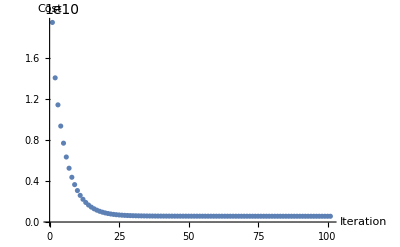

```mathematica
α = 0.1;

θ = Table[RandomReal[{-1,1}],{n+1},{ny}];


Print["J(θ) = ",cost[θVars]];
Print["∂/(∂θ)J(θ) = ",MatrixForm[dCost[θVars]]];
Print[];
Print[];


costList ={cost[θ]};
Print["θ= ",MatrixForm[θ],"     J(θ) = ",cost[θ],"      ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[dCost[θ]]];
Print["θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[θ]," - ",α,MatrixForm[dCost[θ]]," = ",MatrixForm[θ-α dCost[θ]]];
Print[];
Print["________________________"];

Do[

θ= θ-α dCost[θ];
AppendTo[costList,cost[θ]];
,{i,1,100}];
Print["Final values of θ: θ = ",MatrixForm[θ],"  which has cost J(θ) = ",cost[θ]];
Print[ListPlot[costList,AxesLabel->{"Iteration","Cost"},PlotRange->All]];
```

```mathematica
(*Prep for testing data*)
```

```mathematica
(*Question 3-Import Test Data*)TestData=Import["C:\\Users\\dylan\\Downloads\\archive\\test.csv"];

testRows=Drop[TestData,1];

Print["Number of test houses: ",Length[testRows]];
Print["First 5 test houses: ",MatrixForm[Take[testRows,5]]];
```

Number of test houses: 1459

First 5 test houses: (1461 | 20 | RH | 80 | 11622 | Pave | NA | Reg | Lvl | AllPub | Inside | Gtl | NAmes | Feedr | Norm | 1Fam | 1Story | 5 | 6 | 1961 | 1961 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | CBlock | TA | TA | No | Rec | 468 | LwQ | 144 | 270 | 882 | GasA | TA | Y | SBrkr | 896 | 0 | 0 | 896 | 0 | 0 | 1 | 0 | 2 | 1 | TA | 5 | Typ | 0 | NA | Attchd | 1961 | Unf | 1 | 730 | TA | TA | Y | 140 | 0 | 0 | 0 | 120 | 0 | NA | MnPrv | NA | 0 | 6 | 2010 | WD | Normal
1462 | 20 | RL | 81 | 14267 | Pave | NA | IR1 | Lvl | AllPub | Corner | Gtl | NAmes | Norm | Norm | 1Fam | 1Story | 6 | 6 | 1958 | 1958 | Hip | CompShg | Wd Sdng | Wd Sdng | BrkFace | 108 | TA | TA | CBlock | TA | TA | No | ALQ | 923 | Unf | 0 | 406 | 1329 | GasA | TA | Y | SBrkr | 1329 | 0 | 0 | 1329 | 0 | 0 | 1 | 1 | 3 | 1 | Gd | 6 | Typ | 0 | NA | Attchd | 1958 | Unf | 1 | 312 | TA | TA | Y | 393 | 36 | 0 | 0 | 0 | 0 | NA | NA | Gar2 | 12500 | 6 | 2010 | WD | Normal
1463 | 60 | RL | 74 | 13830 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | Gilbert | Norm | Norm | 1Fam | 2Story | 5 | 5 | 1997 | 1998 | Gable | CompShg | VinylSd | VinylSd | None | 0 | TA | TA | PConc | Gd | TA | No | GLQ | 791 | Unf | 0 | 137 | 928 | GasA | Gd | Y | SBrkr | 928 | 701 | 0 | 1629 | 0 | 0 | 2 | 1 | 3 | 1 | TA | 6 | Typ | 1 | TA | Attchd | 1997 | Fin | 2 | 482 | TA | TA | Y | 212 | 34 | 0 | 0 | 0 | 0 | NA | MnPrv | NA | 0 | 3 | 2010 | WD | Normal
1464 | 60 | RL | 78 | 9978 | Pave | NA | IR1 | Lvl | AllPub | Inside | Gtl | Gilbert | Norm | Norm | 1Fam | 2Story | 6 | 6 | 1998 | 1998 | Gable | CompShg | VinylSd | VinylSd | BrkFace | 20 | TA | TA | PConc | TA | TA | No | GLQ | 602 | Unf | 0 | 324 | 926 | GasA | Ex | Y | SBrkr | 926 | 678 | 0 | 1604 | 0 | 0 | 2 | 1 | 3 | 1 | Gd | 7 | Typ | 1 | Gd | Attchd | 1998 | Fin | 2 | 470 | TA | TA | Y | 360 | 36 | 0 | 0 | 0 | 0 | NA | NA | NA | 0 | 6 | 2010 | WD | Normal
1465 | 120 | RL | 43 | 5005 | Pave | NA | IR1 | HLS | AllPub | Inside | Gtl | StoneBr | Norm | Norm | TwnhsE | 1Story | 8 | 5 | 1992 | 1992 | Gable | CompShg | HdBoard | HdBoard | None | 0 | Gd | TA | PConc | Gd | TA | No | ALQ | 263 | Unf | 0 | 1017 | 1280 | GasA | Ex | Y | SBrkr | 1280 | 0 | 0 | 1280 | 0 | 0 | 2 | 0 | 2 | 1 | Gd | 5 | Typ | 0 | NA | Attchd | 1992 | RFn | 2 | 506 | TA | TA | Y | 0 | 82 | 0 | 0 | 144 | 0 | NA | NA | NA | 0 | 1 | 2010 | WD | Normal)

```mathematica
Print["Theta dimensions: ",Dimensions[θ]];
Print["Means dimensions: ",Dimensions[means]];
Print["Stds dimensions: ",Dimensions[stds]];
```

Theta dimensions: {36,1}

Means dimensions: {35}

Stds dimensions: {35}

```mathematica
(*Use the trained theta values from Question 2*)(*Do not generate random theta values again*)ny=Dimensions[θ][[2]];

Print["θ = ",MatrixForm[θ],"
     = ",θ];

Print["

  xTest^(1) = ",xTest[[1]]];

Print["

  xTest^(1) θ = ",MatrixForm[{xTest[[1]]}],MatrixForm[θ]," = ",xTest[[1]].θ];

θNames=Table[Subscript["θ",ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];

θVars=Table[ToExpression["θ"<>ToString[i]<>ToString[j]],{i,0,n},{j,1,ny}];

θVarsInput=Table[ToExpression["θ"<>ToString[i]<>ToString[j]<>"_"],{i,0,n},{j,1,ny}];

Print["

  stick with our indexing for labelling for the θ matrix:"];

Print["θ = ",MatrixForm[θ],"   θNames = ",MatrixForm[θNames],"   θVars = ",MatrixForm[θVars]];

Print["θVarsInput = ",θVarsInput];
```

θ = (180916.
-6267.09
-835.366
4755.11
18829.4
4551.33
3418.06
-281.295
5745.71
1140.1
-886.181
-4758.75
8263.22
3311.83
1185.97
7084.79
-4608.2
17837.8
612.338
5521.09
-4672.51
-2440.54
11697.3
4369.13
51.3237
7931.74
3459.57
3251.85
-550.691
201.703
899.086
2933.96
-525.115
31.9126
-153.838
-984.197)
     = {{180916.},{-6267.09},{-835.366},{4755.11},{18829.4},{4551.33},{3418.06},{-281.295},{5745.71},{1140.1},{-886.181},{-4758.75},{8263.22},{3311.83},{1185.97},{7084.79},{-4608.2},{17837.8},{612.338},{5521.09},{-4672.51},{-2440.54},{11697.3},{4369.13},{51.3237},{7931.74},{3459.57},{3251.85},{-550.691},{201.703},{899.086},{2933.96},{-525.115},{31.9126},{-153.838},{-984.197}}

xTest^(1) = {1.,√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2),-3.1601,2 √(532535/212216581346179) (-15354569/1460+(1613551 √(1459/77459052191355335))/2),2 √(106507/814855) (-1781/292-(321 √(1459/59484415))/2),1/11 √(106507/1090) (-407/73+(31 √(1459/79570))/11),2/3 √(532535/215905171) (-2878051/1460-(4997 √(1459/78805387415))/2),1/2 √(532535/56745974) (-724476/365-(8711 √(1459/20712280510))/2),-0.577394,1/3 √(532535/12308982539) (-323857/730+(17783 √(1459/4492778626735))/6),1/3 √(532535/1539849081) (-33981/730+(23713 √(1459/562044914565))/2),2 √(532535/415902179659) (-828171/1460-(433971 √(1459/151804295575535))/2),√(532535/175629) (-2479/730-(289 √(1459/64104585))/2),1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22),√(532535/490274) (-1513/365-209 √(2918/89475005)),2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2),2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2),2 √(532535/1438301604899) (-3747891/1460-(1152011 √(1459/524980085788135))/2),2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2),-4.77722,2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2),√(532535/25854) (-382/365-17 √(1459/9436710)),√(532535/1406906) (-2379/365-277 √(2918/256760345)),2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2),-82.4868,√(106507/59482) (-129/73-28 √(2918/2171093)),2 √(532535/97374046539) (-690551/1460+(17869 √(30639/1692453666035))/2),2/3 √(532535/3718233539) (-137597/1460+(66803 √(1459/1357155241735))/6),1/4 √(532535/146109671) (-17031/365-(17031 √(1459/53330029915))/4),2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2),√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2),2 √(532535/6622369579) (-21989/1460+(439 √(509191/6925973915))/2),√(532535/859626514) (-1007/365-1007 √(1459/313763677610)),√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2),√(106507/778523) (-923/146-(47 √(1459/56832179))/2),2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2)}

xTest^(1) θ = (1. | √(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2) | -3.1601 | 2 √(532535/212216581346179) (-15354569/1460+(1613551 √(1459/77459052191355335))/2) | 2 √(106507/814855) (-1781/292-(321 √(1459/59484415))/2) | 1/11 √(106507/1090) (-407/73+(31 √(1459/79570))/11) | 2/3 √(532535/215905171) (-2878051/1460-(4997 √(1459/78805387415))/2) | 1/2 √(532535/56745974) (-724476/365-(8711 √(1459/20712280510))/2) | -0.577394 | 1/3 √(532535/12308982539) (-323857/730+(17783 √(1459/4492778626735))/6) | 1/3 √(532535/1539849081) (-33981/730+(23713 √(1459/562044914565))/2) | 2 √(532535/415902179659) (-828171/1460-(433971 √(1459/151804295575535))/2) | √(532535/175629) (-2479/730-(289 √(1459/64104585))/2) | 1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22) | √(532535/490274) (-1513/365-209 √(2918/89475005)) | 2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2) | 2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2) | 2 √(532535/1438301604899) (-3747891/1460-(1152011 √(1459/524980085788135))/2) | 2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2) | -4.77722 | 2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2) | √(532535/25854) (-382/365-17 √(1459/9436710)) | √(532535/1406906) (-2379/365-277 √(2918/256760345)) | 2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2) | -82.4868 | √(106507/59482) (-129/73-28 √(2918/2171093)) | 2 √(532535/97374046539) (-690551/1460+(17869 √(30639/1692453666035))/2) | 2/3 √(532535/3718233539) (-137597/1460+(66803 √(1459/1357155241735))/6) | 1/4 √(532535/146109671) (-17031/365-(17031 √(1459/53330029915))/4) | 2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2) | √(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2) | 2 √(532535/6622369579) (-21989/1460+(439 √(509191/6925973915))/2) | √(532535/859626514) (-1007/365-1007 √(1459/313763677610)) | √(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2) | √(106507/778523) (-923/146-(47 √(1459/56832179))/2) | 2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))(180916.
-6267.09
-835.366
4755.11
18829.4
4551.33
3418.06
-281.295
5745.71
1140.1
-886.181
-4758.75
8263.22
3311.83
1185.97
7084.79
-4608.2
17837.8
612.338
5521.09
-4672.51
-2440.54
11697.3
4369.13
51.3237
7931.74
3459.57
3251.85
-550.691
201.703
899.086
2933.96
-525.115
31.9126
-153.838
-984.197) = {1.1004×10^6}

stick with our indexing for labelling for the θ matrix:

θ = (180916.
-6267.09
-835.366
4755.11
18829.4
4551.33
3418.06
-281.295
5745.71
1140.1
-886.181
-4758.75
8263.22
3311.83
1185.97
7084.79
-4608.2
17837.8
612.338
5521.09
-4672.51
-2440.54
11697.3
4369.13
51.3237
7931.74
3459.57
3251.85
-550.691
201.703
899.086
2933.96
-525.115
31.9126
-153.838
-984.197)   θNames = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)   θVars = (θ01
θ11
θ21
θ31
θ41
θ51
θ61
θ71
θ81
θ91
θ101
θ111
θ121
θ131
θ141
θ151
θ161
θ171
θ181
θ191
θ201
θ211
θ221
θ231
θ241
θ251
θ261
θ271
θ281
θ291
θ301
θ311
θ321
θ331
θ341
θ351)

θVarsInput = {{θ01_},{θ11_},{θ21_},{θ31_},{θ41_},{θ51_},{θ61_},{θ71_},{θ81_},{θ91_},{θ101_},{θ111_},{θ121_},{θ131_},{θ141_},{θ151_},{θ161_},{θ171_},{θ181_},{θ191_},{θ201_},{θ211_},{θ221_},{θ231_},{θ241_},{θ251_},{θ261_},{θ271_},{θ281_},{θ291_},{θ301_},{θ311_},{θ321_},{θ331_},{θ341_},{θ351_}}

```mathematica
(*normalisation*)
xFeaturesTest=xTest[[All,2;;-1]];
xScaledTest=Prepend[#,1.0]&/@((#-means)/stds&/@xFeaturesTest);
xTest=xScaledTest;
```

```mathematica
(*Keep the trained theta values from Question 2*)
ClearAll[h,o,e,cost,dCost];

(*Define model:h using the trained parameters:θ*)
h[x_]:=x.θ;

(*Use hypothesis to make predictions*)
(*h/@xTest is a neater way of writing the same thing!*)
o=Map[h,xTest];
(*Display Basic Info.*)
Print["θ = ",MatrixForm[θ]];

Print["Showing only first 10:
     xTest:",MatrixForm[Prepend[Take[xTest,10],xNames]]," Predicted Prices:",MatrixForm[Take[o,10]]];
```

θ = (180916.
-6267.09
-835.366
4755.11
18829.4
4551.33
3418.06
-281.295
5745.71
1140.1
-886.181
-4758.75
8263.22
3311.83
1185.97
7084.79
-4608.2
17837.8
612.338
5521.09
-4672.51
-2440.54
11697.3
4369.13
51.3237
7931.74
3459.57
3251.85
-550.691
201.703
899.086
2933.96
-525.115
31.9126
-153.838
-984.197)

Showing only first 10:
     xTest:(x_0 | x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8 | x_9 | x_10 | x_11 | x_12 | x_13 | x_14 | x_15 | x_16 | x_17 | x_18 | x_19 | x_20 | x_21 | x_22 | x_23 | x_24 | x_25 | x_26 | x_27 | x_28 | x_29 | x_30 | x_31 | x_32 | x_33 | x_34 | x_35
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2)) | -3.3241 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460+(1613551 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(321 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73+(31 √(1459/79570))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460-(4997 √(1459/78805387415))/2)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365-(8711 √(1459/20712280510))/2)) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(17783 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730+(23713 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(433971 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-209 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(1152011 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -8.89718 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-277 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2)) | -85.8941 | √(106507/59482) (-129/73+√(106507/59482) (-129/73-28 √(2918/2171093))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460+(17869 √(30639/1692453666035))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(66803 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(17031 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460+(439 √(509191/6925973915))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(47 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2)) | -3.32401 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460+(5475251 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(29 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73+(31 √(1459/79570))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460-(6457 √(1459/78805387415))/2)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365-4903 √(1459/20712280510))) | -0.577393 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(349933 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(235411 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-209 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460+(713 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460+(132789 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -7.86514 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-189 √(1459/513520690))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2)) | -85.8943 | √(106507/59482) (-129/73+√(106507/59482) (-129/73-28 √(2918/2171093))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460-(235031 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(436183 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(3891 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730+(9093253 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(47 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146+(151 √(4377/4637375005))/2)) | -3.32466 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460+(4837231 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(321 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(12523 √(1459/78805387415))/2)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+2397 √(1459/20712280510))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(253573 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(628151 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-53 √(1459/178950010))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(14671 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -5.80104 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-189 √(1459/513520690))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292+(113 √(1459/12925015))/2)) | -85.8915 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460+(13169 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(171923 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(4621 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(485 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146+(151 √(4377/4637375005))/2)) | -3.32429 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(786689 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(29 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73+(31 √(1459/79570))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(39029 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+2397 √(1459/20712280510))) | -0.577408 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(115603 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(355131 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365+156 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460+(713 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(54091 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -5.80104 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365+88 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292+(113 √(1459/12925015))/2)) | -85.8914 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460-(4351 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(388003 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(3891 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(47 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146+(3071 √(4377/4637375005))/2)) | -3.32756 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(8047269 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292+(111 √(7295/11896883))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(30269 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+651 √(2918/10356140255))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730-(131867 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460+(656649 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730+(147 √(4377/21368195))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365+156 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460+(713 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(10291 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -6.83309 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-277 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2)) | -85.8918 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460+(6887 √(10213/5077360998105))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460-(137597 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365+(12899 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460+(26893 √(10213/345309270905))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(777 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146+(151 √(4377/4637375005))/2)) | -3.32457 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(754569 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(29 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(31729 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+1667 √(1459/20712280510))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730-(323857 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460+(285809 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-53 √(1459/178950010))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(217611 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -5.80104 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365+88 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292+(113 √(1459/12925015))/2)) | -85.8918 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460-(48151 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(30541 √(1459/1357155241735))/2)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365+(13629 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(339 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2)) | -3.32503 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(3703769 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(29 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73+(52 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(30269 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+(8079 √(1459/20712280510))/2)) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(358693 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(487991 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365+156 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(309591 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -4.76899 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-189 √(1459/513520690))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2)) | -85.8918 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460-(77351 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(567583 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(4683 √(1459/53330029915))/2)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730+(333253 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(485 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146+(151 √(4377/4637375005))/2)) | -3.32569 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(3087649 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(29 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(39029 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+2397 √(1459/20712280510))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730-(323857 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460+(323769 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-53 √(1459/178950010))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(457051 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -5.80104 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292+(39 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365+88 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292+(113 √(1459/12925015))/2)) | -85.8914 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460-(116771 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460-(137597 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365+2586 √(1459/53330029915))) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(193 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2)) | -3.32363 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(497609 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292+(263 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460+(27349 √(1459/78805387415))/6)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365+937 √(1459/20712280510))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(47051 √(1459/4492778626735))/2)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730-(11327 √(1459/562044914565))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460+(4821 √(42311/5234630881915))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730+(373 √(1459/25185))/154)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-53 √(1459/178950010))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460+(713 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460+(107969 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -5.80104 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-277 √(2918/256760345))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292+(113 √(1459/12925015))/2)) | -85.892 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460+(6887 √(10213/5077360998105))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(142723 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(17031 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(631 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))
1. | √(106507/190577055) (-8307/146+√(106507/190577055) (-8307/146-(5387 √(1459/13912125015))/2)) | -3.32504 | 2 √(532535/212216581346179) (-15354569/1460+2 √(532535/212216581346179) (-15354569/1460-(3090569 √(1459/77459052191355335))/2)) | 2 √(106507/814855) (-1781/292+2 √(106507/814855) (-1781/292-(613 √(1459/59484415))/2)) | 1/11 √(106507/1090) (-407/73+1/11 √(106507/1090) (-407/73-(21 √(2918/39785))/11)) | 2/3 √(532535/215905171) (-2878051/1460+2/3 √(532535/215905171) (-2878051/1460-(617 √(1459/78805387415))/2)) | 1/2 √(532535/56745974) (-724476/365+1/2 √(532535/56745974) (-724476/365-2713 √(1459/20712280510))) | -0.577411 | 1/3 √(532535/12308982539) (-323857/730+1/3 √(532535/12308982539) (-323857/730+(263063 √(1459/4492778626735))/6)) | 1/3 √(532535/1539849081) (-33981/730+1/3 √(532535/1539849081) (-33981/730+(2551 √(4377/187348304855))/2)) | 2 √(532535/415902179659) (-828171/1460+2 √(532535/415902179659) (-828171/1460-(828171 √(1459/151804295575535))/2)) | √(532535/175629) (-2479/730+√(532535/175629) (-2479/730-(289 √(1459/64104585))/2)) | 1/77 √(532535/69) (-2547/730+1/77 √(532535/69) (-2547/730-(17 √(4377/8395))/22)) | √(532535/490274) (-1513/365+√(532535/490274) (-1513/365-209 √(2918/89475005))) | 2 √(532535/938491) (-5127/1460+2 √(532535/938491) (-5127/1460-(747 √(1459/342549215))/2)) | 2 √(532535/1113171) (-4103/1460+2 √(532535/1113171) (-4103/1460+(277 √(1459/406307415))/2)) | 2 √(532535/1438301604899) (-3747891/1460+2 √(532535/1438301604899) (-3747891/1460-(1172451 √(1459/524980085788135))/2)) | 2 √(532535/5036085611) (-8533/1460+2 √(532535/5036085611) (-8533/1460-(8533 √(1459/1838171248015))/2)) | -6.83309 | 2 √(106507/283519) (-837/292+2 √(106507/283519) (-837/292-(253 √(1459/20696887))/2)) | √(532535/25854) (-382/365+√(532535/25854) (-382/365-17 √(1459/9436710))) | √(532535/1406906) (-2379/365+√(532535/1406906) (-2379/365-919 √(1459/513520690))) | 2 √(106507/177055) (-179/292+2 √(106507/177055) (-179/292-(179 √(1459/12925015))/2)) | -85.8934 | √(106507/59482) (-129/73+√(106507/59482) (-129/73+17 √(1459/4342186))) | 2 √(532535/97374046539) (-690551/1460+2 √(532535/97374046539) (-690551/1460+(75949 √(1459/35541526986735))/2)) | 2/3 √(532535/3718233539) (-137597/1460+2/3 √(532535/3718233539) (-137597/1460+(212803 √(1459/1357155241735))/6)) | 1/4 √(532535/146109671) (-17031/365+1/4 √(532535/146109671) (-17031/365-(17031 √(1459/53330029915))/4)) | 2 √(532535/7957245171) (-32053/1460+2 √(532535/7957245171) (-32053/1460-(32053 √(1459/2904394487415))/2)) | √(532535/457716959) (-2489/730+√(532535/457716959) (-2489/730-(2489 √(1459/167066690035))/2)) | 2 √(532535/6622369579) (-21989/1460+2 √(532535/6622369579) (-21989/1460-(21989 √(1459/2417164896335))/2)) | √(532535/859626514) (-1007/365+√(532535/859626514) (-1007/365-1007 √(1459/313763677610))) | √(532535/131077129331) (-31747/730+√(532535/131077129331) (-31747/730-(31747 √(1459/47843152205815))/2)) | √(106507/778523) (-923/146+√(106507/778523) (-923/146-(339 √(1459/56832179))/2)) | 2 √(532535/3757219) (-2931411/1460+2 √(532535/3757219) (-2931411/1460+(3189 √(1459/1371384935))/2))) Predicted Prices:(1.98214×10^6
2.01329×10^6
2.03164×10^6
2.06541×10^6
2.10608×10^6
2.04147×10^6
2.0361×10^6
2.04147×10^6
2.076×10^6
1.99941×10^6)

```mathematica
ClearAll[h,o,e,θ,cost,dCost];

(* Define model:h  but don't set initial values for paramters: θ *)
θ = θVars;
h[x_] := x.θ;


(* Use hypothesis to make predictions & define error vector e *)
o = Map[h,x];  
e = o-y;

(* Define the cost function and it's gradient *)
cost[θVarsInput] =  Expand[Simplify[N[     1/(2 Times@@Dimensions[y])Total[Flatten[    (   h/@x - y  )^2     ]]       ]]];

dCost[θVarsInput] = Expand[Simplify[N[        Grad[cost[θVars],#]& /@ θVars     ]]];



Print["To find the cost & gradient functions we first leave the values of θ unassigned:

θ = ",MatrixForm[θNames]];

Print["
We then find the cost function using our training data, model and loss function:

J(θ) = ",cost[θNames]
];
Print["
We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = ",MatrixForm[dCost[θNames]]
];

Print[];
Print["Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example: "];
Print[];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];

θ = Table[RandomReal[{-5,5}],{n+1},{ny}];
Print["θ = ",MatrixForm[θ]," then   J(θ) = ",cost[θ],"   &   ∇_θ J(θ) = ",MatrixForm[  dCost[θ]  ]];
Print["_________________________________
"];
```

To find the cost & gradient functions we first leave the values of θ unassigned:

θ = (θ_01
θ_11
θ_21
θ_31
θ_41
θ_51
θ_61
θ_71
θ_81
θ_91
θ_101
θ_111
θ_121
θ_131
θ_141
θ_151
θ_161
θ_171
θ_181
θ_191
θ_201
θ_211
θ_221
θ_231
θ_241
θ_251
θ_261
θ_271
θ_281
θ_291
θ_301
θ_311
θ_321
θ_331
θ_341
θ_351)

We then find the cost function using our training data, model and loss function:

J(θ) = 1.95196×10^10-180921. θ_01+0.5 θ_01^2+903.287 θ_101-2.92004×10^-17 θ_01 θ_101+0.499658 θ_101^2+6691.16 θ_11-1.94669×10^-17 θ_01 θ_11-0.0656036 θ_101 θ_11+0.499658 θ_11^2-17027.1 θ_111+3.89338×10^-17 θ_01 θ_111-0.209151 θ_101 θ_111-0.140663 θ_11 θ_111+0.499658 θ_111^2-54193.4 θ_121-1.94669×10^-17 θ_01 θ_121-0.076184 θ_101 θ_121+0.0161667 θ_11 θ_121+0.28451 θ_111 θ_121+0.499658 θ_121^2-46458.5 θ_131-0.0309698 θ_101 θ_131+0.051087 θ_11 θ_131+0.256982 θ_111 θ_131+0.565171 θ_121 θ_131+0.499658 θ_131^2-33950.2 θ_141-1.46002×10^-17 θ_01 θ_141-0.074484 θ_101 θ_141-0.0194442 θ_11 θ_141+0.202422 θ_111 θ_141+0.51967 θ_121 θ_141+0.396897 θ_131 θ_141+0.499658 θ_141^2-52364.4 θ_151-2.92004×10^-17 θ_01 θ_151-0.0450599 θ_101 θ_151-0.0123741 θ_11 θ_151+0.210081 θ_111 θ_151+0.715632 θ_121 θ_151+0.510588 θ_131 θ_151+0.503883 θ_141 θ_151+0.499658 θ_151^2-21739.6 θ_161-9.73346×10^-18 θ_01 θ_161+0.052761 θ_101 θ_161-0.0728959 θ_11 θ_161+0.0111064 θ_111 θ_161+0.218873 θ_121 θ_161+0.182111 θ_131 θ_161+0.145378 θ_141 θ_161+0.237991 θ_151 θ_161+0.499658 θ_161^2-62102.1 θ_171+9.73346×10^-18 θ_01 θ_171+0.0488825 θ_101 θ_171-0.0821683 θ_11 θ_171+0.373477 θ_111 θ_171+0.533414 θ_121 θ_171+0.513947 θ_131 θ_171+0.306354 θ_141 θ_171+0.502394 θ_151 θ_171+0.20553 θ_161 θ_171+0.499658 θ_171^2+2032.82 θ_181+9.73346×10^-18 θ_01 θ_181+0.0147969 θ_101 θ_181+0.0464419 θ_11 θ_181+0.0281474 θ_111 θ_181-0.0630184 θ_121 θ_181-0.0557367 θ_131 θ_181-0.0316824 θ_141 θ_181-0.047535 θ_151 θ_181-0.114463 θ_161 θ_181+0.00920026 θ_171 θ_181+0.499658 θ_181^2-50151.9 θ_191+2.72537×10^-16 θ_01 θ_191+0.0516731 θ_101 θ_191+0.150944 θ_11 θ_191-0.104425 θ_111 θ_191+0.474952 θ_121 θ_191+0.479204 θ_131 θ_191+0.319793 θ_141 θ_191+0.464669 θ_151 θ_191+0.177144 θ_161 θ_191+0.60391 θ_171 θ_191-0.0411745 θ_181 θ_191+0.499658 θ_191^2-13354.1 θ_201-1.46002×10^-17 θ_01 θ_201-0.0157173 θ_101 θ_201-0.023422 θ_11 θ_201+0.166529 θ_111 θ_201-0.0187158 θ_121 θ_201-0.0398853 θ_131 θ_201-0.0268507 θ_141 θ_201-0.0179992 θ_151 θ_201-0.0046418 θ_161 θ_201+0.353791 θ_171 θ_201+0.105534 θ_181 θ_201+0.234725 θ_191 θ_201+0.499658 θ_201^2-26587.1 θ_21+4.08805×10^-16 θ_01 θ_21+0.0433099 θ_101 θ_21-0.356811 θ_11 θ_21+0.122072 θ_111 θ_21+0.164939 θ_121 θ_21+0.1417 θ_131 θ_21+0.0888949 θ_141 θ_21+0.169273 θ_151 θ_21+0.10849 θ_161 θ_21+0.427104 θ_171 θ_21+0.0368235 θ_181 θ_21+0.201335 θ_191 θ_21+0.236861 θ_201 θ_21+0.499658 θ_21^2+10789.4 θ_211-3.89338×10^-17 θ_01 θ_211-0.0407233 θ_101 θ_211+0.281528 θ_11 θ_211+0.0300653 θ_111 θ_211-0.151132 θ_121 θ_211-0.277541 θ_131 θ_211-0.171299 θ_141 θ_211-0.172305 θ_151 θ_211-0.163829 θ_161 θ_211+0.0267409 θ_171 θ_211+0.00751659 θ_181 θ_211+0.0383051 θ_191 θ_211+0.198461 θ_201 θ_211-0.00580063 θ_21 θ_211+0.499658 θ_211^2-42371.3 θ_221+4.86673×10^-18 θ_01 θ_221-0.0352024 θ_101 θ_221+0.0403524 θ_11 θ_221+0.250475 θ_111 θ_221+0.297699 θ_121 θ_221+0.185719 θ_131 θ_221+0.164791 θ_141 θ_221+0.287082 θ_151 θ_221+0.0911885 θ_161 θ_221+0.672136 θ_171 θ_221+0.131095 θ_181 θ_221+0.459958 θ_191 θ_221+0.676156 θ_201 θ_221+0.319927 θ_21 θ_221+0.25587 θ_211 θ_221+0.499658 θ_221^2-37068.6 θ_231+0.0468886 θ_101 θ_231-0.0455381 θ_11 θ_231+0.0515396 θ_111 θ_231+0.249164 θ_121 θ_231+0.229478 θ_131 θ_231+0.1296 θ_141 θ_231+0.256233 θ_151 θ_231+0.208414 θ_161 θ_231+0.477438 θ_171 θ_231-0.0212576 θ_181 θ_231+0.331425 θ_191 θ_231+0.107496 θ_201 θ_231+0.235593 θ_21 θ_231-0.123851 θ_211 θ_231+0.325891 θ_221 θ_231+0.499658 θ_231^2-37326.5 θ_241+3.94205×10^-15 θ_01 θ_241-0.0870667 θ_101 θ_241+0.0801323 θ_11 θ_241+0.185971 θ_111 θ_241+0.56662 θ_121 θ_241+0.542945 θ_131 θ_241+0.457111 θ_141 θ_241+0.50277 θ_151 θ_241+0.102952 θ_161 θ_241+0.309879 θ_171 θ_241-0.029147 θ_181 θ_241+0.457264 θ_191 θ_241-0.0602152 θ_201 θ_241+0.0642801 θ_21 θ_241-0.107506 θ_211 θ_241+0.140695 θ_221 θ_241+0.0455652 θ_231 θ_241+0.499658 θ_241^2-50840.9 θ_251+1.94669×10^-17 θ_01 θ_251-0.0382373 θ_101 θ_251-0.0400823 θ_11 θ_251+0.214028 θ_111 θ_251+0.52603 θ_121 θ_251+0.448887 θ_131 θ_251+0.325124 θ_141 θ_251+0.50946 θ_151 θ_251+0.576227 θ_161 θ_251+0.536045 θ_171 θ_251-0.0944148 θ_181 θ_251+0.483246 θ_191 θ_251+0.0860475 θ_201 θ_251+0.269544 θ_21 θ_251-0.0505992 θ_211 θ_251+0.36204 θ_221 θ_251+0.300583 θ_231 θ_251+0.482204 θ_241 θ_251+0.499658 θ_251^2-49493. θ_261+1.94669×10^-17 θ_01 θ_261-0.0182141 θ_101 θ_261-0.098604 θ_11 θ_261+0.183177 θ_111 θ_261+0.495438 θ_121 θ_261+0.405831 θ_131 θ_261+0.29526 θ_141 θ_261+0.48927 θ_151 θ_261+0.558555 θ_161 θ_261+0.56336 θ_171 θ_261-0.0675551 θ_181 θ_261+0.451258 θ_191 θ_261+0.0652078 θ_201 θ_261+0.323441 θ_21 θ_261-0.0643889 θ_211 θ_261+0.337591 θ_221 θ_261+0.268957 θ_231 θ_261+0.476172 θ_241 θ_261+0.881871 θ_251 θ_261+0.499658 θ_261^2-25754.6 θ_271+1.94669×10^-17 θ_01 θ_271+0.0678518 θ_101 θ_271-0.0125707 θ_11 θ_271-0.00531278 θ_111 θ_271+0.20779 θ_121 θ_271+0.252529 θ_131 θ_271+0.130771 θ_141 θ_271+0.22094 θ_151 θ_271+0.119481 θ_161 θ_271+0.283415 θ_171 θ_271-0.0254262 θ_181 θ_271+0.288003 θ_191 θ_271+0.0468217 θ_201 θ_271+0.0770534 θ_21 θ_271-0.0900685 θ_211 θ_271+0.16587 θ_221 θ_271+0.199882 θ_231 θ_271+0.220472 θ_241 θ_271+0.226187 θ_251 θ_271+0.224512 θ_261 θ_271+0.499658 θ_271^2-25075.2 θ_281-2.19003×10^-17 θ_01 θ_281+0.00309044 θ_101 θ_281-0.00609594 θ_11 θ_281+0.128917 θ_111 θ_281+0.291353 θ_121 θ_281+0.253825 θ_131 θ_281+0.175368 θ_141 θ_281+0.259076 θ_151 θ_281+0.0623907 θ_161 θ_281+0.341873 θ_171 θ_281+0.0182385 θ_181 θ_281+0.286753 θ_191 θ_281+0.0937453 θ_201 θ_281+0.13736 θ_21 θ_281-0.0700426 θ_211 θ_281+0.234031 θ_221 θ_281+0.169289 θ_231 θ_281+0.21834 θ_241 θ_281+0.213423 θ_251 θ_281+0.241269 θ_261 θ_281+0.0586204 θ_271 θ_281+0.499658 θ_281^2+10207.6 θ_291-9.73346×10^-18 θ_01 θ_291+0.0365183 θ_101 θ_291-0.0120284 θ_11 θ_291-0.00253612 θ_111 θ_291-0.149486 θ_121 θ_291-0.181408 θ_131 θ_291-0.101673 θ_141 θ_291-0.105786 θ_151 θ_291-0.0947604 θ_161 θ_291-0.0487277 θ_171 θ_291+0.0610394 θ_181 θ_291-0.145423 θ_191 θ_291+0.041542 θ_201 θ_291+0.00978336 θ_21 θ_291+0.0372868 θ_211 θ_291+0.00414846 θ_221 θ_291-0.0248049 θ_231 θ_291-0.285686 θ_241 θ_291-0.15133 θ_251 θ_291-0.121693 θ_261 θ_291-0.125903 θ_271 θ_291-0.0930156 θ_281 θ_291+0.499658 θ_291^2-3539.41 θ_301-2.43337×10^-18 θ_01 θ_301-0.0299729 θ_101 θ_301-0.0437945 θ_11 θ_301+0.0207498 θ_111 θ_301+0.0369087 θ_121 θ_301+0.00809127 θ_131 θ_301+0.0596099 θ_141 θ_301+0.0223165 θ_151 θ_301+0.0353707 θ_161 θ_301+0.0333913 θ_171 θ_301-0.00429267 θ_181 θ_301+0.0284538 θ_191 θ_301-0.024461 θ_201 θ_301+0.0622928 θ_21 θ_301-0.0245835 θ_211 θ_301-0.00667866 θ_221 θ_301+0.0112495 θ_231 θ_301+0.0235182 θ_241 θ_301+0.0357408 θ_251 θ_301+0.0350627 θ_261 θ_301-0.0327482 θ_271 θ_301-0.0058385 θ_281 θ_301-0.0372797 θ_291 θ_301+0.499658 θ_301^2-20946. θ_31+9.73346×10^-18 θ_01 θ_31+0.111094 θ_101 θ_31-0.139685 θ_11 θ_31-0.00261657 θ_111 θ_31+0.055532 θ_121 θ_31+0.072286 θ_131 θ_31+0.00357866 θ_141 θ_31+0.067817 θ_151 θ_31+0.0792588 θ_161 θ_31+0.307024 θ_171 θ_31+0.0047757 θ_181 θ_31+0.204624 θ_191 θ_31+0.119608 θ_201 θ_31+0.306584 θ_21 θ_31-0.0177717 θ_211 θ_31+0.189885 θ_221 θ_31+0.271178 θ_231 θ_31-0.0247951 θ_241 θ_31+0.154765 θ_251 θ_31+0.180279 θ_261 θ_31+0.17158 θ_271 θ_31+0.0847157 θ_281 θ_31-0.0183272 θ_291 θ_31+0.0204088 θ_301 θ_31+0.499658 θ_31^2-8847.53 θ_311+9.73346×10^-18 θ_01 θ_311+0.0888104 θ_101 θ_311-0.0260123 θ_11 θ_311-0.0125707 θ_111 θ_311+0.0126795 θ_121 θ_311+0.0343723 θ_131 θ_311-0.034899 θ_141 θ_311+0.030767 θ_151 θ_311+0.0690742 θ_161 θ_311+0.108363 θ_171 θ_311+0.0267811 θ_181 θ_311+0.037651 θ_191 θ_311+0.0442693 θ_201 θ_311+0.0376585 θ_21 θ_311-0.051578 θ_211 θ_311+0.0593419 θ_221 θ_311+0.184404 θ_231 θ_311-0.0752041 θ_241 θ_311+0.0504592 θ_251 θ_311+0.0513765 θ_261 θ_311-0.0741305 θ_271 θ_311+0.0742531 θ_281 θ_311-0.0828075 θ_291 θ_311-0.0314143 θ_301 θ_311+0.0431308 θ_31 θ_311+0.499658 θ_311^2-7335.74 θ_321+7.3001×10^-18 θ_01 θ_321+0.0416805 θ_101 θ_321+0.00827703 θ_11 θ_321-0.0350682 θ_111 θ_321+0.0347424 θ_121 θ_321+0.0263968 θ_131 θ_321-0.0475965 θ_141 θ_321+0.0623109 θ_151 θ_321+0.035426 θ_161 θ_321+0.172347 θ_171 θ_321+0.0621148 θ_181 θ_321+0.0896155 θ_191 θ_321+0.0706542 θ_201 θ_321+0.180744 θ_21 θ_321-0.0145152 θ_211 θ_321+0.0837 θ_221 θ_321+0.0950084 θ_231 θ_321-0.0144887 θ_241 θ_321+0.0209192 θ_251 θ_321+0.0610055 θ_261 θ_321+0.0733279 θ_271 θ_321+0.0607205 θ_281 θ_321+0.0541654 θ_291 θ_321-0.00798608 θ_301 θ_321+0.0776192 θ_31 θ_321+0.0512723 θ_311 θ_321+0.499658 θ_321^2+1682.2 θ_331+2.43337×10^-18 θ_01 θ_331+0.0049364 θ_101 θ_331-0.00767803 θ_11 θ_331-0.0238203 θ_111 θ_331-0.0392829 θ_121 θ_331-0.0443733 θ_131 θ_331-0.026854 θ_141 θ_331-0.0540578 θ_151 θ_331-0.00478118 θ_161 θ_331-0.0111784 θ_171 θ_331-0.00379027 θ_181 θ_331-0.0259395 θ_191 θ_331+0.00776165 θ_201 θ_331+0.00116747 θ_21 θ_331+0.062298 θ_211 θ_331+0.0247459 θ_221 θ_331+0.00140764 θ_231 θ_331-0.0318316 θ_241 θ_331-0.0430506 θ_251 θ_331-0.0273811 θ_261 θ_331-0.00954469 θ_271 θ_331-0.018571 θ_281 θ_331+0.018348 θ_291 θ_331+0.000353723 θ_301 θ_331+0.0380416 θ_31 θ_331+0.0319239 θ_311 θ_331+0.0296483 θ_321 θ_331+0.499658 θ_331^2-3686.17 θ_341-7.3001×10^-18 θ_01 θ_341-0.0152003 θ_101 θ_341-0.0135753 θ_11 θ_341+0.0348645 θ_111 θ_341+0.0427604 θ_121 θ_341+0.0156518 θ_131 θ_341+0.0155127 θ_141 θ_341+0.0517269 θ_151 θ_341+0.0147788 θ_161 θ_341+0.0404576 θ_171 θ_341-0.0221588 θ_181 θ_341+0.0245179 θ_191 θ_341+0.046512 θ_201 θ_341+0.0101508 θ_21 θ_341+0.0265707 θ_211 θ_341+0.0368818 θ_221 θ_341+0.0463254 θ_231 θ_341+0.00516988 θ_241 θ_341+0.040494 θ_251 θ_341+0.0279546 θ_261 θ_341+0.0209967 θ_271 θ_341+0.0712061 θ_281 θ_341-0.0288675 θ_291 θ_341+0.0294536 θ_301 θ_341+0.00120416 θ_31 θ_341+0.0232011 θ_311 θ_341-0.0337135 θ_321 θ_341-0.0064901 θ_331 θ_341+0.499658 θ_341^2+2296.11 θ_351-6.08341×10^-18 θ_01 θ_351+0.0316839 θ_101 θ_351-0.0213924 θ_11 θ_351-0.0412299 θ_111 θ_351-0.00674019 θ_121 θ_351-0.0214462 θ_131 θ_351-0.00964247 θ_141 θ_351+0.00204515 θ_151 θ_351-0.00644662 θ_161 θ_351-0.029618 θ_171 θ_351-0.0289011 θ_181 θ_351+0.0201299 θ_191 θ_351-0.0359892 θ_201 θ_351+0.00676361 θ_21 θ_351+0.0316655 θ_211 θ_351-0.0344927 θ_221 θ_351-0.0240791 θ_231 θ_351-0.000986623 θ_241 θ_351-0.0390901 θ_251 θ_351-0.0273592 θ_261 θ_351+0.0222552 θ_271 θ_351-0.0575799 θ_281 θ_351-0.00990915 θ_291 θ_351+0.0186322 θ_301 θ_351-0.0142516 θ_31 θ_351+0.0106868 θ_311 θ_351-0.059648 θ_321 θ_351+0.0049029 θ_331 θ_351-0.145622 θ_341 θ_351+0.499658 θ_351^2-62794.5 θ_41-9.73346×10^-18 θ_01 θ_41-0.0590782 θ_101 θ_41+0.0326054 θ_11 θ_41+0.307948 θ_111 θ_41+0.725781 θ_121 θ_41+0.628948 θ_131 θ_41+0.456769 θ_141 θ_41+0.67287 θ_151 θ_41+0.292199 θ_161 θ_41+0.667698 θ_171 θ_41-0.0304084 θ_181 θ_41+0.540692 θ_191 θ_41+0.101607 θ_201 θ_41+0.234036 θ_21 θ_41-0.183756 θ_211 θ_41+0.42716 θ_221 θ_41+0.396493 θ_231 θ_41+0.517663 θ_241 θ_41+0.600259 θ_251 θ_41+0.561637 θ_261 θ_41+0.23876 θ_271 θ_41+0.308607 θ_281 θ_41-0.113859 θ_291 θ_41+0.0303498 θ_301 θ_41+0.105733 θ_31 θ_41+0.0648419 θ_311 θ_41+0.0651212 θ_321 θ_41-0.0313847 θ_331 θ_41+0.0707667 θ_341 θ_41-0.027328 θ_351 θ_41+0.499658 θ_41^2+6180.83 θ_51-2.43337×10^-17 θ_01 θ_51+0.0402016 θ_101 θ_51-0.0592752 θ_11 θ_51-0.136747 θ_111 θ_51-0.138847 θ_121 θ_51-0.164883 θ_131 θ_51-0.014095 θ_141 θ_51-0.0266884 θ_151 θ_51+0.0190466 θ_161 θ_51-0.143716 θ_171 θ_51+0.0254769 θ_181 θ_51-0.173913 θ_191 θ_51+0.0129712 θ_201 θ_51-0.0527839 θ_21 θ_51-0.0869413 θ_211 θ_51-0.0575437 θ_221 θ_51-0.0238037 θ_231 θ_51-0.305959 θ_241 θ_51-0.18563 θ_251 θ_51-0.151418 θ_261 θ_51-0.00333142 θ_271 θ_51-0.0325665 θ_281 θ_51+0.070308 θ_291 θ_51+0.0254862 θ_301 θ_51-0.00563241 θ_31 θ_51+0.054773 θ_311 θ_51-0.00198358 θ_321 θ_51+0.0687297 θ_331 θ_51-0.00350843 θ_341 θ_51+0.0439196 θ_351 θ_51-0.0918694 θ_41 θ_51+0.499658 θ_51^2-41511.8 θ_61-0.0490732 θ_101 θ_61+0.0278311 θ_11 θ_61+0.148938 θ_111 θ_61+0.597751 θ_121 θ_61+0.602384 θ_131 θ_61+0.448548 θ_141 θ_61+0.529802 θ_151 θ_61+0.286858 θ_161 θ_61+0.346895 θ_171 θ_61-0.183658 θ_181 θ_61+0.523939 θ_191 θ_61-0.0706028 θ_201 θ_61+0.117517 θ_21 θ_61-0.174681 θ_211 θ_61+0.0955237 θ_221 θ_61+0.147615 θ_231 θ_61+0.78002 θ_241 θ_61+0.537482 θ_251 θ_61+0.478626 θ_261 θ_61+0.224726 θ_271 θ_61+0.188557 θ_281 θ_61-0.387003 θ_291 θ_61+0.031333 θ_301 θ_61+0.0142179 θ_31 θ_61-0.0503299 θ_311 θ_61+0.00494634 θ_321 θ_61-0.0343596 θ_331 θ_61+0.01239 θ_341 θ_61-0.0136084 θ_351 θ_61+0.571931 θ_41 θ_61-0.375726 θ_51 θ_61+0.499658 θ_61^2-40257.8 θ_71-1.46002×10^-17 θ_01 θ_71-0.0677121 θ_101 θ_71+0.0405532 θ_11 θ_71+0.181009 θ_111 θ_71+0.586916 θ_121 θ_71+0.514661 θ_131 θ_71+0.549641 θ_141 θ_71+0.624888 θ_151 θ_71+0.148823 θ_161 θ_71+0.342639 θ_171 θ_71-0.0623763 θ_181 θ_71+0.443415 θ_191 θ_71-0.0405531 θ_201 θ_71+0.0826892 θ_21 θ_71-0.149495 θ_211 θ_71+0.191608 θ_221 θ_71+0.112504 θ_231 θ_71+0.617706 θ_241 θ_71+0.420334 θ_251 θ_71+0.371345 θ_261 θ_71+0.205585 θ_271 θ_71+0.226143 θ_281 θ_71-0.193786 θ_291 θ_71+0.0452548 θ_301 θ_71+0.013779 θ_31 θ_71-0.0387135 θ_311 θ_71+0.00582538 θ_321 θ_71-0.0102792 θ_331 θ_71+0.0214753 θ_341 θ_71+0.0357188 θ_351 θ_71+0.550307 θ_41 θ_71+0.073691 θ_51 θ_71+0.592449 θ_61 θ_71+0.499658 θ_71^2-37728.5 θ_81-3.89338×10^-17 θ_01 θ_81-0.0722527 θ_101 θ_81+0.022879 θ_11 θ_81+0.114105 θ_111 θ_81+0.349397 θ_121 θ_81+0.279383 θ_131 θ_81+0.159147 θ_141 θ_81+0.284995 θ_151 θ_81+0.135802 θ_161 θ_81+0.446624 θ_171 θ_81-0.0690208 θ_181 θ_81+0.317727 θ_191 θ_81+0.102347 θ_201 θ_81+0.179161 θ_21 θ_81-0.0373384 θ_211 θ_81+0.279835 θ_221 θ_81+0.247736 θ_231 θ_81+0.249196 θ_241 θ_81+0.363528 θ_251 θ_81+0.372312 θ_261 θ_81+0.15924 θ_271 θ_81+0.12488 θ_281 θ_81-0.109773 θ_291 θ_81+0.0187819 θ_301 θ_81+0.103889 θ_31 θ_81+0.0614111 θ_311 θ_81+0.0117149 θ_321 θ_81-0.0297943 θ_331 θ_81-0.00593551 θ_341 θ_81-0.00817803 θ_351 θ_81+0.409957 θ_41 θ_81-0.127701 θ_51 θ_81+0.314529 θ_61 θ_81+0.179064 θ_71 θ_81+0.499658 θ_81^2-30677.1 θ_91-0.0500831 θ_101 θ_91-0.0697879 θ_11 θ_91-0.494912 θ_111 θ_91+0.203638 θ_121 θ_91+0.304399 θ_131 θ_91+0.0856134 θ_141 θ_91+0.228258 θ_151 θ_91+0.137044 θ_161 θ_91+0.415558 θ_171 θ_91-0.0644584 θ_181 θ_91+0.481279 θ_191 θ_91-0.107281 θ_201 θ_91+0.215681 θ_21 θ_91-0.0809514 θ_211 θ_91+0.0442853 θ_221 θ_91+0.259833 θ_231 θ_91+0.150235 θ_241 θ_91+0.2239 θ_251 θ_91+0.296767 θ_261 θ_91+0.204166 θ_271 θ_91+0.111684 θ_281 θ_91-0.102233 θ_291 θ_91+0.0264324 θ_301 θ_91+0.213956 θ_31 θ_91+0.0619781 θ_311 θ_91+0.140395 θ_321 θ_91+0.00356903 θ_331 θ_91-0.0157162 θ_341 θ_91+0.0143491 θ_351 θ_91+0.239502 θ_41 θ_91-0.0461992 θ_51 θ_91+0.249332 θ_61 θ_91+0.128363 θ_71 θ_91+0.263402 θ_81 θ_91+0.499658 θ_91^2

We can use Mathematica to find the gradient of this function, ∇_θ J(θ) :

∇_θ J(θ) = ∂/∂θ J(θ) = (-180921.+1. θ_01-2.92004×10^-17 θ_101-1.94669×10^-17 θ_11+3.89338×10^-17 θ_111-1.94669×10^-17 θ_121-1.46002×10^-17 θ_141-2.92004×10^-17 θ_151-9.73346×10^-18 θ_161+9.73346×10^-18 θ_171+9.73346×10^-18 θ_181+2.72537×10^-16 θ_191-1.46002×10^-17 θ_201+4.08805×10^-16 θ_21-3.89338×10^-17 θ_211+4.86673×10^-18 θ_221+3.94205×10^-15 θ_241+1.94669×10^-17 θ_251+1.94669×10^-17 θ_261+1.94669×10^-17 θ_271-2.19003×10^-17 θ_281-9.73346×10^-18 θ_291-2.43337×10^-18 θ_301+9.73346×10^-18 θ_31+9.73346×10^-18 θ_311+7.3001×10^-18 θ_321+2.43337×10^-18 θ_331-7.3001×10^-18 θ_341-6.08341×10^-18 θ_351-9.73346×10^-18 θ_41-2.43337×10^-17 θ_51-1.46002×10^-17 θ_71-3.89338×10^-17 θ_81
6691.16-1.94669×10^-17 θ_01-0.0656036 θ_101+0.999315 θ_11-0.140663 θ_111+0.0161667 θ_121+0.051087 θ_131-0.0194442 θ_141-0.0123741 θ_151-0.0728959 θ_161-0.0821683 θ_171+0.0464419 θ_181+0.150944 θ_191-0.023422 θ_201-0.356811 θ_21+0.281528 θ_211+0.0403524 θ_221-0.0455381 θ_231+0.0801323 θ_241-0.0400823 θ_251-0.098604 θ_261-0.0125707 θ_271-0.00609594 θ_281-0.0120284 θ_291-0.0437945 θ_301-0.139685 θ_31-0.0260123 θ_311+0.00827703 θ_321-0.00767803 θ_331-0.0135753 θ_341-0.0213924 θ_351+0.0326054 θ_41-0.0592752 θ_51+0.0278311 θ_61+0.0405532 θ_71+0.022879 θ_81-0.0697879 θ_91
-26587.1+4.08805×10^-16 θ_01+0.0433099 θ_101-0.356811 θ_11+0.122072 θ_111+0.164939 θ_121+0.1417 θ_131+0.0888949 θ_141+0.169273 θ_151+0.10849 θ_161+0.427104 θ_171+0.0368235 θ_181+0.201335 θ_191+0.236861 θ_201+0.999315 θ_21-0.00580063 θ_211+0.319927 θ_221+0.235593 θ_231+0.0642801 θ_241+0.269544 θ_251+0.323441 θ_261+0.0770534 θ_271+0.13736 θ_281+0.00978336 θ_291+0.0622928 θ_301+0.306584 θ_31+0.0376585 θ_311+0.180744 θ_321+0.00116747 θ_331+0.0101508 θ_341+0.00676361 θ_351+0.234036 θ_41-0.0527839 θ_51+0.117517 θ_61+0.0826892 θ_71+0.179161 θ_81+0.215681 θ_91
-20946.+9.73346×10^-18 θ_01+0.111094 θ_101-0.139685 θ_11-0.00261657 θ_111+0.055532 θ_121+0.072286 θ_131+0.00357866 θ_141+0.067817 θ_151+0.0792588 θ_161+0.307024 θ_171+0.0047757 θ_181+0.204624 θ_191+0.119608 θ_201+0.306584 θ_21-0.0177717 θ_211+0.189885 θ_221+0.271178 θ_231-0.0247951 θ_241+0.154765 θ_251+0.180279 θ_261+0.17158 θ_271+0.0847157 θ_281-0.0183272 θ_291+0.0204088 θ_301+0.999315 θ_31+0.0431308 θ_311+0.0776192 θ_321+0.0380416 θ_331+0.00120416 θ_341-0.0142516 θ_351+0.105733 θ_41-0.00563241 θ_51+0.0142179 θ_61+0.013779 θ_71+0.103889 θ_81+0.213956 θ_91
-62794.5-9.73346×10^-18 θ_01-0.0590782 θ_101+0.0326054 θ_11+0.307948 θ_111+0.725781 θ_121+0.628948 θ_131+0.456769 θ_141+0.67287 θ_151+0.292199 θ_161+0.667698 θ_171-0.0304084 θ_181+0.540692 θ_191+0.101607 θ_201+0.234036 θ_21-0.183756 θ_211+0.42716 θ_221+0.396493 θ_231+0.517663 θ_241+0.600259 θ_251+0.561637 θ_261+0.23876 θ_271+0.308607 θ_281-0.113859 θ_291+0.0303498 θ_301+0.105733 θ_31+0.0648419 θ_311+0.0651212 θ_321-0.0313847 θ_331+0.0707667 θ_341-0.027328 θ_351+0.999315 θ_41-0.0918694 θ_51+0.571931 θ_61+0.550307 θ_71+0.409957 θ_81+0.239502 θ_91
6180.83-2.43337×10^-17 θ_01+0.0402016 θ_101-0.0592752 θ_11-0.136747 θ_111-0.138847 θ_121-0.164883 θ_131-0.014095 θ_141-0.0266884 θ_151+0.0190466 θ_161-0.143716 θ_171+0.0254769 θ_181-0.173913 θ_191+0.0129712 θ_201-0.0527839 θ_21-0.0869413 θ_211-0.0575437 θ_221-0.0238037 θ_231-0.305959 θ_241-0.18563 θ_251-0.151418 θ_261-0.00333142 θ_271-0.0325665 θ_281+0.070308 θ_291+0.0254862 θ_301-0.00563241 θ_31+0.054773 θ_311-0.00198358 θ_321+0.0687297 θ_331-0.00350843 θ_341+0.0439196 θ_351-0.0918694 θ_41+0.999315 θ_51-0.375726 θ_61+0.073691 θ_71-0.127701 θ_81-0.0461992 θ_91
-41511.8-0.0490732 θ_101+0.0278311 θ_11+0.148938 θ_111+0.597751 θ_121+0.602384 θ_131+0.448548 θ_141+0.529802 θ_151+0.286858 θ_161+0.346895 θ_171-0.183658 θ_181+0.523939 θ_191-0.0706028 θ_201+0.117517 θ_21-0.174681 θ_211+0.0955237 θ_221+0.147615 θ_231+0.78002 θ_241+0.537482 θ_251+0.478626 θ_261+0.224726 θ_271+0.188557 θ_281-0.387003 θ_291+0.031333 θ_301+0.0142179 θ_31-0.0503299 θ_311+0.00494634 θ_321-0.0343596 θ_331+0.01239 θ_341-0.0136084 θ_351+0.571931 θ_41-0.375726 θ_51+0.999315 θ_61+0.592449 θ_71+0.314529 θ_81+0.249332 θ_91
-40257.8-1.46002×10^-17 θ_01-0.0677121 θ_101+0.0405532 θ_11+0.181009 θ_111+0.586916 θ_121+0.514661 θ_131+0.549641 θ_141+0.624888 θ_151+0.148823 θ_161+0.342639 θ_171-0.0623763 θ_181+0.443415 θ_191-0.0405531 θ_201+0.0826892 θ_21-0.149495 θ_211+0.191608 θ_221+0.112504 θ_231+0.617706 θ_241+0.420334 θ_251+0.371345 θ_261+0.205585 θ_271+0.226143 θ_281-0.193786 θ_291+0.0452548 θ_301+0.013779 θ_31-0.0387135 θ_311+0.00582538 θ_321-0.0102792 θ_331+0.0214753 θ_341+0.0357188 θ_351+0.550307 θ_41+0.073691 θ_51+0.592449 θ_61+0.999315 θ_71+0.179064 θ_81+0.128363 θ_91
-37728.5-3.89338×10^-17 θ_01-0.0722527 θ_101+0.022879 θ_11+0.114105 θ_111+0.349397 θ_121+0.279383 θ_131+0.159147 θ_141+0.284995 θ_151+0.135802 θ_161+0.446624 θ_171-0.0690208 θ_181+0.317727 θ_191+0.102347 θ_201+0.179161 θ_21-0.0373384 θ_211+0.279835 θ_221+0.247736 θ_231+0.249196 θ_241+0.363528 θ_251+0.372312 θ_261+0.15924 θ_271+0.12488 θ_281-0.109773 θ_291+0.0187819 θ_301+0.103889 θ_31+0.0614111 θ_311+0.0117149 θ_321-0.0297943 θ_331-0.00593551 θ_341-0.00817803 θ_351+0.409957 θ_41-0.127701 θ_51+0.314529 θ_61+0.179064 θ_71+0.999315 θ_81+0.263402 θ_91
-30677.1-0.0500831 θ_101-0.0697879 θ_11-0.494912 θ_111+0.203638 θ_121+0.304399 θ_131+0.0856134 θ_141+0.228258 θ_151+0.137044 θ_161+0.415558 θ_171-0.0644584 θ_181+0.481279 θ_191-0.107281 θ_201+0.215681 θ_21-0.0809514 θ_211+0.0442853 θ_221+0.259833 θ_231+0.150235 θ_241+0.2239 θ_251+0.296767 θ_261+0.204166 θ_271+0.111684 θ_281-0.102233 θ_291+0.0264324 θ_301+0.213956 θ_31+0.0619781 θ_311+0.140395 θ_321+0.00356903 θ_331-0.0157162 θ_341+0.0143491 θ_351+0.239502 θ_41-0.0461992 θ_51+0.249332 θ_61+0.128363 θ_71+0.263402 θ_81+0.999315 θ_91
903.287-2.92004×10^-17 θ_01+0.999315 θ_101-0.0656036 θ_11-0.209151 θ_111-0.076184 θ_121-0.0309698 θ_131-0.074484 θ_141-0.0450599 θ_151+0.052761 θ_161+0.0488825 θ_171+0.0147969 θ_181+0.0516731 θ_191-0.0157173 θ_201+0.0433099 θ_21-0.0407233 θ_211-0.0352024 θ_221+0.0468886 θ_231-0.0870667 θ_241-0.0382373 θ_251-0.0182141 θ_261+0.0678518 θ_271+0.00309044 θ_281+0.0365183 θ_291-0.0299729 θ_301+0.111094 θ_31+0.0888104 θ_311+0.0416805 θ_321+0.0049364 θ_331-0.0152003 θ_341+0.0316839 θ_351-0.0590782 θ_41+0.0402016 θ_51-0.0490732 θ_61-0.0677121 θ_71-0.0722527 θ_81-0.0500831 θ_91
-17027.1+3.89338×10^-17 θ_01-0.209151 θ_101-0.140663 θ_11+0.999315 θ_111+0.28451 θ_121+0.256982 θ_131+0.202422 θ_141+0.210081 θ_151+0.0111064 θ_161+0.373477 θ_171+0.0281474 θ_181-0.104425 θ_191+0.166529 θ_201+0.122072 θ_21+0.0300653 θ_211+0.250475 θ_221+0.0515396 θ_231+0.185971 θ_241+0.214028 θ_251+0.183177 θ_261-0.00531278 θ_271+0.128917 θ_281-0.00253612 θ_291+0.0207498 θ_301-0.00261657 θ_31-0.0125707 θ_311-0.0350682 θ_321-0.0238203 θ_331+0.0348645 θ_341-0.0412299 θ_351+0.307948 θ_41-0.136747 θ_51+0.148938 θ_61+0.181009 θ_71+0.114105 θ_81-0.494912 θ_91
-54193.4-1.94669×10^-17 θ_01-0.076184 θ_101+0.0161667 θ_11+0.28451 θ_111+0.999315 θ_121+0.565171 θ_131+0.51967 θ_141+0.715632 θ_151+0.218873 θ_161+0.533414 θ_171-0.0630184 θ_181+0.474952 θ_191-0.0187158 θ_201+0.164939 θ_21-0.151132 θ_211+0.297699 θ_221+0.249164 θ_231+0.56662 θ_241+0.52603 θ_251+0.495438 θ_261+0.20779 θ_271+0.291353 θ_281-0.149486 θ_291+0.0369087 θ_301+0.055532 θ_31+0.0126795 θ_311+0.0347424 θ_321-0.0392829 θ_331+0.0427604 θ_341-0.00674019 θ_351+0.725781 θ_41-0.138847 θ_51+0.597751 θ_61+0.586916 θ_71+0.349397 θ_81+0.203638 θ_91
-46458.5-0.0309698 θ_101+0.051087 θ_11+0.256982 θ_111+0.565171 θ_121+0.999315 θ_131+0.396897 θ_141+0.510588 θ_151+0.182111 θ_161+0.513947 θ_171-0.0557367 θ_181+0.479204 θ_191-0.0398853 θ_201+0.1417 θ_21-0.277541 θ_211+0.185719 θ_221+0.229478 θ_231+0.542945 θ_241+0.448887 θ_251+0.405831 θ_261+0.252529 θ_271+0.253825 θ_281-0.181408 θ_291+0.00809127 θ_301+0.072286 θ_31+0.0343723 θ_311+0.0263968 θ_321-0.0443733 θ_331+0.0156518 θ_341-0.0214462 θ_351+0.628948 θ_41-0.164883 θ_51+0.602384 θ_61+0.514661 θ_71+0.279383 θ_81+0.304399 θ_91
-33950.2-1.46002×10^-17 θ_01-0.074484 θ_101-0.0194442 θ_11+0.202422 θ_111+0.51967 θ_121+0.396897 θ_131+0.999315 θ_141+0.503883 θ_151+0.145378 θ_161+0.306354 θ_171-0.0316824 θ_181+0.319793 θ_191-0.0268507 θ_201+0.0888949 θ_21-0.171299 θ_211+0.164791 θ_221+0.1296 θ_231+0.457111 θ_241+0.325124 θ_251+0.29526 θ_261+0.130771 θ_271+0.175368 θ_281-0.101673 θ_291+0.0596099 θ_301+0.00357866 θ_31-0.034899 θ_311-0.0475965 θ_321-0.026854 θ_331+0.0155127 θ_341-0.00964247 θ_351+0.456769 θ_41-0.014095 θ_51+0.448548 θ_61+0.549641 θ_71+0.159147 θ_81+0.0856134 θ_91
-52364.4-2.92004×10^-17 θ_01-0.0450599 θ_101-0.0123741 θ_11+0.210081 θ_111+0.715632 θ_121+0.510588 θ_131+0.503883 θ_141+0.999315 θ_151+0.237991 θ_161+0.502394 θ_171-0.047535 θ_181+0.464669 θ_191-0.0179992 θ_201+0.169273 θ_21-0.172305 θ_211+0.287082 θ_221+0.256233 θ_231+0.50277 θ_241+0.50946 θ_251+0.48927 θ_261+0.22094 θ_271+0.259076 θ_281-0.105786 θ_291+0.0223165 θ_301+0.067817 θ_31+0.030767 θ_311+0.0623109 θ_321-0.0540578 θ_331+0.0517269 θ_341+0.00204515 θ_351+0.67287 θ_41-0.0266884 θ_51+0.529802 θ_61+0.624888 θ_71+0.284995 θ_81+0.228258 θ_91
-21739.6-9.73346×10^-18 θ_01+0.052761 θ_101-0.0728959 θ_11+0.0111064 θ_111+0.218873 θ_121+0.182111 θ_131+0.145378 θ_141+0.237991 θ_151+0.999315 θ_161+0.20553 θ_171-0.114463 θ_181+0.177144 θ_191-0.0046418 θ_201+0.10849 θ_21-0.163829 θ_211+0.0911885 θ_221+0.208414 θ_231+0.102952 θ_241+0.576227 θ_251+0.558555 θ_261+0.119481 θ_271+0.0623907 θ_281-0.0947604 θ_291+0.0353707 θ_301+0.0792588 θ_31+0.0690742 θ_311+0.035426 θ_321-0.00478118 θ_331+0.0147788 θ_341-0.00644662 θ_351+0.292199 θ_41+0.0190466 θ_51+0.286858 θ_61+0.148823 θ_71+0.135802 θ_81+0.137044 θ_91
-62102.1+9.73346×10^-18 θ_01+0.0488825 θ_101-0.0821683 θ_11+0.373477 θ_111+0.533414 θ_121+0.513947 θ_131+0.306354 θ_141+0.502394 θ_151+0.20553 θ_161+0.999315 θ_171+0.00920026 θ_181+0.60391 θ_191+0.353791 θ_201+0.427104 θ_21+0.0267409 θ_211+0.672136 θ_221+0.477438 θ_231+0.309879 θ_241+0.536045 θ_251+0.56336 θ_261+0.283415 θ_271+0.341873 θ_281-0.0487277 θ_291+0.0333913 θ_301+0.307024 θ_31+0.108363 θ_311+0.172347 θ_321-0.0111784 θ_331+0.0404576 θ_341-0.029618 θ_351+0.667698 θ_41-0.143716 θ_51+0.346895 θ_61+0.342639 θ_71+0.446624 θ_81+0.415558 θ_91
2032.82+9.73346×10^-18 θ_01+0.0147969 θ_101+0.0464419 θ_11+0.0281474 θ_111-0.0630184 θ_121-0.0557367 θ_131-0.0316824 θ_141-0.047535 θ_151-0.114463 θ_161+0.00920026 θ_171+0.999315 θ_181-0.0411745 θ_191+0.105534 θ_201+0.0368235 θ_21+0.00751659 θ_211+0.131095 θ_221-0.0212576 θ_231-0.029147 θ_241-0.0944148 θ_251-0.0675551 θ_261-0.0254262 θ_271+0.0182385 θ_281+0.0610394 θ_291-0.00429267 θ_301+0.0047757 θ_31+0.0267811 θ_311+0.0621148 θ_321-0.00379027 θ_331-0.0221588 θ_341-0.0289011 θ_351-0.0304084 θ_41+0.0254769 θ_51-0.183658 θ_61-0.0623763 θ_71-0.0690208 θ_81-0.0644584 θ_91
-50151.9+2.72537×10^-16 θ_01+0.0516731 θ_101+0.150944 θ_11-0.104425 θ_111+0.474952 θ_121+0.479204 θ_131+0.319793 θ_141+0.464669 θ_151+0.177144 θ_161+0.60391 θ_171-0.0411745 θ_181+0.999315 θ_191+0.234725 θ_201+0.201335 θ_21+0.0383051 θ_211+0.459958 θ_221+0.331425 θ_231+0.457264 θ_241+0.483246 θ_251+0.451258 θ_261+0.288003 θ_271+0.286753 θ_281-0.145423 θ_291+0.0284538 θ_301+0.204624 θ_31+0.037651 θ_311+0.0896155 θ_321-0.0259395 θ_331+0.0245179 θ_341+0.0201299 θ_351+0.540692 θ_41-0.173913 θ_51+0.523939 θ_61+0.443415 θ_71+0.317727 θ_81+0.481279 θ_91
-13354.1-1.46002×10^-17 θ_01-0.0157173 θ_101-0.023422 θ_11+0.166529 θ_111-0.0187158 θ_121-0.0398853 θ_131-0.0268507 θ_141-0.0179992 θ_151-0.0046418 θ_161+0.353791 θ_171+0.105534 θ_181+0.234725 θ_191+0.999315 θ_201+0.236861 θ_21+0.198461 θ_211+0.676156 θ_221+0.107496 θ_231-0.0602152 θ_241+0.0860475 θ_251+0.0652078 θ_261+0.0468217 θ_271+0.0937453 θ_281+0.041542 θ_291-0.024461 θ_301+0.119608 θ_31+0.0442693 θ_311+0.0706542 θ_321+0.00776165 θ_331+0.046512 θ_341-0.0359892 θ_351+0.101607 θ_41+0.0129712 θ_51-0.0706028 θ_61-0.0405531 θ_71+0.102347 θ_81-0.107281 θ_91
10789.4-3.89338×10^-17 θ_01-0.0407233 θ_101+0.281528 θ_11+0.0300653 θ_111-0.151132 θ_121-0.277541 θ_131-0.171299 θ_141-0.172305 θ_151-0.163829 θ_161+0.0267409 θ_171+0.00751659 θ_181+0.0383051 θ_191+0.198461 θ_201-0.00580063 θ_21+0.999315 θ_211+0.25587 θ_221-0.123851 θ_231-0.107506 θ_241-0.0505992 θ_251-0.0643889 θ_261-0.0900685 θ_271-0.0700426 θ_281+0.0372868 θ_291-0.0245835 θ_301-0.0177717 θ_31-0.051578 θ_311-0.0145152 θ_321+0.062298 θ_331+0.0265707 θ_341+0.0316655 θ_351-0.183756 θ_41-0.0869413 θ_51-0.174681 θ_61-0.149495 θ_71-0.0373384 θ_81-0.0809514 θ_91
-42371.3+4.86673×10^-18 θ_01-0.0352024 θ_101+0.0403524 θ_11+0.250475 θ_111+0.297699 θ_121+0.185719 θ_131+0.164791 θ_141+0.287082 θ_151+0.0911885 θ_161+0.672136 θ_171+0.131095 θ_181+0.459958 θ_191+0.676156 θ_201+0.319927 θ_21+0.25587 θ_211+0.999315 θ_221+0.325891 θ_231+0.140695 θ_241+0.36204 θ_251+0.337591 θ_261+0.16587 θ_271+0.234031 θ_281+0.00414846 θ_291-0.00667866 θ_301+0.189885 θ_31+0.0593419 θ_311+0.0837 θ_321+0.0247459 θ_331+0.0368818 θ_341-0.0344927 θ_351+0.42716 θ_41-0.0575437 θ_51+0.0955237 θ_61+0.191608 θ_71+0.279835 θ_81+0.0442853 θ_91
-37068.6+0.0468886 θ_101-0.0455381 θ_11+0.0515396 θ_111+0.249164 θ_121+0.229478 θ_131+0.1296 θ_141+0.256233 θ_151+0.208414 θ_161+0.477438 θ_171-0.0212576 θ_181+0.331425 θ_191+0.107496 θ_201+0.235593 θ_21-0.123851 θ_211+0.325891 θ_221+0.999315 θ_231+0.0455652 θ_241+0.300583 θ_251+0.268957 θ_261+0.199882 θ_271+0.169289 θ_281-0.0248049 θ_291+0.0112495 θ_301+0.271178 θ_31+0.184404 θ_311+0.0950084 θ_321+0.00140764 θ_331+0.0463254 θ_341-0.0240791 θ_351+0.396493 θ_41-0.0238037 θ_51+0.147615 θ_61+0.112504 θ_71+0.247736 θ_81+0.259833 θ_91
-37326.5+3.94205×10^-15 θ_01-0.0870667 θ_101+0.0801323 θ_11+0.185971 θ_111+0.56662 θ_121+0.542945 θ_131+0.457111 θ_141+0.50277 θ_151+0.102952 θ_161+0.309879 θ_171-0.029147 θ_181+0.457264 θ_191-0.0602152 θ_201+0.0642801 θ_21-0.107506 θ_211+0.140695 θ_221+0.0455652 θ_231+0.999315 θ_241+0.482204 θ_251+0.476172 θ_261+0.220472 θ_271+0.21834 θ_281-0.285686 θ_291+0.0235182 θ_301-0.0247951 θ_31-0.0752041 θ_311-0.0144887 θ_321-0.0318316 θ_331+0.00516988 θ_341-0.000986623 θ_351+0.517663 θ_41-0.305959 θ_51+0.78002 θ_61+0.617706 θ_71+0.249196 θ_81+0.150235 θ_91
-50840.9+1.94669×10^-17 θ_01-0.0382373 θ_101-0.0400823 θ_11+0.214028 θ_111+0.52603 θ_121+0.448887 θ_131+0.325124 θ_141+0.50946 θ_151+0.576227 θ_161+0.536045 θ_171-0.0944148 θ_181+0.483246 θ_191+0.0860475 θ_201+0.269544 θ_21-0.0505992 θ_211+0.36204 θ_221+0.300583 θ_231+0.482204 θ_241+0.999315 θ_251+0.881871 θ_261+0.226187 θ_271+0.213423 θ_281-0.15133 θ_291+0.0357408 θ_301+0.154765 θ_31+0.0504592 θ_311+0.0209192 θ_321-0.0430506 θ_331+0.040494 θ_341-0.0390901 θ_351+0.600259 θ_41-0.18563 θ_51+0.537482 θ_61+0.420334 θ_71+0.363528 θ_81+0.2239 θ_91
-49493.+1.94669×10^-17 θ_01-0.0182141 θ_101-0.098604 θ_11+0.183177 θ_111+0.495438 θ_121+0.405831 θ_131+0.29526 θ_141+0.48927 θ_151+0.558555 θ_161+0.56336 θ_171-0.0675551 θ_181+0.451258 θ_191+0.0652078 θ_201+0.323441 θ_21-0.0643889 θ_211+0.337591 θ_221+0.268957 θ_231+0.476172 θ_241+0.881871 θ_251+0.999315 θ_261+0.224512 θ_271+0.241269 θ_281-0.121693 θ_291+0.0350627 θ_301+0.180279 θ_31+0.0513765 θ_311+0.0610055 θ_321-0.0273811 θ_331+0.0279546 θ_341-0.0273592 θ_351+0.561637 θ_41-0.151418 θ_51+0.478626 θ_61+0.371345 θ_71+0.372312 θ_81+0.296767 θ_91
-25754.6+1.94669×10^-17 θ_01+0.0678518 θ_101-0.0125707 θ_11-0.00531278 θ_111+0.20779 θ_121+0.252529 θ_131+0.130771 θ_141+0.22094 θ_151+0.119481 θ_161+0.283415 θ_171-0.0254262 θ_181+0.288003 θ_191+0.0468217 θ_201+0.0770534 θ_21-0.0900685 θ_211+0.16587 θ_221+0.199882 θ_231+0.220472 θ_241+0.226187 θ_251+0.224512 θ_261+0.999315 θ_271+0.0586204 θ_281-0.125903 θ_291-0.0327482 θ_301+0.17158 θ_31-0.0741305 θ_311+0.0733279 θ_321-0.00954469 θ_331+0.0209967 θ_341+0.0222552 θ_351+0.23876 θ_41-0.00333142 θ_51+0.224726 θ_61+0.205585 θ_71+0.15924 θ_81+0.204166 θ_91
-25075.2-2.19003×10^-17 θ_01+0.00309044 θ_101-0.00609594 θ_11+0.128917 θ_111+0.291353 θ_121+0.253825 θ_131+0.175368 θ_141+0.259076 θ_151+0.0623907 θ_161+0.341873 θ_171+0.0182385 θ_181+0.286753 θ_191+0.0937453 θ_201+0.13736 θ_21-0.0700426 θ_211+0.234031 θ_221+0.169289 θ_231+0.21834 θ_241+0.213423 θ_251+0.241269 θ_261+0.0586204 θ_271+0.999315 θ_281-0.0930156 θ_291-0.0058385 θ_301+0.0847157 θ_31+0.0742531 θ_311+0.0607205 θ_321-0.018571 θ_331+0.0712061 θ_341-0.0575799 θ_351+0.308607 θ_41-0.0325665 θ_51+0.188557 θ_61+0.226143 θ_71+0.12488 θ_81+0.111684 θ_91
10207.6-9.73346×10^-18 θ_01+0.0365183 θ_101-0.0120284 θ_11-0.00253612 θ_111-0.149486 θ_121-0.181408 θ_131-0.101673 θ_141-0.105786 θ_151-0.0947604 θ_161-0.0487277 θ_171+0.0610394 θ_181-0.145423 θ_191+0.041542 θ_201+0.00978336 θ_21+0.0372868 θ_211+0.00414846 θ_221-0.0248049 θ_231-0.285686 θ_241-0.15133 θ_251-0.121693 θ_261-0.125903 θ_271-0.0930156 θ_281+0.999315 θ_291-0.0372797 θ_301-0.0183272 θ_31-0.0828075 θ_311+0.0541654 θ_321+0.018348 θ_331-0.0288675 θ_341-0.00990915 θ_351-0.113859 θ_41+0.070308 θ_51-0.387003 θ_61-0.193786 θ_71-0.109773 θ_81-0.102233 θ_91
-3539.41-2.43337×10^-18 θ_01-0.0299729 θ_101-0.0437945 θ_11+0.0207498 θ_111+0.0369087 θ_121+0.00809127 θ_131+0.0596099 θ_141+0.0223165 θ_151+0.0353707 θ_161+0.0333913 θ_171-0.00429267 θ_181+0.0284538 θ_191-0.024461 θ_201+0.0622928 θ_21-0.0245835 θ_211-0.00667866 θ_221+0.0112495 θ_231+0.0235182 θ_241+0.0357408 θ_251+0.0350627 θ_261-0.0327482 θ_271-0.0058385 θ_281-0.0372797 θ_291+0.999315 θ_301+0.0204088 θ_31-0.0314143 θ_311-0.00798608 θ_321+0.000353723 θ_331+0.0294536 θ_341+0.0186322 θ_351+0.0303498 θ_41+0.0254862 θ_51+0.031333 θ_61+0.0452548 θ_71+0.0187819 θ_81+0.0264324 θ_91
-8847.53+9.73346×10^-18 θ_01+0.0888104 θ_101-0.0260123 θ_11-0.0125707 θ_111+0.0126795 θ_121+0.0343723 θ_131-0.034899 θ_141+0.030767 θ_151+0.0690742 θ_161+0.108363 θ_171+0.0267811 θ_181+0.037651 θ_191+0.0442693 θ_201+0.0376585 θ_21-0.051578 θ_211+0.0593419 θ_221+0.184404 θ_231-0.0752041 θ_241+0.0504592 θ_251+0.0513765 θ_261-0.0741305 θ_271+0.0742531 θ_281-0.0828075 θ_291-0.0314143 θ_301+0.0431308 θ_31+0.999315 θ_311+0.0512723 θ_321+0.0319239 θ_331+0.0232011 θ_341+0.0106868 θ_351+0.0648419 θ_41+0.054773 θ_51-0.0503299 θ_61-0.0387135 θ_71+0.0614111 θ_81+0.0619781 θ_91
-7335.74+7.3001×10^-18 θ_01+0.0416805 θ_101+0.00827703 θ_11-0.0350682 θ_111+0.0347424 θ_121+0.0263968 θ_131-0.0475965 θ_141+0.0623109 θ_151+0.035426 θ_161+0.172347 θ_171+0.0621148 θ_181+0.0896155 θ_191+0.0706542 θ_201+0.180744 θ_21-0.0145152 θ_211+0.0837 θ_221+0.0950084 θ_231-0.0144887 θ_241+0.0209192 θ_251+0.0610055 θ_261+0.0733279 θ_271+0.0607205 θ_281+0.0541654 θ_291-0.00798608 θ_301+0.0776192 θ_31+0.0512723 θ_311+0.999315 θ_321+0.0296483 θ_331-0.0337135 θ_341-0.059648 θ_351+0.0651212 θ_41-0.00198358 θ_51+0.00494634 θ_61+0.00582538 θ_71+0.0117149 θ_81+0.140395 θ_91
1682.2+2.43337×10^-18 θ_01+0.0049364 θ_101-0.00767803 θ_11-0.0238203 θ_111-0.0392829 θ_121-0.0443733 θ_131-0.026854 θ_141-0.0540578 θ_151-0.00478118 θ_161-0.0111784 θ_171-0.00379027 θ_181-0.0259395 θ_191+0.00776165 θ_201+0.00116747 θ_21+0.062298 θ_211+0.0247459 θ_221+0.00140764 θ_231-0.0318316 θ_241-0.0430506 θ_251-0.0273811 θ_261-0.00954469 θ_271-0.018571 θ_281+0.018348 θ_291+0.000353723 θ_301+0.0380416 θ_31+0.0319239 θ_311+0.0296483 θ_321+0.999315 θ_331-0.0064901 θ_341+0.0049029 θ_351-0.0313847 θ_41+0.0687297 θ_51-0.0343596 θ_61-0.0102792 θ_71-0.0297943 θ_81+0.00356903 θ_91
-3686.17-7.3001×10^-18 θ_01-0.0152003 θ_101-0.0135753 θ_11+0.0348645 θ_111+0.0427604 θ_121+0.0156518 θ_131+0.0155127 θ_141+0.0517269 θ_151+0.0147788 θ_161+0.0404576 θ_171-0.0221588 θ_181+0.0245179 θ_191+0.046512 θ_201+0.0101508 θ_21+0.0265707 θ_211+0.0368818 θ_221+0.0463254 θ_231+0.00516988 θ_241+0.040494 θ_251+0.0279546 θ_261+0.0209967 θ_271+0.0712061 θ_281-0.0288675 θ_291+0.0294536 θ_301+0.00120416 θ_31+0.0232011 θ_311-0.0337135 θ_321-0.0064901 θ_331+0.999315 θ_341-0.145622 θ_351+0.0707667 θ_41-0.00350843 θ_51+0.01239 θ_61+0.0214753 θ_71-0.00593551 θ_81-0.0157162 θ_91
2296.11-6.08341×10^-18 θ_01+0.0316839 θ_101-0.0213924 θ_11-0.0412299 θ_111-0.00674019 θ_121-0.0214462 θ_131-0.00964247 θ_141+0.00204515 θ_151-0.00644662 θ_161-0.029618 θ_171-0.0289011 θ_181+0.0201299 θ_191-0.0359892 θ_201+0.00676361 θ_21+0.0316655 θ_211-0.0344927 θ_221-0.0240791 θ_231-0.000986623 θ_241-0.0390901 θ_251-0.0273592 θ_261+0.0222552 θ_271-0.0575799 θ_281-0.00990915 θ_291+0.0186322 θ_301-0.0142516 θ_31+0.0106868 θ_311-0.059648 θ_321+0.0049029 θ_331-0.145622 θ_341+0.999315 θ_351-0.027328 θ_41+0.0439196 θ_51-0.0136084 θ_61+0.0357188 θ_71-0.00817803 θ_81+0.0143491 θ_91)

Now that we have the cost function J(θ) and it's gradient ∇_θ J(θ) we can now 
plug in particular values for θ into both functions. For example:

θ = (-1.97102
3.0011
-0.919204
-3.8591
4.68956
-0.33684
3.10322
-3.42731
3.16008
1.8515
0.359141
3.09306
3.08229
-2.79895
-2.69925
2.1965
2.09858
-1.17629
-3.98315
1.4405
-1.16093
-0.834836
2.06117
-4.84083
-4.34395
-4.70985
-3.13882
-0.456117
1.7967
-4.60176
2.99335
-3.91473
-4.23314
0.860062
1.07862
3.87642) then   J(θ) = 1.95201×10^10   &   ∇_θ J(θ) = (-180923.
6694.66
-26591.5
-20951.7
-62793.7
6179.96
-41509.8
-40258.6
-37726.
-30678.7
901.496
-17026.4
-54191.6
-46459.1
-33951.4
-52363.9
-21740.3
-62104.4
2028.08
-50152.6
-13355.7
10790.4
-42372.9
-37073.3
-37326.9
-50843.9
-49496.6
-25756.
-25074.7
10203.1
-3536.34
-8851.61
-7341.08
1682.48
-3685.23
2300.16)

_________________________________

θ = (2.78473
-1.00223
4.9303
-0.84012
-1.00032
2.58991
-1.06191
-1.72059
1.77813
-4.10994
-2.08957
-3.556
3.22016
-4.0759
-4.87437
0.0926597
-4.04991
-1.83197
-2.89547
-1.66999
-0.995366
-1.14636
3.08707
-2.66133
2.7319
-0.624739
-1.48056
-3.12892
-0.69183
-1.6081
-2.20985
3.7148
-4.11377
2.19386
-3.82858
-4.11465) then   J(θ) = 1.95198×10^10   &   ∇_θ J(θ) = (-180918.
6689.68
-26587.5
-20948.9
-62803.6
6184.18
-41519.9
-40265.1
-37731.4
-30683.2
901.878
-17029.6
-54200.6
-46468.4
-33958.2
-52372.2
-21746.7
-62111.4
2031.6
-50160.9
-13354.1
10791.5
-42374.5
-37074.9
-37332.8
-50849.5
-49501.3
-25761.7
-25079.
10208.2
-3542.
-8844.77
-7340.09
1684.91
-3689.67
2293.23)

_________________________________

θ = (-0.659669
-3.91715
0.48358
2.1814
4.93094
-0.353048
-0.687178
1.74857
-3.73873
2.26373
-4.8891
0.176406
1.83549
0.0469904
4.78285
-4.47555
-2.55009
2.60022
-1.62483
-0.196804
2.91584
1.94349
-0.0685273
3.7857
3.24704
1.86381
-3.3352
-3.37725
2.45956
1.75594
-0.325565
3.37567
3.59051
2.36762
0.684948
-2.3512) then   J(θ) = 1.9519×10^10   &   ∇_θ J(θ) = (-180922.
6687.72
-26581.
-20941.6
-62785.4
6179.35
-41506.9
-40251.5
-37726.7
-30672.6
898.304
-17022.2
-54185.9
-46452.3
-33942.6
-52358.9
-21739.9
-62092.2
2032.
-50145.2
-13349.
10789.4
-42363.6
-37061.2
-37321.
-50835.7
-49488.4
-25755.1
-25068.7
10207.9
-3539.08
-8843.48
-7331.06
1684.9
-3684.27
2292.93)

_________________________________

J(θ) = 1.95196×10^10-180921. θ01+0.5 θ01^2+903.287 θ101-2.92004×10^-17 θ01 θ101+0.499658 θ101^2+6691.16 θ11-1.94669×10^-17 θ01 θ11-0.0656036 θ101 θ11+0.499658 θ11^2-17027.1 θ111+3.89338×10^-17 θ01 θ111-0.209151 θ101 θ111-0.140663 θ11 θ111+0.499658 θ111^2-54193.4 θ121-1.94669×10^-17 θ01 θ121-0.076184 θ101 θ121+0.0161667 θ11 θ121+0.28451 θ111 θ121+0.499658 θ121^2-46458.5 θ131-0.0309698 θ101 θ131+0.051087 θ11 θ131+0.256982 θ111 θ131+0.565171 θ121 θ131+0.499658 θ131^2-33950.2 θ141-1.46002×10^-17 θ01 θ141-0.074484 θ101 θ141-0.0194442 θ11 θ141+0.202422 θ111 θ141+0.51967 θ121 θ141+0.396897 θ131 θ141+0.499658 θ141^2-52364.4 θ151-2.92004×10^-17 θ01 θ151-0.0450599 θ101 θ151-0.0123741 θ11 θ151+0.210081 θ111 θ151+0.715632 θ121 θ151+0.510588 θ131 θ151+0.503883 θ141 θ151+0.499658 θ151^2-21739.6 θ161-9.73346×10^-18 θ01 θ161+0.052761 θ101 θ161-0.0728959 θ11 θ161+0.0111064 θ111 θ161+0.218873 θ121 θ161+0.182111 θ131 θ161+0.145378 θ141 θ161+0.237991 θ151 θ161+0.499658 θ161^2-62102.1 θ171+9.73346×10^-18 θ01 θ171+0.0488825 θ101 θ171-0.0821683 θ11 θ171+0.373477 θ111 θ171+0.533414 θ121 θ171+0.513947 θ131 θ171+0.306354 θ141 θ171+0.502394 θ151 θ171+0.20553 θ161 θ171+0.499658 θ171^2+2032.82 θ181+9.73346×10^-18 θ01 θ181+0.0147969 θ101 θ181+0.0464419 θ11 θ181+0.0281474 θ111 θ181-0.0630184 θ121 θ181-0.0557367 θ131 θ181-0.0316824 θ141 θ181-0.047535 θ151 θ181-0.114463 θ161 θ181+0.00920026 θ171 θ181+0.499658 θ181^2-50151.9 θ191+2.72537×10^-16 θ01 θ191+0.0516731 θ101 θ191+0.150944 θ11 θ191-0.104425 θ111 θ191+0.474952 θ121 θ191+0.479204 θ131 θ191+0.319793 θ141 θ191+0.464669 θ151 θ191+0.177144 θ161 θ191+0.60391 θ171 θ191-0.0411745 θ181 θ191+0.499658 θ191^2-13354.1 θ201-1.46002×10^-17 θ01 θ201-0.0157173 θ101 θ201-0.023422 θ11 θ201+0.166529 θ111 θ201-0.0187158 θ121 θ201-0.0398853 θ131 θ201-0.0268507 θ141 θ201-0.0179992 θ151 θ201-0.0046418 θ161 θ201+0.353791 θ171 θ201+0.105534 θ181 θ201+0.234725 θ191 θ201+0.499658 θ201^2-26587.1 θ21+4.08805×10^-16 θ01 θ21+0.0433099 θ101 θ21-0.356811 θ11 θ21+0.122072 θ111 θ21+0.164939 θ121 θ21+0.1417 θ131 θ21+0.0888949 θ141 θ21+0.169273 θ151 θ21+0.10849 θ161 θ21+0.427104 θ171 θ21+0.0368235 θ181 θ21+0.201335 θ191 θ21+0.236861 θ201 θ21+0.499658 θ21^2+10789.4 θ211-3.89338×10^-17 θ01 θ211-0.0407233 θ101 θ211+0.281528 θ11 θ211+0.0300653 θ111 θ211-0.151132 θ121 θ211-0.277541 θ131 θ211-0.171299 θ141 θ211-0.172305 θ151 θ211-0.163829 θ161 θ211+0.0267409 θ171 θ211+0.00751659 θ181 θ211+0.0383051 θ191 θ211+0.198461 θ201 θ211-0.00580063 θ21 θ211+0.499658 θ211^2-42371.3 θ221+4.86673×10^-18 θ01 θ221-0.0352024 θ101 θ221+0.0403524 θ11 θ221+0.250475 θ111 θ221+0.297699 θ121 θ221+0.185719 θ131 θ221+0.164791 θ141 θ221+0.287082 θ151 θ221+0.0911885 θ161 θ221+0.672136 θ171 θ221+0.131095 θ181 θ221+0.459958 θ191 θ221+0.676156 θ201 θ221+0.319927 θ21 θ221+0.25587 θ211 θ221+0.499658 θ221^2-37068.6 θ231+0.0468886 θ101 θ231-0.0455381 θ11 θ231+0.0515396 θ111 θ231+0.249164 θ121 θ231+0.229478 θ131 θ231+0.1296 θ141 θ231+0.256233 θ151 θ231+0.208414 θ161 θ231+0.477438 θ171 θ231-0.0212576 θ181 θ231+0.331425 θ191 θ231+0.107496 θ201 θ231+0.235593 θ21 θ231-0.123851 θ211 θ231+0.325891 θ221 θ231+0.499658 θ231^2-37326.5 θ241+3.94205×10^-15 θ01 θ241-0.0870667 θ101 θ241+0.0801323 θ11 θ241+0.185971 θ111 θ241+0.56662 θ121 θ241+0.542945 θ131 θ241+0.457111 θ141 θ241+0.50277 θ151 θ241+0.102952 θ161 θ241+0.309879 θ171 θ241-0.029147 θ181 θ241+0.457264 θ191 θ241-0.0602152 θ201 θ241+0.0642801 θ21 θ241-0.107506 θ211 θ241+0.140695 θ221 θ241+0.0455652 θ231 θ241+0.499658 θ241^2-50840.9 θ251+1.94669×10^-17 θ01 θ251-0.0382373 θ101 θ251-0.0400823 θ11 θ251+0.214028 θ111 θ251+0.52603 θ121 θ251+0.448887 θ131 θ251+0.325124 θ141 θ251+0.50946 θ151 θ251+0.576227 θ161 θ251+0.536045 θ171 θ251-0.0944148 θ181 θ251+0.483246 θ191 θ251+0.0860475 θ201 θ251+0.269544 θ21 θ251-0.0505992 θ211 θ251+0.36204 θ221 θ251+0.300583 θ231 θ251+0.482204 θ241 θ251+0.499658 θ251^2-49493. θ261+1.94669×10^-17 θ01 θ261-0.0182141 θ101 θ261-0.098604 θ11 θ261+0.183177 θ111 θ261+0.495438 θ121 θ261+0.405831 θ131 θ261+0.29526 θ141 θ261+0.48927 θ151 θ261+0.558555 θ161 θ261+0.56336 θ171 θ261-0.0675551 θ181 θ261+0.451258 θ191 θ261+0.0652078 θ201 θ261+0.323441 θ21 θ261-0.0643889 θ211 θ261+0.337591 θ221 θ261+0.268957 θ231 θ261+0.476172 θ241 θ261+0.881871 θ251 θ261+0.499658 θ261^2-25754.6 θ271+1.94669×10^-17 θ01 θ271+0.0678518 θ101 θ271-0.0125707 θ11 θ271-0.00531278 θ111 θ271+0.20779 θ121 θ271+0.252529 θ131 θ271+0.130771 θ141 θ271+0.22094 θ151 θ271+0.119481 θ161 θ271+0.283415 θ171 θ271-0.0254262 θ181 θ271+0.288003 θ191 θ271+0.0468217 θ201 θ271+0.0770534 θ21 θ271-0.0900685 θ211 θ271+0.16587 θ221 θ271+0.199882 θ231 θ271+0.220472 θ241 θ271+0.226187 θ251 θ271+0.224512 θ261 θ271+0.499658 θ271^2-25075.2 θ281-2.19003×10^-17 θ01 θ281+0.00309044 θ101 θ281-0.00609594 θ11 θ281+0.128917 θ111 θ281+0.291353 θ121 θ281+0.253825 θ131 θ281+0.175368 θ141 θ281+0.259076 θ151 θ281+0.0623907 θ161 θ281+0.341873 θ171 θ281+0.0182385 θ181 θ281+0.286753 θ191 θ281+0.0937453 θ201 θ281+0.13736 θ21 θ281-0.0700426 θ211 θ281+0.234031 θ221 θ281+0.169289 θ231 θ281+0.21834 θ241 θ281+0.213423 θ251 θ281+0.241269 θ261 θ281+0.0586204 θ271 θ281+0.499658 θ281^2+10207.6 θ291-9.73346×10^-18 θ01 θ291+0.0365183 θ101 θ291-0.0120284 θ11 θ291-0.00253612 θ111 θ291-0.149486 θ121 θ291-0.181408 θ131 θ291-0.101673 θ141 θ291-0.105786 θ151 θ291-0.0947604 θ161 θ291-0.0487277 θ171 θ291+0.0610394 θ181 θ291-0.145423 θ191 θ291+0.041542 θ201 θ291+0.00978336 θ21 θ291+0.0372868 θ211 θ291+0.00414846 θ221 θ291-0.0248049 θ231 θ291-0.285686 θ241 θ291-0.15133 θ251 θ291-0.121693 θ261 θ291-0.125903 θ271 θ291-0.0930156 θ281 θ291+0.499658 θ291^2-3539.41 θ301-2.43337×10^-18 θ01 θ301-0.0299729 θ101 θ301-0.0437945 θ11 θ301+0.0207498 θ111 θ301+0.0369087 θ121 θ301+0.00809127 θ131 θ301+0.0596099 θ141 θ301+0.0223165 θ151 θ301+0.0353707 θ161 θ301+0.0333913 θ171 θ301-0.00429267 θ181 θ301+0.0284538 θ191 θ301-0.024461 θ201 θ301+0.0622928 θ21 θ301-0.0245835 θ211 θ301-0.00667866 θ221 θ301+0.0112495 θ231 θ301+0.0235182 θ241 θ301+0.0357408 θ251 θ301+0.0350627 θ261 θ301-0.0327482 θ271 θ301-0.0058385 θ281 θ301-0.0372797 θ291 θ301+0.499658 θ301^2-20946. θ31+9.73346×10^-18 θ01 θ31+0.111094 θ101 θ31-0.139685 θ11 θ31-0.00261657 θ111 θ31+0.055532 θ121 θ31+0.072286 θ131 θ31+0.00357866 θ141 θ31+0.067817 θ151 θ31+0.0792588 θ161 θ31+0.307024 θ171 θ31+0.0047757 θ181 θ31+0.204624 θ191 θ31+0.119608 θ201 θ31+0.306584 θ21 θ31-0.0177717 θ211 θ31+0.189885 θ221 θ31+0.271178 θ231 θ31-0.0247951 θ241 θ31+0.154765 θ251 θ31+0.180279 θ261 θ31+0.17158 θ271 θ31+0.0847157 θ281 θ31-0.0183272 θ291 θ31+0.0204088 θ301 θ31+0.499658 θ31^2-8847.53 θ311+9.73346×10^-18 θ01 θ311+0.0888104 θ101 θ311-0.0260123 θ11 θ311-0.0125707 θ111 θ311+0.0126795 θ121 θ311+0.0343723 θ131 θ311-0.034899 θ141 θ311+0.030767 θ151 θ311+0.0690742 θ161 θ311+0.108363 θ171 θ311+0.0267811 θ181 θ311+0.037651 θ191 θ311+0.0442693 θ201 θ311+0.0376585 θ21 θ311-0.051578 θ211 θ311+0.0593419 θ221 θ311+0.184404 θ231 θ311-0.0752041 θ241 θ311+0.0504592 θ251 θ311+0.0513765 θ261 θ311-0.0741305 θ271 θ311+0.0742531 θ281 θ311-0.0828075 θ291 θ311-0.0314143 θ301 θ311+0.0431308 θ31 θ311+0.499658 θ311^2-7335.74 θ321+7.3001×10^-18 θ01 θ321+0.0416805 θ101 θ321+0.00827703 θ11 θ321-0.0350682 θ111 θ321+0.0347424 θ121 θ321+0.0263968 θ131 θ321-0.0475965 θ141 θ321+0.0623109 θ151 θ321+0.035426 θ161 θ321+0.172347 θ171 θ321+0.0621148 θ181 θ321+0.0896155 θ191 θ321+0.0706542 θ201 θ321+0.180744 θ21 θ321-0.0145152 θ211 θ321+0.0837 θ221 θ321+0.0950084 θ231 θ321-0.0144887 θ241 θ321+0.0209192 θ251 θ321+0.0610055 θ261 θ321+0.0733279 θ271 θ321+0.0607205 θ281 θ321+0.0541654 θ291 θ321-0.00798608 θ301 θ321+0.0776192 θ31 θ321+0.0512723 θ311 θ321+0.499658 θ321^2+1682.2 θ331+2.43337×10^-18 θ01 θ331+0.0049364 θ101 θ331-0.00767803 θ11 θ331-0.0238203 θ111 θ331-0.0392829 θ121 θ331-0.0443733 θ131 θ331-0.026854 θ141 θ331-0.0540578 θ151 θ331-0.00478118 θ161 θ331-0.0111784 θ171 θ331-0.00379027 θ181 θ331-0.0259395 θ191 θ331+0.00776165 θ201 θ331+0.00116747 θ21 θ331+0.062298 θ211 θ331+0.0247459 θ221 θ331+0.00140764 θ231 θ331-0.0318316 θ241 θ331-0.0430506 θ251 θ331-0.0273811 θ261 θ331-0.00954469 θ271 θ331-0.018571 θ281 θ331+0.018348 θ291 θ331+0.000353723 θ301 θ331+0.0380416 θ31 θ331+0.0319239 θ311 θ331+0.0296483 θ321 θ331+0.499658 θ331^2-3686.17 θ341-7.3001×10^-18 θ01 θ341-0.0152003 θ101 θ341-0.0135753 θ11 θ341+0.0348645 θ111 θ341+0.0427604 θ121 θ341+0.0156518 θ131 θ341+0.0155127 θ141 θ341+0.0517269 θ151 θ341+0.0147788 θ161 θ341+0.0404576 θ171 θ341-0.0221588 θ181 θ341+0.0245179 θ191 θ341+0.046512 θ201 θ341+0.0101508 θ21 θ341+0.0265707 θ211 θ341+0.0368818 θ221 θ341+0.0463254 θ231 θ341+0.00516988 θ241 θ341+0.040494 θ251 θ341+0.0279546 θ261 θ341+0.0209967 θ271 θ341+0.0712061 θ281 θ341-0.0288675 θ291 θ341+0.0294536 θ301 θ341+0.00120416 θ31 θ341+0.0232011 θ311 θ341-0.0337135 θ321 θ341-0.0064901 θ331 θ341+0.499658 θ341^2+2296.11 θ351-6.08341×10^-18 θ01 θ351+0.0316839 θ101 θ351-0.0213924 θ11 θ351-0.0412299 θ111 θ351-0.00674019 θ121 θ351-0.0214462 θ131 θ351-0.00964247 θ141 θ351+0.00204515 θ151 θ351-0.00644662 θ161 θ351-0.029618 θ171 θ351-0.0289011 θ181 θ351+0.0201299 θ191 θ351-0.0359892 θ201 θ351+0.00676361 θ21 θ351+0.0316655 θ211 θ351-0.0344927 θ221 θ351-0.0240791 θ231 θ351-0.000986623 θ241 θ351-0.0390901 θ251 θ351-0.0273592 θ261 θ351+0.0222552 θ271 θ351-0.0575799 θ281 θ351-0.00990915 θ291 θ351+0.0186322 θ301 θ351-0.0142516 θ31 θ351+0.0106868 θ311 θ351-0.059648 θ321 θ351+0.0049029 θ331 θ351-0.145622 θ341 θ351+0.499658 θ351^2-62794.5 θ41-9.73346×10^-18 θ01 θ41-0.0590782 θ101 θ41+0.0326054 θ11 θ41+0.307948 θ111 θ41+0.725781 θ121 θ41+0.628948 θ131 θ41+0.456769 θ141 θ41+0.67287 θ151 θ41+0.292199 θ161 θ41+0.667698 θ171 θ41-0.0304084 θ181 θ41+0.540692 θ191 θ41+0.101607 θ201 θ41+0.234036 θ21 θ41-0.183756 θ211 θ41+0.42716 θ221 θ41+0.396493 θ231 θ41+0.517663 θ241 θ41+0.600259 θ251 θ41+0.561637 θ261 θ41+0.23876 θ271 θ41+0.308607 θ281 θ41-0.113859 θ291 θ41+0.0303498 θ301 θ41+0.105733 θ31 θ41+0.0648419 θ311 θ41+0.0651212 θ321 θ41-0.0313847 θ331 θ41+0.0707667 θ341 θ41-0.027328 θ351 θ41+0.499658 θ41^2+6180.83 θ51-2.43337×10^-17 θ01 θ51+0.0402016 θ101 θ51-0.0592752 θ11 θ51-0.136747 θ111 θ51-0.138847 θ121 θ51-0.164883 θ131 θ51-0.014095 θ141 θ51-0.0266884 θ151 θ51+0.0190466 θ161 θ51-0.143716 θ171 θ51+0.0254769 θ181 θ51-0.173913 θ191 θ51+0.0129712 θ201 θ51-0.0527839 θ21 θ51-0.0869413 θ211 θ51-0.0575437 θ221 θ51-0.0238037 θ231 θ51-0.305959 θ241 θ51-0.18563 θ251 θ51-0.151418 θ261 θ51-0.00333142 θ271 θ51-0.0325665 θ281 θ51+0.070308 θ291 θ51+0.0254862 θ301 θ51-0.00563241 θ31 θ51+0.054773 θ311 θ51-0.00198358 θ321 θ51+0.0687297 θ331 θ51-0.00350843 θ341 θ51+0.0439196 θ351 θ51-0.0918694 θ41 θ51+0.499658 θ51^2-41511.8 θ61-0.0490732 θ101 θ61+0.0278311 θ11 θ61+0.148938 θ111 θ61+0.597751 θ121 θ61+0.602384 θ131 θ61+0.448548 θ141 θ61+0.529802 θ151 θ61+0.286858 θ161 θ61+0.346895 θ171 θ61-0.183658 θ181 θ61+0.523939 θ191 θ61-0.0706028 θ201 θ61+0.117517 θ21 θ61-0.174681 θ211 θ61+0.0955237 θ221 θ61+0.147615 θ231 θ61+0.78002 θ241 θ61+0.537482 θ251 θ61+0.478626 θ261 θ61+0.224726 θ271 θ61+0.188557 θ281 θ61-0.387003 θ291 θ61+0.031333 θ301 θ61+0.0142179 θ31 θ61-0.0503299 θ311 θ61+0.00494634 θ321 θ61-0.0343596 θ331 θ61+0.01239 θ341 θ61-0.0136084 θ351 θ61+0.571931 θ41 θ61-0.375726 θ51 θ61+0.499658 θ61^2-40257.8 θ71-1.46002×10^-17 θ01 θ71-0.0677121 θ101 θ71+0.0405532 θ11 θ71+0.181009 θ111 θ71+0.586916 θ121 θ71+0.514661 θ131 θ71+0.549641 θ141 θ71+0.624888 θ151 θ71+0.148823 θ161 θ71+0.342639 θ171 θ71-0.0623763 θ181 θ71+0.443415 θ191 θ71-0.0405531 θ201 θ71+0.0826892 θ21 θ71-0.149495 θ211 θ71+0.191608 θ221 θ71+0.112504 θ231 θ71+0.617706 θ241 θ71+0.420334 θ251 θ71+0.371345 θ261 θ71+0.205585 θ271 θ71+0.226143 θ281 θ71-0.193786 θ291 θ71+0.0452548 θ301 θ71+0.013779 θ31 θ71-0.0387135 θ311 θ71+0.00582538 θ321 θ71-0.0102792 θ331 θ71+0.0214753 θ341 θ71+0.0357188 θ351 θ71+0.550307 θ41 θ71+0.073691 θ51 θ71+0.592449 θ61 θ71+0.499658 θ71^2-37728.5 θ81-3.89338×10^-17 θ01 θ81-0.0722527 θ101 θ81+0.022879 θ11 θ81+0.114105 θ111 θ81+0.349397 θ121 θ81+0.279383 θ131 θ81+0.159147 θ141 θ81+0.284995 θ151 θ81+0.135802 θ161 θ81+0.446624 θ171 θ81-0.0690208 θ181 θ81+0.317727 θ191 θ81+0.102347 θ201 θ81+0.179161 θ21 θ81-0.0373384 θ211 θ81+0.279835 θ221 θ81+0.247736 θ231 θ81+0.249196 θ241 θ81+0.363528 θ251 θ81+0.372312 θ261 θ81+0.15924 θ271 θ81+0.12488 θ281 θ81-0.109773 θ291 θ81+0.0187819 θ301 θ81+0.103889 θ31 θ81+0.0614111 θ311 θ81+0.0117149 θ321 θ81-0.0297943 θ331 θ81-0.00593551 θ341 θ81-0.00817803 θ351 θ81+0.409957 θ41 θ81-0.127701 θ51 θ81+0.314529 θ61 θ81+0.179064 θ71 θ81+0.499658 θ81^2-30677.1 θ91-0.0500831 θ101 θ91-0.0697879 θ11 θ91-0.494912 θ111 θ91+0.203638 θ121 θ91+0.304399 θ131 θ91+0.0856134 θ141 θ91+0.228258 θ151 θ91+0.137044 θ161 θ91+0.415558 θ171 θ91-0.0644584 θ181 θ91+0.481279 θ191 θ91-0.107281 θ201 θ91+0.215681 θ21 θ91-0.0809514 θ211 θ91+0.0442853 θ221 θ91+0.259833 θ231 θ91+0.150235 θ241 θ91+0.2239 θ251 θ91+0.296767 θ261 θ91+0.204166 θ271 θ91+0.111684 θ281 θ91-0.102233 θ291 θ91+0.0264324 θ301 θ91+0.213956 θ31 θ91+0.0619781 θ311 θ91+0.140395 θ321 θ91+0.00356903 θ331 θ91-0.0157162 θ341 θ91+0.0143491 θ351 θ91+0.239502 θ41 θ91-0.0461992 θ51 θ91+0.249332 θ61 θ91+0.128363 θ71 θ91+0.263402 θ81 θ91+0.499658 θ91^2

∂/(∂θ)J(θ) = (-180921.+1. θ01-2.92004×10^-17 θ101-1.94669×10^-17 θ11+3.89338×10^-17 θ111-1.94669×10^-17 θ121-1.46002×10^-17 θ141-2.92004×10^-17 θ151-9.73346×10^-18 θ161+9.73346×10^-18 θ171+9.73346×10^-18 θ181+2.72537×10^-16 θ191-1.46002×10^-17 θ201+4.08805×10^-16 θ21-3.89338×10^-17 θ211+4.86673×10^-18 θ221+3.94205×10^-15 θ241+1.94669×10^-17 θ251+1.94669×10^-17 θ261+1.94669×10^-17 θ271-2.19003×10^-17 θ281-9.73346×10^-18 θ291-2.43337×10^-18 θ301+9.73346×10^-18 θ31+9.73346×10^-18 θ311+7.3001×10^-18 θ321+2.43337×10^-18 θ331-7.3001×10^-18 θ341-6.08341×10^-18 θ351-9.73346×10^-18 θ41-2.43337×10^-17 θ51-1.46002×10^-17 θ71-3.89338×10^-17 θ81
6691.16-1.94669×10^-17 θ01-0.0656036 θ101+0.999315 θ11-0.140663 θ111+0.0161667 θ121+0.051087 θ131-0.0194442 θ141-0.0123741 θ151-0.0728959 θ161-0.0821683 θ171+0.0464419 θ181+0.150944 θ191-0.023422 θ201-0.356811 θ21+0.281528 θ211+0.0403524 θ221-0.0455381 θ231+0.0801323 θ241-0.0400823 θ251-0.098604 θ261-0.0125707 θ271-0.00609594 θ281-0.0120284 θ291-0.0437945 θ301-0.139685 θ31-0.0260123 θ311+0.00827703 θ321-0.00767803 θ331-0.0135753 θ341-0.0213924 θ351+0.0326054 θ41-0.0592752 θ51+0.0278311 θ61+0.0405532 θ71+0.022879 θ81-0.0697879 θ91
-26587.1+4.08805×10^-16 θ01+0.0433099 θ101-0.356811 θ11+0.122072 θ111+0.164939 θ121+0.1417 θ131+0.0888949 θ141+0.169273 θ151+0.10849 θ161+0.427104 θ171+0.0368235 θ181+0.201335 θ191+0.236861 θ201+0.999315 θ21-0.00580063 θ211+0.319927 θ221+0.235593 θ231+0.0642801 θ241+0.269544 θ251+0.323441 θ261+0.0770534 θ271+0.13736 θ281+0.00978336 θ291+0.0622928 θ301+0.306584 θ31+0.0376585 θ311+0.180744 θ321+0.00116747 θ331+0.0101508 θ341+0.00676361 θ351+0.234036 θ41-0.0527839 θ51+0.117517 θ61+0.0826892 θ71+0.179161 θ81+0.215681 θ91
-20946.+9.73346×10^-18 θ01+0.111094 θ101-0.139685 θ11-0.00261657 θ111+0.055532 θ121+0.072286 θ131+0.00357866 θ141+0.067817 θ151+0.0792588 θ161+0.307024 θ171+0.0047757 θ181+0.204624 θ191+0.119608 θ201+0.306584 θ21-0.0177717 θ211+0.189885 θ221+0.271178 θ231-0.0247951 θ241+0.154765 θ251+0.180279 θ261+0.17158 θ271+0.0847157 θ281-0.0183272 θ291+0.0204088 θ301+0.999315 θ31+0.0431308 θ311+0.0776192 θ321+0.0380416 θ331+0.00120416 θ341-0.0142516 θ351+0.105733 θ41-0.00563241 θ51+0.0142179 θ61+0.013779 θ71+0.103889 θ81+0.213956 θ91
-62794.5-9.73346×10^-18 θ01-0.0590782 θ101+0.0326054 θ11+0.307948 θ111+0.725781 θ121+0.628948 θ131+0.456769 θ141+0.67287 θ151+0.292199 θ161+0.667698 θ171-0.0304084 θ181+0.540692 θ191+0.101607 θ201+0.234036 θ21-0.183756 θ211+0.42716 θ221+0.396493 θ231+0.517663 θ241+0.600259 θ251+0.561637 θ261+0.23876 θ271+0.308607 θ281-0.113859 θ291+0.0303498 θ301+0.105733 θ31+0.0648419 θ311+0.0651212 θ321-0.0313847 θ331+0.0707667 θ341-0.027328 θ351+0.999315 θ41-0.0918694 θ51+0.571931 θ61+0.550307 θ71+0.409957 θ81+0.239502 θ91
6180.83-2.43337×10^-17 θ01+0.0402016 θ101-0.0592752 θ11-0.136747 θ111-0.138847 θ121-0.164883 θ131-0.014095 θ141-0.0266884 θ151+0.0190466 θ161-0.143716 θ171+0.0254769 θ181-0.173913 θ191+0.0129712 θ201-0.0527839 θ21-0.0869413 θ211-0.0575437 θ221-0.0238037 θ231-0.305959 θ241-0.18563 θ251-0.151418 θ261-0.00333142 θ271-0.0325665 θ281+0.070308 θ291+0.0254862 θ301-0.00563241 θ31+0.054773 θ311-0.00198358 θ321+0.0687297 θ331-0.00350843 θ341+0.0439196 θ351-0.0918694 θ41+0.999315 θ51-0.375726 θ61+0.073691 θ71-0.127701 θ81-0.0461992 θ91
-41511.8-0.0490732 θ101+0.0278311 θ11+0.148938 θ111+0.597751 θ121+0.602384 θ131+0.448548 θ141+0.529802 θ151+0.286858 θ161+0.346895 θ171-0.183658 θ181+0.523939 θ191-0.0706028 θ201+0.117517 θ21-0.174681 θ211+0.0955237 θ221+0.147615 θ231+0.78002 θ241+0.537482 θ251+0.478626 θ261+0.224726 θ271+0.188557 θ281-0.387003 θ291+0.031333 θ301+0.0142179 θ31-0.0503299 θ311+0.00494634 θ321-0.0343596 θ331+0.01239 θ341-0.0136084 θ351+0.571931 θ41-0.375726 θ51+0.999315 θ61+0.592449 θ71+0.314529 θ81+0.249332 θ91
-40257.8-1.46002×10^-17 θ01-0.0677121 θ101+0.0405532 θ11+0.181009 θ111+0.586916 θ121+0.514661 θ131+0.549641 θ141+0.624888 θ151+0.148823 θ161+0.342639 θ171-0.0623763 θ181+0.443415 θ191-0.0405531 θ201+0.0826892 θ21-0.149495 θ211+0.191608 θ221+0.112504 θ231+0.617706 θ241+0.420334 θ251+0.371345 θ261+0.205585 θ271+0.226143 θ281-0.193786 θ291+0.0452548 θ301+0.013779 θ31-0.0387135 θ311+0.00582538 θ321-0.0102792 θ331+0.0214753 θ341+0.0357188 θ351+0.550307 θ41+0.073691 θ51+0.592449 θ61+0.999315 θ71+0.179064 θ81+0.128363 θ91
-37728.5-3.89338×10^-17 θ01-0.0722527 θ101+0.022879 θ11+0.114105 θ111+0.349397 θ121+0.279383 θ131+0.159147 θ141+0.284995 θ151+0.135802 θ161+0.446624 θ171-0.0690208 θ181+0.317727 θ191+0.102347 θ201+0.179161 θ21-0.0373384 θ211+0.279835 θ221+0.247736 θ231+0.249196 θ241+0.363528 θ251+0.372312 θ261+0.15924 θ271+0.12488 θ281-0.109773 θ291+0.0187819 θ301+0.103889 θ31+0.0614111 θ311+0.0117149 θ321-0.0297943 θ331-0.00593551 θ341-0.00817803 θ351+0.409957 θ41-0.127701 θ51+0.314529 θ61+0.179064 θ71+0.999315 θ81+0.263402 θ91
-30677.1-0.0500831 θ101-0.0697879 θ11-0.494912 θ111+0.203638 θ121+0.304399 θ131+0.0856134 θ141+0.228258 θ151+0.137044 θ161+0.415558 θ171-0.0644584 θ181+0.481279 θ191-0.107281 θ201+0.215681 θ21-0.0809514 θ211+0.0442853 θ221+0.259833 θ231+0.150235 θ241+0.2239 θ251+0.296767 θ261+0.204166 θ271+0.111684 θ281-0.102233 θ291+0.0264324 θ301+0.213956 θ31+0.0619781 θ311+0.140395 θ321+0.00356903 θ331-0.0157162 θ341+0.0143491 θ351+0.239502 θ41-0.0461992 θ51+0.249332 θ61+0.128363 θ71+0.263402 θ81+0.999315 θ91
903.287-2.92004×10^-17 θ01+0.999315 θ101-0.0656036 θ11-0.209151 θ111-0.076184 θ121-0.0309698 θ131-0.074484 θ141-0.0450599 θ151+0.052761 θ161+0.0488825 θ171+0.0147969 θ181+0.0516731 θ191-0.0157173 θ201+0.0433099 θ21-0.0407233 θ211-0.0352024 θ221+0.0468886 θ231-0.0870667 θ241-0.0382373 θ251-0.0182141 θ261+0.0678518 θ271+0.00309044 θ281+0.0365183 θ291-0.0299729 θ301+0.111094 θ31+0.0888104 θ311+0.0416805 θ321+0.0049364 θ331-0.0152003 θ341+0.0316839 θ351-0.0590782 θ41+0.0402016 θ51-0.0490732 θ61-0.0677121 θ71-0.0722527 θ81-0.0500831 θ91
-17027.1+3.89338×10^-17 θ01-0.209151 θ101-0.140663 θ11+0.999315 θ111+0.28451 θ121+0.256982 θ131+0.202422 θ141+0.210081 θ151+0.0111064 θ161+0.373477 θ171+0.0281474 θ181-0.104425 θ191+0.166529 θ201+0.122072 θ21+0.0300653 θ211+0.250475 θ221+0.0515396 θ231+0.185971 θ241+0.214028 θ251+0.183177 θ261-0.00531278 θ271+0.128917 θ281-0.00253612 θ291+0.0207498 θ301-0.00261657 θ31-0.0125707 θ311-0.0350682 θ321-0.0238203 θ331+0.0348645 θ341-0.0412299 θ351+0.307948 θ41-0.136747 θ51+0.148938 θ61+0.181009 θ71+0.114105 θ81-0.494912 θ91
-54193.4-1.94669×10^-17 θ01-0.076184 θ101+0.0161667 θ11+0.28451 θ111+0.999315 θ121+0.565171 θ131+0.51967 θ141+0.715632 θ151+0.218873 θ161+0.533414 θ171-0.0630184 θ181+0.474952 θ191-0.0187158 θ201+0.164939 θ21-0.151132 θ211+0.297699 θ221+0.249164 θ231+0.56662 θ241+0.52603 θ251+0.495438 θ261+0.20779 θ271+0.291353 θ281-0.149486 θ291+0.0369087 θ301+0.055532 θ31+0.0126795 θ311+0.0347424 θ321-0.0392829 θ331+0.0427604 θ341-0.00674019 θ351+0.725781 θ41-0.138847 θ51+0.597751 θ61+0.586916 θ71+0.349397 θ81+0.203638 θ91
-46458.5-0.0309698 θ101+0.051087 θ11+0.256982 θ111+0.565171 θ121+0.999315 θ131+0.396897 θ141+0.510588 θ151+0.182111 θ161+0.513947 θ171-0.0557367 θ181+0.479204 θ191-0.0398853 θ201+0.1417 θ21-0.277541 θ211+0.185719 θ221+0.229478 θ231+0.542945 θ241+0.448887 θ251+0.405831 θ261+0.252529 θ271+0.253825 θ281-0.181408 θ291+0.00809127 θ301+0.072286 θ31+0.0343723 θ311+0.0263968 θ321-0.0443733 θ331+0.0156518 θ341-0.0214462 θ351+0.628948 θ41-0.164883 θ51+0.602384 θ61+0.514661 θ71+0.279383 θ81+0.304399 θ91
-33950.2-1.46002×10^-17 θ01-0.074484 θ101-0.0194442 θ11+0.202422 θ111+0.51967 θ121+0.396897 θ131+0.999315 θ141+0.503883 θ151+0.145378 θ161+0.306354 θ171-0.0316824 θ181+0.319793 θ191-0.0268507 θ201+0.0888949 θ21-0.171299 θ211+0.164791 θ221+0.1296 θ231+0.457111 θ241+0.325124 θ251+0.29526 θ261+0.130771 θ271+0.175368 θ281-0.101673 θ291+0.0596099 θ301+0.00357866 θ31-0.034899 θ311-0.0475965 θ321-0.026854 θ331+0.0155127 θ341-0.00964247 θ351+0.456769 θ41-0.014095 θ51+0.448548 θ61+0.549641 θ71+0.159147 θ81+0.0856134 θ91
-52364.4-2.92004×10^-17 θ01-0.0450599 θ101-0.0123741 θ11+0.210081 θ111+0.715632 θ121+0.510588 θ131+0.503883 θ141+0.999315 θ151+0.237991 θ161+0.502394 θ171-0.047535 θ181+0.464669 θ191-0.0179992 θ201+0.169273 θ21-0.172305 θ211+0.287082 θ221+0.256233 θ231+0.50277 θ241+0.50946 θ251+0.48927 θ261+0.22094 θ271+0.259076 θ281-0.105786 θ291+0.0223165 θ301+0.067817 θ31+0.030767 θ311+0.0623109 θ321-0.0540578 θ331+0.0517269 θ341+0.00204515 θ351+0.67287 θ41-0.0266884 θ51+0.529802 θ61+0.624888 θ71+0.284995 θ81+0.228258 θ91
-21739.6-9.73346×10^-18 θ01+0.052761 θ101-0.0728959 θ11+0.0111064 θ111+0.218873 θ121+0.182111 θ131+0.145378 θ141+0.237991 θ151+0.999315 θ161+0.20553 θ171-0.114463 θ181+0.177144 θ191-0.0046418 θ201+0.10849 θ21-0.163829 θ211+0.0911885 θ221+0.208414 θ231+0.102952 θ241+0.576227 θ251+0.558555 θ261+0.119481 θ271+0.0623907 θ281-0.0947604 θ291+0.0353707 θ301+0.0792588 θ31+0.0690742 θ311+0.035426 θ321-0.00478118 θ331+0.0147788 θ341-0.00644662 θ351+0.292199 θ41+0.0190466 θ51+0.286858 θ61+0.148823 θ71+0.135802 θ81+0.137044 θ91
-62102.1+9.73346×10^-18 θ01+0.0488825 θ101-0.0821683 θ11+0.373477 θ111+0.533414 θ121+0.513947 θ131+0.306354 θ141+0.502394 θ151+0.20553 θ161+0.999315 θ171+0.00920026 θ181+0.60391 θ191+0.353791 θ201+0.427104 θ21+0.0267409 θ211+0.672136 θ221+0.477438 θ231+0.309879 θ241+0.536045 θ251+0.56336 θ261+0.283415 θ271+0.341873 θ281-0.0487277 θ291+0.0333913 θ301+0.307024 θ31+0.108363 θ311+0.172347 θ321-0.0111784 θ331+0.0404576 θ341-0.029618 θ351+0.667698 θ41-0.143716 θ51+0.346895 θ61+0.342639 θ71+0.446624 θ81+0.415558 θ91
2032.82+9.73346×10^-18 θ01+0.0147969 θ101+0.0464419 θ11+0.0281474 θ111-0.0630184 θ121-0.0557367 θ131-0.0316824 θ141-0.047535 θ151-0.114463 θ161+0.00920026 θ171+0.999315 θ181-0.0411745 θ191+0.105534 θ201+0.0368235 θ21+0.00751659 θ211+0.131095 θ221-0.0212576 θ231-0.029147 θ241-0.0944148 θ251-0.0675551 θ261-0.0254262 θ271+0.0182385 θ281+0.0610394 θ291-0.00429267 θ301+0.0047757 θ31+0.0267811 θ311+0.0621148 θ321-0.00379027 θ331-0.0221588 θ341-0.0289011 θ351-0.0304084 θ41+0.0254769 θ51-0.183658 θ61-0.0623763 θ71-0.0690208 θ81-0.0644584 θ91
-50151.9+2.72537×10^-16 θ01+0.0516731 θ101+0.150944 θ11-0.104425 θ111+0.474952 θ121+0.479204 θ131+0.319793 θ141+0.464669 θ151+0.177144 θ161+0.60391 θ171-0.0411745 θ181+0.999315 θ191+0.234725 θ201+0.201335 θ21+0.0383051 θ211+0.459958 θ221+0.331425 θ231+0.457264 θ241+0.483246 θ251+0.451258 θ261+0.288003 θ271+0.286753 θ281-0.145423 θ291+0.0284538 θ301+0.204624 θ31+0.037651 θ311+0.0896155 θ321-0.0259395 θ331+0.0245179 θ341+0.0201299 θ351+0.540692 θ41-0.173913 θ51+0.523939 θ61+0.443415 θ71+0.317727 θ81+0.481279 θ91
-13354.1-1.46002×10^-17 θ01-0.0157173 θ101-0.023422 θ11+0.166529 θ111-0.0187158 θ121-0.0398853 θ131-0.0268507 θ141-0.0179992 θ151-0.0046418 θ161+0.353791 θ171+0.105534 θ181+0.234725 θ191+0.999315 θ201+0.236861 θ21+0.198461 θ211+0.676156 θ221+0.107496 θ231-0.0602152 θ241+0.0860475 θ251+0.0652078 θ261+0.0468217 θ271+0.0937453 θ281+0.041542 θ291-0.024461 θ301+0.119608 θ31+0.0442693 θ311+0.0706542 θ321+0.00776165 θ331+0.046512 θ341-0.0359892 θ351+0.101607 θ41+0.0129712 θ51-0.0706028 θ61-0.0405531 θ71+0.102347 θ81-0.107281 θ91
10789.4-3.89338×10^-17 θ01-0.0407233 θ101+0.281528 θ11+0.0300653 θ111-0.151132 θ121-0.277541 θ131-0.171299 θ141-0.172305 θ151-0.163829 θ161+0.0267409 θ171+0.00751659 θ181+0.0383051 θ191+0.198461 θ201-0.00580063 θ21+0.999315 θ211+0.25587 θ221-0.123851 θ231-0.107506 θ241-0.0505992 θ251-0.0643889 θ261-0.0900685 θ271-0.0700426 θ281+0.0372868 θ291-0.0245835 θ301-0.0177717 θ31-0.051578 θ311-0.0145152 θ321+0.062298 θ331+0.0265707 θ341+0.0316655 θ351-0.183756 θ41-0.0869413 θ51-0.174681 θ61-0.149495 θ71-0.0373384 θ81-0.0809514 θ91
-42371.3+4.86673×10^-18 θ01-0.0352024 θ101+0.0403524 θ11+0.250475 θ111+0.297699 θ121+0.185719 θ131+0.164791 θ141+0.287082 θ151+0.0911885 θ161+0.672136 θ171+0.131095 θ181+0.459958 θ191+0.676156 θ201+0.319927 θ21+0.25587 θ211+0.999315 θ221+0.325891 θ231+0.140695 θ241+0.36204 θ251+0.337591 θ261+0.16587 θ271+0.234031 θ281+0.00414846 θ291-0.00667866 θ301+0.189885 θ31+0.0593419 θ311+0.0837 θ321+0.0247459 θ331+0.0368818 θ341-0.0344927 θ351+0.42716 θ41-0.0575437 θ51+0.0955237 θ61+0.191608 θ71+0.279835 θ81+0.0442853 θ91
-37068.6+0.0468886 θ101-0.0455381 θ11+0.0515396 θ111+0.249164 θ121+0.229478 θ131+0.1296 θ141+0.256233 θ151+0.208414 θ161+0.477438 θ171-0.0212576 θ181+0.331425 θ191+0.107496 θ201+0.235593 θ21-0.123851 θ211+0.325891 θ221+0.999315 θ231+0.0455652 θ241+0.300583 θ251+0.268957 θ261+0.199882 θ271+0.169289 θ281-0.0248049 θ291+0.0112495 θ301+0.271178 θ31+0.184404 θ311+0.0950084 θ321+0.00140764 θ331+0.0463254 θ341-0.0240791 θ351+0.396493 θ41-0.0238037 θ51+0.147615 θ61+0.112504 θ71+0.247736 θ81+0.259833 θ91
-37326.5+3.94205×10^-15 θ01-0.0870667 θ101+0.0801323 θ11+0.185971 θ111+0.56662 θ121+0.542945 θ131+0.457111 θ141+0.50277 θ151+0.102952 θ161+0.309879 θ171-0.029147 θ181+0.457264 θ191-0.0602152 θ201+0.0642801 θ21-0.107506 θ211+0.140695 θ221+0.0455652 θ231+0.999315 θ241+0.482204 θ251+0.476172 θ261+0.220472 θ271+0.21834 θ281-0.285686 θ291+0.0235182 θ301-0.0247951 θ31-0.0752041 θ311-0.0144887 θ321-0.0318316 θ331+0.00516988 θ341-0.000986623 θ351+0.517663 θ41-0.305959 θ51+0.78002 θ61+0.617706 θ71+0.249196 θ81+0.150235 θ91
-50840.9+1.94669×10^-17 θ01-0.0382373 θ101-0.0400823 θ11+0.214028 θ111+0.52603 θ121+0.448887 θ131+0.325124 θ141+0.50946 θ151+0.576227 θ161+0.536045 θ171-0.0944148 θ181+0.483246 θ191+0.0860475 θ201+0.269544 θ21-0.0505992 θ211+0.36204 θ221+0.300583 θ231+0.482204 θ241+0.999315 θ251+0.881871 θ261+0.226187 θ271+0.213423 θ281-0.15133 θ291+0.0357408 θ301+0.154765 θ31+0.0504592 θ311+0.0209192 θ321-0.0430506 θ331+0.040494 θ341-0.0390901 θ351+0.600259 θ41-0.18563 θ51+0.537482 θ61+0.420334 θ71+0.363528 θ81+0.2239 θ91
-49493.+1.94669×10^-17 θ01-0.0182141 θ101-0.098604 θ11+0.183177 θ111+0.495438 θ121+0.405831 θ131+0.29526 θ141+0.48927 θ151+0.558555 θ161+0.56336 θ171-0.0675551 θ181+0.451258 θ191+0.0652078 θ201+0.323441 θ21-0.0643889 θ211+0.337591 θ221+0.268957 θ231+0.476172 θ241+0.881871 θ251+0.999315 θ261+0.224512 θ271+0.241269 θ281-0.121693 θ291+0.0350627 θ301+0.180279 θ31+0.0513765 θ311+0.0610055 θ321-0.0273811 θ331+0.0279546 θ341-0.0273592 θ351+0.561637 θ41-0.151418 θ51+0.478626 θ61+0.371345 θ71+0.372312 θ81+0.296767 θ91
-25754.6+1.94669×10^-17 θ01+0.0678518 θ101-0.0125707 θ11-0.00531278 θ111+0.20779 θ121+0.252529 θ131+0.130771 θ141+0.22094 θ151+0.119481 θ161+0.283415 θ171-0.0254262 θ181+0.288003 θ191+0.0468217 θ201+0.0770534 θ21-0.0900685 θ211+0.16587 θ221+0.199882 θ231+0.220472 θ241+0.226187 θ251+0.224512 θ261+0.999315 θ271+0.0586204 θ281-0.125903 θ291-0.0327482 θ301+0.17158 θ31-0.0741305 θ311+0.0733279 θ321-0.00954469 θ331+0.0209967 θ341+0.0222552 θ351+0.23876 θ41-0.00333142 θ51+0.224726 θ61+0.205585 θ71+0.15924 θ81+0.204166 θ91
-25075.2-2.19003×10^-17 θ01+0.00309044 θ101-0.00609594 θ11+0.128917 θ111+0.291353 θ121+0.253825 θ131+0.175368 θ141+0.259076 θ151+0.0623907 θ161+0.341873 θ171+0.0182385 θ181+0.286753 θ191+0.0937453 θ201+0.13736 θ21-0.0700426 θ211+0.234031 θ221+0.169289 θ231+0.21834 θ241+0.213423 θ251+0.241269 θ261+0.0586204 θ271+0.999315 θ281-0.0930156 θ291-0.0058385 θ301+0.0847157 θ31+0.0742531 θ311+0.0607205 θ321-0.018571 θ331+0.0712061 θ341-0.0575799 θ351+0.308607 θ41-0.0325665 θ51+0.188557 θ61+0.226143 θ71+0.12488 θ81+0.111684 θ91
10207.6-9.73346×10^-18 θ01+0.0365183 θ101-0.0120284 θ11-0.00253612 θ111-0.149486 θ121-0.181408 θ131-0.101673 θ141-0.105786 θ151-0.0947604 θ161-0.0487277 θ171+0.0610394 θ181-0.145423 θ191+0.041542 θ201+0.00978336 θ21+0.0372868 θ211+0.00414846 θ221-0.0248049 θ231-0.285686 θ241-0.15133 θ251-0.121693 θ261-0.125903 θ271-0.0930156 θ281+0.999315 θ291-0.0372797 θ301-0.0183272 θ31-0.0828075 θ311+0.0541654 θ321+0.018348 θ331-0.0288675 θ341-0.00990915 θ351-0.113859 θ41+0.070308 θ51-0.387003 θ61-0.193786 θ71-0.109773 θ81-0.102233 θ91
-3539.41-2.43337×10^-18 θ01-0.0299729 θ101-0.0437945 θ11+0.0207498 θ111+0.0369087 θ121+0.00809127 θ131+0.0596099 θ141+0.0223165 θ151+0.0353707 θ161+0.0333913 θ171-0.00429267 θ181+0.0284538 θ191-0.024461 θ201+0.0622928 θ21-0.0245835 θ211-0.00667866 θ221+0.0112495 θ231+0.0235182 θ241+0.0357408 θ251+0.0350627 θ261-0.0327482 θ271-0.0058385 θ281-0.0372797 θ291+0.999315 θ301+0.0204088 θ31-0.0314143 θ311-0.00798608 θ321+0.000353723 θ331+0.0294536 θ341+0.0186322 θ351+0.0303498 θ41+0.0254862 θ51+0.031333 θ61+0.0452548 θ71+0.0187819 θ81+0.0264324 θ91
-8847.53+9.73346×10^-18 θ01+0.0888104 θ101-0.0260123 θ11-0.0125707 θ111+0.0126795 θ121+0.0343723 θ131-0.034899 θ141+0.030767 θ151+0.0690742 θ161+0.108363 θ171+0.0267811 θ181+0.037651 θ191+0.0442693 θ201+0.0376585 θ21-0.051578 θ211+0.0593419 θ221+0.184404 θ231-0.0752041 θ241+0.0504592 θ251+0.0513765 θ261-0.0741305 θ271+0.0742531 θ281-0.0828075 θ291-0.0314143 θ301+0.0431308 θ31+0.999315 θ311+0.0512723 θ321+0.0319239 θ331+0.0232011 θ341+0.0106868 θ351+0.0648419 θ41+0.054773 θ51-0.0503299 θ61-0.0387135 θ71+0.0614111 θ81+0.0619781 θ91
-7335.74+7.3001×10^-18 θ01+0.0416805 θ101+0.00827703 θ11-0.0350682 θ111+0.0347424 θ121+0.0263968 θ131-0.0475965 θ141+0.0623109 θ151+0.035426 θ161+0.172347 θ171+0.0621148 θ181+0.0896155 θ191+0.0706542 θ201+0.180744 θ21-0.0145152 θ211+0.0837 θ221+0.0950084 θ231-0.0144887 θ241+0.0209192 θ251+0.0610055 θ261+0.0733279 θ271+0.0607205 θ281+0.0541654 θ291-0.00798608 θ301+0.0776192 θ31+0.0512723 θ311+0.999315 θ321+0.0296483 θ331-0.0337135 θ341-0.059648 θ351+0.0651212 θ41-0.00198358 θ51+0.00494634 θ61+0.00582538 θ71+0.0117149 θ81+0.140395 θ91
1682.2+2.43337×10^-18 θ01+0.0049364 θ101-0.00767803 θ11-0.0238203 θ111-0.0392829 θ121-0.0443733 θ131-0.026854 θ141-0.0540578 θ151-0.00478118 θ161-0.0111784 θ171-0.00379027 θ181-0.0259395 θ191+0.00776165 θ201+0.00116747 θ21+0.062298 θ211+0.0247459 θ221+0.00140764 θ231-0.0318316 θ241-0.0430506 θ251-0.0273811 θ261-0.00954469 θ271-0.018571 θ281+0.018348 θ291+0.000353723 θ301+0.0380416 θ31+0.0319239 θ311+0.0296483 θ321+0.999315 θ331-0.0064901 θ341+0.0049029 θ351-0.0313847 θ41+0.0687297 θ51-0.0343596 θ61-0.0102792 θ71-0.0297943 θ81+0.00356903 θ91
-3686.17-7.3001×10^-18 θ01-0.0152003 θ101-0.0135753 θ11+0.0348645 θ111+0.0427604 θ121+0.0156518 θ131+0.0155127 θ141+0.0517269 θ151+0.0147788 θ161+0.0404576 θ171-0.0221588 θ181+0.0245179 θ191+0.046512 θ201+0.0101508 θ21+0.0265707 θ211+0.0368818 θ221+0.0463254 θ231+0.00516988 θ241+0.040494 θ251+0.0279546 θ261+0.0209967 θ271+0.0712061 θ281-0.0288675 θ291+0.0294536 θ301+0.00120416 θ31+0.0232011 θ311-0.0337135 θ321-0.0064901 θ331+0.999315 θ341-0.145622 θ351+0.0707667 θ41-0.00350843 θ51+0.01239 θ61+0.0214753 θ71-0.00593551 θ81-0.0157162 θ91
2296.11-6.08341×10^-18 θ01+0.0316839 θ101-0.0213924 θ11-0.0412299 θ111-0.00674019 θ121-0.0214462 θ131-0.00964247 θ141+0.00204515 θ151-0.00644662 θ161-0.029618 θ171-0.0289011 θ181+0.0201299 θ191-0.0359892 θ201+0.00676361 θ21+0.0316655 θ211-0.0344927 θ221-0.0240791 θ231-0.000986623 θ241-0.0390901 θ251-0.0273592 θ261+0.0222552 θ271-0.0575799 θ281-0.00990915 θ291+0.0186322 θ301-0.0142516 θ31+0.0106868 θ311-0.059648 θ321+0.0049029 θ331-0.145622 θ341+0.999315 θ351-0.027328 θ41+0.0439196 θ51-0.0136084 θ61+0.0357188 θ71-0.00817803 θ81+0.0143491 θ91)

θ= (0.276585
0.383374
-0.405946
-0.0383308
-0.131147
-0.412535
0.418553
0.561852
-0.4846
0.386253
0.570247
0.274957
-0.695091
-0.56875
0.91
-0.33935
-0.337358
-0.647872
0.513823
0.777469
-0.0679498
-0.34707
0.36338
0.800152
-0.145621
-0.146164
-0.552438
-0.50313
-0.666638
-0.500482
-0.559683
-0.883217
-0.953619
-0.256332
0.855643
-0.799329)     J(θ) = 1.95197×10^10      ∂/(∂SubscriptBox[θ, i])J(θ) = (-180921.
6691.79
-26588.2
-20946.4
-62795.3
6180.51
-41511.8
-40257.8
-37729.4
-30677.6
903.59
-17027.7
-54194.2
-46459.
-33949.8
-52365.
-21740.4
-62103.2
2033.28
-50152.
-13354.3
10789.5
-42371.7
-37068.7
-37326.5
-50841.8
-49494.2
-25755.
-25076.
10207.2
-3539.92
-8848.43
-7336.89
1681.9
-3685.29
2295.27)

θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = (0.276585
0.383374
-0.405946
-0.0383308
-0.131147
-0.412535
0.418553
0.561852
-0.4846
0.386253
0.570247
0.274957
-0.695091
-0.56875
0.91
-0.33935
-0.337358
-0.647872
0.513823
0.777469
-0.0679498
-0.34707
0.36338
0.800152
-0.145621
-0.146164
-0.552438
-0.50313
-0.666638
-0.500482
-0.559683
-0.883217
-0.953619
-0.256332
0.855643
-0.799329) - 0.1(-180921.
6691.79
-26588.2
-20946.4
-62795.3
6180.51
-41511.8
-40257.8
-37729.4
-30677.6
903.59
-17027.7
-54194.2
-46459.
-33949.8
-52365.
-21740.4
-62103.2
2033.28
-50152.
-13354.3
10789.5
-42371.7
-37068.7
-37326.5
-50841.8
-49494.2
-25755.
-25076.
10207.2
-3539.92
-8848.43
-7336.89
1681.9
-3685.29
2295.27) = (18092.4
-668.796
2658.41
2094.6
6279.4
-618.464
4151.6
4026.34
3772.45
3068.15
-89.7888
1703.04
5418.72
4645.33
3395.89
5236.16
2173.7
6209.67
-202.814
5015.98
1335.36
-1079.29
4237.54
3707.67
3732.51
5084.03
4948.87
2575.
2506.93
-1021.22
353.433
883.96
732.736
-168.446
369.385
-230.326)

________________________

Final values of θ: θ = (180916.
-6267.03
-835.34
4755.11
18829.4
4551.33
3418.02
-281.276
5745.74
1140.61
-886.004
-4758.21
8263.2
3311.78
1185.99
7084.81
-4608.23
17837.1
612.327
5521.24
-4672.52
-2440.6
11697.6
4369.16
51.2497
7931.88
3459.49
3251.87
-550.666
201.712
899.088
2933.96
-525.088
31.9175
-153.831
-984.195)  which has cost J(θ) = 5.63299×10^8

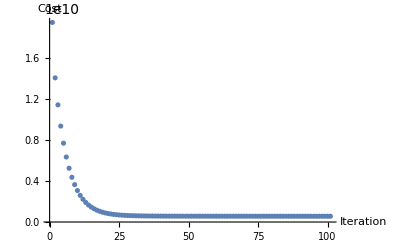

```mathematica
α = 0.1;

θ = Table[RandomReal[{-1,1}],{n+1},{ny}];


Print["J(θ) = ",cost[θVars]];
Print["∂/(∂θ)J(θ) = ",MatrixForm[dCost[θVars]]];
Print[];
Print[];


costList ={cost[θ]};
Print["θ= ",MatrixForm[θ],"     J(θ) = ",cost[θ],"      ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[dCost[θ]]];
Print["θ := θ - α ∂/(∂SubscriptBox[θ, i])J(θ) = ",MatrixForm[θ]," - ",α,MatrixForm[dCost[θ]]," = ",MatrixForm[θ-α dCost[θ]]];
Print[];
Print["________________________"];

Do[

θ= θ-α dCost[θ];
AppendTo[costList,cost[θ]];
,{i,1,100}];
Print["Final values of θ: θ = ",MatrixForm[θ],"  which has cost J(θ) = ",cost[θ]];
Print[ListPlot[costList,AxesLabel->{"Iteration","Cost"},PlotRange->All]];
```

Question 3

```mathematica
(*Question 3-Predict House Prices*)
(*Use the test data*)testRows=Drop[TestData,1];

(*Select the same features as Question 1*)
xTest={1,#[[2]],#[[4]],#[[5]],#[[18]],#[[19]],#[[20]],#[[21]],#[[27]],#[[35]],#[[37]],#[[38]],encodeQual[#[[28]]],encodeQual[#[[31]]],encodeQual[#[[41]]],encodeQual[#[[54]]],encodeQual[#[[64]]],(*TotalSF*)safeNum[#[[39]]]+safeNum[#[[44]]]+safeNum[#[[45]]],#[[46]],(*TotalBathrooms*)safeNum[#[[50]]]+0.5 safeNum[#[[51]]]+safeNum[#[[48]]]+0.5 safeNum[#[[49]]],#[[52]],#[[53]],#[[55]],#[[57]],#[[60]],#[[62]],#[[63]],#[[67]],#[[68]],#[[69]],#[[70]],#[[71]],#[[72]],#[[76]],#[[77]],#[[78]]}&/@testRows;

(*Clean missing values using training column means*)
xTestFeatures=xTest[[All,2;;-1]];

xTestFeatures=Transpose[MapThread[Function[{col,mean},Replace[col,"NA"->mean,{1}]],{Transpose[xTestFeatures],means}]];

(*Normalize using training values*)
xTestScaled=Prepend[#,1.0]&/@((#-means)/stds&/@xTestFeatures);

(*Predict using trained theta from Question 2*)
linearPredictions=Flatten[xTestScaled.θ];

(*Get IDs from test.csv*)
testIDs=testRows[[All,1]];

(*Format the answer*)
answer3=Prepend[Transpose[{testIDs,Round[linearPredictions,0.01]}],{"id","price"}];

Print[MatrixForm[Take[answer3,11]]];

Print["Number of predictions: ",Length[linearPredictions]];
```

(id | price
1461 | 122282.
1462 | 169466.
1463 | 162982.
1464 | 195165.
1465 | 197400.
1466 | 167209.
1467 | 186450.
1468 | 158769.
1469 | 198469.
1470 | 111667.)

Number of predictions: 1459

Question 4

```mathematica
linearPredictions=Flatten[x.θ];

(*Calculate errors*)
linearErrors=Flatten[y]-linearPredictions;

(*Calculate MSE*)
linearMSE=Mean[linearErrors^2];

(*Calculate RMSE*)
linearRMSE=Sqrt[linearMSE];

(*Calculate R Squared*)
linearR2=1-Total[linearErrors^2]/Total[(Flatten[y]-Mean[Flatten[y]])^2];

(*Display results*)
Print["MSE: ",N[linearMSE]];
Print["RMSE: ",N[linearRMSE]];
Print["R Squared: ",N[linearR2]];
```

MSE: 1.1266×10^9

RMSE: 33564.8

R Squared: 0.821368

Question 5

```mathematica
xOriginal=x[[All,2;;-1]];

(*Create polynomial features*)
xPolynomial=Map[Prepend[Join[#,#^2],1]&,xOriginal];

(*Display dimensions*)
Print["Original dimensions: ",Dimensions[x]];
Print["Polynomial dimensions: ",Dimensions[xPolynomial]];

(*Display first polynomial input*)
Print["First polynomial input: ",First[xPolynomial]];
(*Split polynomial data into training and validation*)split=Round[0.8 Length[xPolynomial]];

xPolyTrain=Take[xPolynomial,split];
xPolyValidation=Drop[xPolynomial,split];

yPolyTrain=Take[y,split];
yPolyValidation=Drop[y,split];

Print["Training dimensions: ",Dimensions[xPolyTrain]];
Print["Validation dimensions: ",Dimensions[xPolyValidation]];
```

Original dimensions: {1460,36}

Polynomial dimensions: {1460,71}

First polynomial input: {1,(151 √(4377/4637375005))/2,-0.229293,-(3017569 √(1459/77459052191355335))/2,(263 √(1459/59484415))/2,-(21 √(2918/39785))/11,(15443 √(1459/78805387415))/2,(6619 √(1459/20712280510))/2,0.511243,(63841 √(1459/4492778626735))/2,-(11327 √(1459/562044914565))/2,-(609171 √(1459/151804295575535))/2,(147 √(4377/21368195))/2,(373 √(1459/25185))/154,156 √(2918/89475005),(713 √(1459/342549215))/2,(277 √(1459/406307415))/2,-(1531 √(1459/524980085788135))/2,-(8533 √(1459/1838171248015))/2,1.64169,(39 √(1459/20696887))/2,-17 √(1459/9436710),541 √(1459/513520690),-(179 √(1459/12925015))/2,1.02081,17 √(1459/4342186),(15647 √(10213/5077360998105))/2,-(137597 √(1459/1357155241735))/6,(2617 √(1459/53330029915))/2,-(32053 √(1459/2904394487415))/2,-(2489 √(1459/167066690035))/2,-(21989 √(1459/2417164896335))/2,-1007 √(1459/313763677610),-(31747 √(1459/47843152205815))/2,-(631 √(1459/56832179))/2,(269 √(1459/1371384935))/2,99799977/18549500020,0.0525754,13285249375181299/309836208765421340,100917571/237937660,1286838/4813985,347951437291/315221549660,63920483899/82849122040,0.26137,5946407316979/17971114506940,187191055411/2248179658260,541419299264619/607217182302140,94582593/85472780,202989211/597287460,71012448/89475005,741710371/1370196860,111947611/1625229660,3419839099/2099920343152540,106232837851/7352684992060,2.69516,2219139/82787548,421651/9436710,427021579/513520690,46747819/51700060,1.04205,421651/4342186,2500434583717/20309443992420,27623151302731/48857588702460,9992237251/213320119660,1498969026331/11617577949660,9038681539/668266760140,705450020539/9668659585340,1479497491/313763677610,1470485261131/191372608823260,580916899/227328716,105574699/5485539740}

Training dimensions: {1168,71}

Validation dimensions: {292,71}

Question 6

```mathematica
(*Polynomial Regression using Gradient Descent*)
(*Use existing polynomial data*)xPolyTrain=N[xPolyTrain];
yPolyTrain=Flatten[N[yPolyTrain]];

m=Length[yPolyTrain];

(*Cost function*)
polyCost[t_]:=Total[(xPolyTrain.t-yPolyTrain)^2]/(2 m);

(*Gradient*)
polyGradient[t_]:=Transpose[xPolyTrain].(xPolyTrain.t-yPolyTrain)/m;

(*Initial parameters*)
thetaPoly=ConstantArray[0.,Dimensions[xPolyTrain][[2]]];

(*Settings*)
alphaPoly=0.01;
tolerance=0.000001;
maxIterations=1000;

oldCost=polyCost[thetaPoly];
iteration=0;
converged=False;

(*Gradient Descent*)
While[iteration<maxIterations&&!converged,gradient=polyGradient[thetaPoly];
newTheta=thetaPoly-alphaPoly gradient;
newCost=polyCost[newTheta];
(*Reduce learning rate if cost increases*)If[newCost>oldCost,alphaPoly=alphaPoly/2,(*Accept the new parameters*)improvement=oldCost-newCost;
thetaPoly=newTheta;
iteration++;
If[Abs[improvement]<tolerance,converged=True];
oldCost=newCost;];];

(*Display results*)
Print["Iterations used: ",iteration];
Print["Converged: ",converged];
Print["Final learning rate: ",alphaPoly];
Print["Final cost: ",polyCost[thetaPoly]];
Print["Number of parameters: ",Length[thetaPoly]];
Print["Polynomial parameters: ",thetaPoly];
```

Iterations used: 1000

Converged: False

Final learning rate: 0.00125

Final cost: 1.08383×10^9

Number of parameters: 71

Polynomial parameters: {26948.5,-6040.51,2353.17,-864.509,8068.32,6575.49,13067.7,7640.27,-847.932,4539.77,-3212.25,-2777.68,874.378,7411.37,5531.67,3275.65,9320.48,3609.97,-2947.87,6989.77,6208.03,-6743.99,4156.11,3122.32,8344.82,4495.63,2889.39,-635.501,-735.748,-6090.32,-732.621,-4532.88,-2199.16,-1962.01,-145.383,-2771.1,3898.84,339.394,204.697,1242.02,3210.92,5964.47,11547.6,2711.65,8365.36,2416.95,8109.59,4174.4,2092.19,13731.2,4544.77,-1406.24,-4052.47,22.8667,7804.93,796.795,183.015,5416.08,11126.7,7282.91,6993.09,3897.34,3795.97,231.857,3087.11,386.1,2948.99,-239.06,96.4235,8041.05,14946.3}

Question 7

```mathematica
(*Use the test features from Question 3*)xNewScaled=N[(#-means)/stds&/@xTestFeatures];

(*Create polynomial features using Question 5 method*)
xNewPoly=Map[Prepend[Join[#,#^2],1]&,xNewScaled];

(*Use the trained model from Question 6*)
polyPredictions=Flatten[N[xNewPoly].thetaPoly];

(*Get house IDs from test.csv*)
ids=testRows[[All,1]];

(*Display predicted prices*)
answer7=Prepend[Transpose[{ids,Round[polyPredictions,0.01]}],{"id","price"}];

Print[MatrixForm[Take[answer7,11]]];
```

(id | price
1461 | 111989.
1462 | 161359.
1463 | 153171.
1464 | 169054.
1465 | 182878.
1466 | 126267.
1467 | 247431.
1468 | 133606.
1469 | 150616.
1470 | 116753.)

Question 8

```mathematica
(*Use the same validation houses for both models*)
xLinearValidation=Take[x,-Length[yPolyValidation]];

(*Linear model predictions from Question 2*)
linearValidationPredictions=Flatten[xLinearValidation.θ];

(*Non-linear model predictions from Question 6*)
polyValidationPredictions=Flatten[N[xPolyValidation].thetaPoly];

(*Actual house prices*)
actualPrices=Flatten[N[yPolyValidation]];

(*Calculate errors*)
linearErrors=actualPrices-linearValidationPredictions;
polyErrors=actualPrices-polyValidationPredictions;

(*Calculate MSE*)
linearMSE=Mean[linearErrors^2];
polyMSE=Mean[polyErrors^2];

(*Calculate RMSE*)
linearRMSE=Sqrt[linearMSE];
polyRMSE=Sqrt[polyMSE];

(*Calculate R Squared*)
linearR2=1-Total[linearErrors^2]/Total[(actualPrices-Mean[actualPrices])^2];

polyR2=1-Total[polyErrors^2]/Total[(actualPrices-Mean[actualPrices])^2];

(*Display results*)
Print["Linear MSE: ",N[linearMSE]];
Print["Linear RMSE: ",N[linearRMSE]];
Print["Linear R Squared: ",N[linearR2]];

Print["Non-Linear MSE: ",N[polyMSE]];
Print["Non-Linear RMSE: ",N[polyRMSE]];
Print["Non-Linear R Squared: ",N[polyR2]];
```

Linear MSE: 1.893×10^9

Linear RMSE: 43508.6

Linear R Squared: 0.717689

Non-Linear MSE: 8.11666×10^9

Non-Linear RMSE: 90092.5

Non-Linear R Squared: -0.210471